```mathematica
Quit[]
```

Secondary spin corrections to the trajectories and velocities for generic orbits in the Hamilton-Jacobi formalism.  See arXiv:2410.05769 (https://arxiv.org/abs/2410.05769v1 )

This notebook provides all the necessary terms to compute the trajectories and velocities at first order in the secondary spin, in two parametrizations:
- the fixed constants of motion parametrization (E_s=J_zs=K_s=0), introduced by Witzany in PRD 100, 104030 (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.100.104030 )
  All the trajectories and velocities in this parametrization are labelled by FC
- the fixed turning points on average (⟨δr_1⟩=⟨δr_2⟩=⟨δz_1⟩=0), presented by Drummond and Hughes in PRD 105, 124040 (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.105.124040 ) and PRD 105, 124041 (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.105.124041 )
  All the trajectories and velocities in this parametrization are labelled by DH.

Remark 1: all functions in the part “Generic orbits” were tested in the limit of equatorial orbits. However, (perhaps not surprisingly) using functions designed for generic orbits in the equatorial limit is not the most efficient way to compute trajectories and velocities. The reason is that the radial and polar motion decoupled when θ=π/2, thus the radial, azimuthal and coordinate motion is independent on θ in such a limit.

Remark 2: we use z=Cosθ instead of θ. Much more convenient...

Remark 3: the functions blow up for e_g=0, i.e. when the referential geodesic is a spherical orbits. You can set e_g to the very small value and the results are correct, but you lose digits in precision. Spherical orbits require special care for removing singularities for e_g=0, and they will be considered in a follow up project...

All computations are performed in the Chapters (as they are called in Mathematica) “Computation quantities for the trajectories and velocities” and “Comparison between parametrizations: fixed turning points (on average) and fixed constants of motion” within either “Generic orbits and Equatorial orbits”. All the remaining Chapters and Sections only defined the functions.

Run each Chapters and Section in the order shown.

This notebook include comparisons with data produced with the code used in PRD 108, 044041 (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.108.044041 ) kindly provided Viktor Skoupý.

PREREQUISITEs: the files “data_DHS_code_generic_orbit.m” and  “data_DHS_code_near_equatorial_orbit.m” for comparison with code of  PRD 108, 044041

If you make use of this notebook, please acknowledge "Piovano, Pantelidou, Mac Uilliam and Witzany” arXiv:2410.05769 (https://arxiv.org/abs/2410.05769v1 )

### Convention for EoM

Here we follow the same convention of  CQG, Volume 37, Number 14  (https://iopscience.iop.org/article/10.1088/1361-6382/ab79d5 )

r_1== p/(1-e)
r_2== p/(1+e)
z_1==√(1-x^2)

or

p==2(r_1 r_2)/(r_1+r_2)
e== (r_1-r_2)/(r_1+r_2)
x ==  Sign[ℒ]√(1-z_1^2)

(circular) 0<e<1 (parabolic)
(retrograde) -1 < x < 1 (prograde)
p> p_LSO(e,x)

Equatorial orbits

x==±1
z_1==0
𝒬 ==0

“spar” and “sort” are the parallel and orthogonal component of the spin to the total angular momentum.

## 1) Set-up

```mathematica
SetDirectory[NotebookDirectory[]];
```

Import data produced with code used in PRD 108, 044041.

```mathematica
dataDHScodegenericorbit=Import["data_DHS_code_generic_orbit.m"]; (*data for generic orbits*)
```

```mathematica
dataDHScodenearequorbit=Import["data_DHS_code_near_equatorial_orbit.m"];  (*data for equatorial orbits*)
```

## 2) Geodesic quantities

### Constants of motion

```mathematica
EEgfun[a_,p_,e_,xg_]:=Module[{r1g,r2g,z1g,ddinc,ffinc,gginc,hhinc,κg,ϵg,ρg,ηg,σg,Δr1g,Δr2g,EEgnum,EEgden,EEgdisc},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

ddinc[r_]:=(r^2-2r+a^2) (r^2+a^2 z1g^2);
ffinc[r_]:=r^4+a^2(r+2)r+a^2 z1g^2 (r^2-2r+a^2);
gginc[r_]:=2 a r;
hhinc[r_]:=r(r-2)+(r^2-2r+a^2)z1g^2/(1-z1g^2);

κg=ddinc[r2g]*hhinc[r1g]-ddinc[r1g]*hhinc[r2g];
ϵg=ddinc[r2g]*gginc[r1g]-ddinc[r1g]*gginc[r2g];
ρg=ffinc[r2g]*hhinc[r1g]-ffinc[r1g]*hhinc[r2g];
ηg=ffinc[r2g]*gginc[r1g]-ffinc[r1g]*gginc[r2g];
σg=gginc[r2g]*hhinc[r1g]-gginc[r1g]*hhinc[r2g];

Δr1g=(a^2-2 r1g+r1g^2);
Δr2g=(a^2-2 r2g+r2g^2);

EEgnum=1/((-1+z1g^2)^2)(8 a^2 (-1+z1g^2) (-r1g r2g+a^2 z1g^2) (-r1g r2g (r1g^2+r1g (-2+r2g)+(-2+r2g) r2g)+a^4 z1g^2-a^2r1g r2g (1+z1g^2))+(r1g r2g (r1g^2 (-2+r2g)+r1g (-2+r2g) r2g-2 r2g^2)+a^4 z1g^2 (4+(-2+r1g+r2g)z1g^2)+a^2 (-4 r1g r2g+(r1g+r2g) (r1g^2+r2g^2) z1g^2)) ((-2+r1g) r1g (-2+r2g) r2g (r1g+r2g)+a^4 z1g^2 (2+(-2+r1g+r2g) z1g^2)+a^2 (-2 r1g r2g+(r1g^3+r1g^2 (-2+r2g)+r1g (-2+r2g) r2g+(-2+r2g) r2g^2) z1g^2)));

EEgden=1/((-1+z1g^2)^2)(16a^2 (-1+z1g^2) (-r1g r2g+a^2z1g^2) (-r1g r2g (r1g^2+r1g r2g+r2g^2)+a^4 z1g^2-a^2r1g r2g (1+z1g^2))+(r1g r2g (r1g^2 (-2+r2g)+r1g (-2+r2g) r2g-2 r2g^2)+a^4 z1g^2 (4+(-2+r1g+r2g)z1g^2)+a^2(-4 r1g r2g+(r1g+r2g) (r1g^2+r2g^2) z1g^2))^2);

EEgdisc=(8 a^2 Δr1g (r1g+r2g) Δr2g (r1g^2+a^2 z1g^2) (-r1g r2g+a^2 z1g^2)^3 (r2g^2+a^2 z1g^2))/((-1+z1g^2)^3);

Sqrt[(EEgnum-2RealSign[xg] Sqrt[EEgdisc])/EEgden]

]
```

```mathematica
Lzgfun[a_,p_,e_,xg_]:=Module[{r1g,r2g,z1g,EEg,Lzgzaux,ddinc,ffinc,gginc,hhinc},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];

ddinc[r_]:=(r^2-2r+a^2) (r^2+a^2 z1g^2);
ffinc[r_]:=r^4+a^2(r+2)r+a^2 z1g^2 (r^2-2r+a^2);
gginc[r_]:=2 a r;
hhinc[r_]:=r(r-2)+(r^2-2r+a^2)z1g^2/(1-z1g^2);

Lzgzaux=Sqrt[(gginc[r2g]^2+hhinc[r2g]ffinc[r2g])EEg^2-hhinc[r2g]ddinc[r2g]];

(-gginc[r2g] EEg+RealSign[xg] Lzgzaux)/hhinc[r2g]
]
```

```mathematica
KKgfun[a_,p_,e_,xg_]:=(Lzgfun[a,p,e,xg]-a EEgfun[a,p,e,xg])^2+(1-xg^2)(a^2(1-EEgfun[a,p,e,xg]^2)+Lzgfun[a,p,e,xg]^2/xg^2);
```

#### Slightly modified version of the functions for the constants of motion

These versions of the functions for the constants of motion is more useful for derivatives of the geodesics frequencies wrt to r_(1g) , r_(2g) and z_(1g) . The “sgn” in all the functions denotes the type of orbits. +1 is for prograde orbits, -1 for retrograde orbits. It is equivalent to the sign of x.

```mathematica
EEgfunsgn[a_,r1g_,r2g_,z1g_,sgn_]:=Module[{ddinc,ffinc,gginc,hhinc,κg,ϵg,ρg,ηg,σg,Δr1g,Δr2g,EEgnum,EEgden,EEgdisc},

ddinc[r_]:=(r^2-2r+a^2) (r^2+a^2 z1g^2);
ffinc[r_]:=r^4+a^2(r+2)r+a^2 z1g^2 (r^2-2r+a^2);
gginc[r_]:=2 a r;
hhinc[r_]:=r(r-2)+(r^2-2r+a^2)z1g^2/(1-z1g^2);


κg=ddinc[r2g]*hhinc[r1g]-ddinc[r1g]*hhinc[r2g];
ϵg=ddinc[r2g]*gginc[r1g]-ddinc[r1g]*gginc[r2g];
ρg=ffinc[r2g]*hhinc[r1g]-ffinc[r1g]*hhinc[r2g];
ηg=ffinc[r2g]*gginc[r1g]-ffinc[r1g]*gginc[r2g];
σg=gginc[r2g]*hhinc[r1g]-gginc[r1g]*hhinc[r2g];

Δr1g=(a^2-2 r1g+r1g^2);
Δr2g=(a^2-2 r2g+r2g^2);

EEgnum=1/((-1+z1g^2)^2)(8 a^2 (-1+z1g^2) (-r1g r2g+a^2 z1g^2) (-r1g r2g (r1g^2+r1g (-2+r2g)+(-2+r2g) r2g)+a^4 z1g^2-a^2r1g r2g (1+z1g^2))+(r1g r2g (r1g^2 (-2+r2g)+r1g (-2+r2g) r2g-2 r2g^2)+a^4 z1g^2 (4+(-2+r1g+r2g)z1g^2)+a^2 (-4 r1g r2g+(r1g+r2g) (r1g^2+r2g^2) z1g^2)) ((-2+r1g) r1g (-2+r2g) r2g (r1g+r2g)+a^4 z1g^2 (2+(-2+r1g+r2g) z1g^2)+a^2 (-2 r1g r2g+(r1g^3+r1g^2 (-2+r2g)+r1g (-2+r2g) r2g+(-2+r2g) r2g^2) z1g^2)));

EEgden=1/((-1+z1g^2)^2)(16a^2 (-1+z1g^2) (-r1g r2g+a^2z1g^2) (-r1g r2g (r1g^2+r1g r2g+r2g^2)+a^4 z1g^2-a^2r1g r2g (1+z1g^2))+(r1g r2g (r1g^2 (-2+r2g)+r1g (-2+r2g) r2g-2 r2g^2)+a^4 z1g^2 (4+(-2+r1g+r2g)z1g^2)+a^2(-4 r1g r2g+(r1g+r2g) (r1g^2+r2g^2) z1g^2))^2);

EEgdisc=(8 a^2 Δr1g (r1g+r2g) Δr2g (r1g^2+a^2 z1g^2) (-r1g r2g+a^2 z1g^2)^3 (r2g^2+a^2 z1g^2))/((-1+z1g^2)^3);

Sqrt[(EEgnum-2RealSign[sgn] Sqrt[EEgdisc])/EEgden]

]
```

```mathematica
Lzgfunsgn[a_,r1g_,r2g_,z1g_,sgn_]:=Module[{EEg,Lzgzaux,ddinc,ffinc,gginc,hhinc},

EEg=EEgfunsgn[a,r1g,r2g,z1g,sgn];

ddinc[r_]:=(r^2-2r+a^2) (r^2+a^2 z1g^2);
ffinc[r_]:=r^4+a^2(r+2)r+a^2 z1g^2 (r^2-2r+a^2);
gginc[r_]:=2 a r;
hhinc[r_]:=r(r-2)+(r^2-2r+a^2)z1g^2/(1-z1g^2);

Lzgzaux=Sqrt[(gginc[r2g]^2+hhinc[r2g]ffinc[r2g])EEg^2-hhinc[r2g]ddinc[r2g]];

(-gginc[r2g] EEg+sgn Lzgzaux)/hhinc[r2g]
]
```

```mathematica
KKgfunsgn[a_,r1g_,r2g_,z1g_,sgn_]:=(Lzgfunsgn[a,r1g,r2g,z1g,sgn]-a EEgfunsgn[a,r1g,r2g,z1g,sgn])^2+z1g^2(a^2(1-EEgfunsgn[a,r1g,r2g,z1g,sgn]^2)+Lzgfunsgn[a,r1g,r2g,z1g,sgn]^2/(1-z1g^2));
```

### Radial and polar geodesic frequencies

```mathematica
Υrgfun[a_,p_,e_,xg_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,krg},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));

π/(2EllipticK[krg])√((1-EEg^2)(r1g-r3g)(r2g-r4g))
]
```

```mathematica
Υzgfun[a_,p_,e_,xg_]:=Module[{r1g,r2g,z1g,EEg,Lzg,z2g,kzg},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];

z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

kzg=a^2(1-EEg^2)z1g^2/z2g^2;
(π z2g)/(2EllipticK[kzg])
]
```

#### Slightly modified version of the functions for the geodesics frequencies

These functions s are used for the derivatives of the geodesic frequencies wrt to r_(1g), r_(2g) and z_(1g). The “sgn” in all the functions denotes the type of orbits. +1 is for prograde orbits, -1 for retrograde orbits. It is equivalent to the sign of x.

```mathematica
Υrgfunsgn[a_,r1g_,r2g_,z1g_,sgn_]:=Module[{EEg,Lzg,KKg,r3g,r4g,krg},
EEg=EEgfunsgn[a,r1g,r2g,z1g,sgn];
Lzg=Lzgfunsgn[a,r1g,r2g,z1g,sgn];
KKg=KKgfunsgn[a,r1g,r2g,z1g,sgn];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));

π/(2EllipticK[krg])√((1-EEg^2)(r1g-r3g)(r2g-r4g))
]
```

```mathematica
Υzgfunsgn[a_,r1g_,r2g_,z1g_,sgn_]:=Module[{EEg,Lzg,z2g,kzg},
EEg=EEgfunsgn[a,r1g,r2g,z1g,sgn];
Lzg=Lzgfunsgn[a,r1g,r2g,z1g,sgn];

z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

kzg=a^2(1-EEg^2)z1g^2/z2g^2;
(π z2g)/(2EllipticK[kzg])
]
```

### Coordinate time and azimuthal geodesic frequencies

#### Coordinate time geodesic frequency

```mathematica
Υtgrfun[a_,p_,e_,xg_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,rp,rm,krg,ellK,hr,hp,hm},
EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

rp=1+√(1-a^2);
rm=1-√(1-a^2);

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
ellK=EllipticK[krg];
hr=(r1g-r2g)/(r1g-r3g);
hp=hr(r3g-rp)/(r2g-rp);
hm=hr (r3g-rm)/(r2g-rm);

(4+a^2)EEg+EEg(1/2(4+r1g+r2g+r3g)r3g- (r1g r2g)/2+(r1g-r3g)(r2g-r4g)EllipticE[krg]/(2ellK)+1/2(4+2/(1-EEg^2))(r2g-r3g)EllipticPi[hr,krg]/ellK)+(2EEg)/(rp-rm)(((4-a Lzg/EEg)rp-2a^2)/(r3g-rp)(1-(r2g-r3g)/(r2g-rp)EllipticPi[hp,krg]/ellK))-(2EEg)/(rp-rm)(((4-a Lzg/EEg)rm-2a^2)/(r3g-rm)(1-(r2g-r3g)/(r2g-rm)EllipticPi[hm,krg]/ellK))
]
```

```mathematica
Υtgzfun[a_,p_,e_,xg_]:=Module[{z1g,EEg,Lzg,KKg,z2g,kzg},
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

kzg=a^2(1-EEg^2)z1g^2/z2g^2;
If[z1g==0,
-a^2EEg,
-a^2 EEg+(EEg(KKg-(Lzg-a EEg)^2))/((1-EEg^2)z1g^2)(1-EllipticE[kzg]/EllipticK[kzg])
]
]
```

#### Azimuthal time geodesic frequency

```mathematica
Υϕgrfun[a_,p_,e_,xg_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,rp,rm,krg,ellK,hr,hp,hm},
EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

rp=1+√(1-a^2);
rm=1-√(1-a^2);

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
ellK=EllipticK[krg];
hr=(r1g-r2g)/(r1g-r3g);
hp=hr(r3g-rp)/(r2g-rp);
hm=hr (r3g-rm)/(r2g-rm);

a/(rp-rm)((2 EEg rp-a Lzg)/(r3g-rp)(1-(r2g-r3g)/(r2g-rp)EllipticPi[hp,krg]/ellK))-a/(rp-rm)((2 EEg rm-a Lzg)/(r3g-rm)(1-(r2g-r3g)/(r2g-rm)EllipticPi[hm,krg]/ellK))
]
```

```mathematica
Υϕgzfun[a_,p_,e_,xg_]:=Module[{z1g,EEg,Lzg,z2g,kzg},
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];

z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

kzg=a^2(1-EEg^2)z1g^2/z2g^2;
Lzg/EllipticK[kzg] EllipticPi[z1g^2,kzg]
]
```

#### Slightly modified version of the functions for the geodesic coordinate time frequency

These functions s are used for the derivatives of the geodesic frequencies wrt to r_(1g), r_(2g) and z_(1g). The “sgn” in all the functions denotes the type of orbits. +1 is for prograde orbits, -1 for retrograde orbits. It is equivalent to the sign of x.

```mathematica
Υtgrfunsgn[a_,r1g_,r2g_,z1g_,sgn_]:=Module[{EEg,Lzg,KKg,r3g,r4g,rp,rm,krg,ellK,hr,hp,hm},
EEg=EEgfunsgn[a,r1g,r2g,z1g,sgn];
Lzg=Lzgfunsgn[a,r1g,r2g,z1g,sgn];
KKg=KKgfunsgn[a,r1g,r2g,z1g,sgn];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

rp=1+√(1-a^2);
rm=1-√(1-a^2);

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
ellK=EllipticK[krg];
hr=(r1g-r2g)/(r1g-r3g);
hp=hr(r3g-rp)/(r2g-rp);
hm=hr (r3g-rm)/(r2g-rm);

(4+a^2)EEg+EEg(1/2(4+r1g+r2g+r3g)r3g- (r1g r2g)/2+(r1g-r3g)(r2g-r4g)EllipticE[krg]/(2ellK)+1/2(4+2/(1-EEg^2))(r2g-r3g)EllipticPi[hr,krg]/ellK)+(2EEg)/(rp-rm)(((4-a Lzg/EEg)rp-2a^2)/(r3g-rp)(1-(r2g-r3g)/(r2g-rp)EllipticPi[hp,krg]/ellK))-(2EEg)/(rp-rm)(((4-a Lzg/EEg)rm-2a^2)/(r3g-rm)(1-(r2g-r3g)/(r2g-rm)EllipticPi[hm,krg]/ellK))
]
```

```mathematica
Υtgzfunsgn[a_,r1g_,r2g_,z1g_,sgn_]:=Module[{EEg,Lzg,KKg,z2g,kzg},
EEg=EEgfunsgn[a,r1g,r2g,z1g,sgn];
Lzg=Lzgfunsgn[a,r1g,r2g,z1g,sgn];
KKg=KKgfunsgn[a,r1g,r2g,z1g,sgn];

z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;

-a^2 EEg+(EEg(KKg-(Lzg-a EEg)^2))/((1-EEg^2)z1g^2)(1-EllipticE[kzg]/EllipticK[kzg])
]
```

#### Slightly modified version of the functions for the geodesics azimuthal frequency

These functions s are used for the derivatives of the geodesic frequencies wrt to r_(1g), r_(2g) and z_(1g). The “sgn” in all the functions denotes the type of orbits. +1 is for prograde orbits, -1 for retrograde orbits. It is equivalent to the sign of x.

```mathematica
Υϕgrfunsgn[a_,r1g_,r2g_,z1g_,sgn_]:=Module[{EEg,Lzg,KKg,r3g,r4g,rp,rm,krg,ellK,hr,hp,hm},
EEg=EEgfunsgn[a,r1g,r2g,z1g,sgn];
Lzg=Lzgfunsgn[a,r1g,r2g,z1g,sgn];
KKg=KKgfunsgn[a,r1g,r2g,z1g,sgn];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

rp=1+√(1-a^2);
rm=1-√(1-a^2);

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
ellK=EllipticK[krg];
hr=(r1g-r2g)/(r1g-r3g);
hp=hr(r3g-rp)/(r2g-rp);
hm=hr (r3g-rm)/(r2g-rm);

a/(rp-rm)((2 EEg rp-a Lzg)/(r3g-rp)(1-(r2g-r3g)/(r2g-rp)EllipticPi[hp,krg]/ellK))-a/(rp-rm)((2 EEg rm-a Lzg)/(r3g-rm)(1-(r2g-r3g)/(r2g-rm)EllipticPi[hm,krg]/ellK))
]
```

```mathematica
Υϕgzfunsgn[a_,r1g_,r2g_,z1g_,sgn_]:=Module[{EEg,Lzg,KKg,z2g,kzg},
EEg=EEgfunsgn[a,r1g,r2g,z1g,sgn];
Lzg=Lzgfunsgn[a,r1g,r2g,z1g,sgn];

z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
Lzg/EllipticK[kzg] EllipticPi[z1g^2,kzg]
]
```

### Spin precession frequency

```mathematica
Υpfun[a_,p_,e_,xg_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,krg,z2g,kzg,ψfreq},
EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;

(*(√KKg((r3g^2+a^2)EEg-a Lzg))/(r3g^2+KKg)+

((r2g-r3g)((KKg-a^2)EEg+a Lzg))/((r2g^2+KKg)(r3g^2+KKg))Im[(r2g+I √KKg)(r3g+I √KKg)EllipticPi[(r1g-r2g)/(r1g-r3g)(r3g-I √KKg)/(r2g-I √KKg),krg] 1/EllipticK[krg]]-EEg √KKg+((KKg-a^2)EEg+a Lzg)/(√KKg)EllipticPi[(a^2 z1g^2)/KKg,kzg] 1/EllipticK[kzg],
*)

ψfreq=(√KKg((r3g^2+a^2)EEg-a Lzg))/(r3g^2+KKg)+((r2g-r3g)((KKg-a^2)EEg+a Lzg))/((r2g^2+KKg)(r3g^2+KKg))1/(2I)((r2g+I √KKg)(r3g+I √KKg)EllipticPi[(r1g-r2g)/(r1g-r3g)(r3g-I √KKg)/(r2g-I √KKg),krg] 1/EllipticK[krg]-(r2g-I √KKg)(r3g-I √KKg)EllipticPi[(r1g-r2g)/(r1g-r3g)(-r3g-I √KKg)/(-r2g-I √KKg),krg] 1/EllipticK[krg])-EEg √KKg+((KKg-a^2)EEg+a Lzg)/(√KKg)EllipticPi[(a^2 z1g^2)/KKg,kzg] 1/EllipticK[kzg];
Re[ψfreq]
]
```

### Homogeneous angles

Inversion of the integrals in A12 and A13 in arXiv:1903.03651

```mathematica
χrfun[wr_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,EEg,Lzg,KKg,r3g,r4g,krg,ellK,jSN},
{EEg,Lzg,KKg}=const;
r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
ellK=EllipticK[krg];
jSN=JacobiSN[1/π ellK wr,krg];

If[Mod[wr,2Pi]<Pi,
ArcSin[2/(r1g-r2g)(r3g(r1g-r2g)jSN^2-r2g(r1g-r3g))((r1g-r2g)jSN^2-(r1g-r3g))^(-1)-(r1g+r2g)/(r1g-r2g)]+2π*Floor[wr/(2π)]
,
π-ArcSin[2/(r1g-r2g)(r3g(r1g-r2g)jSN^2-r2g(r1g-r3g))((r1g-r2g)jSN^2-(r1g-r3g))^(-1)-(r1g+r2g)/(r1g-r2g)]+2π*Floor[wr/(2π)]
]
]
```

```mathematica
Sinχrfun[wr_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,EEg,Lzg,KKg,r3g,r4g,krg,ellK,jSN},
{EEg,Lzg,KKg}=const;
r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
ellK=EllipticK[krg];
jSN=JacobiSN[1/π ellK wr,krg];

2/(r1g-r2g)(r3g(r1g-r2g)jSN^2-r2g(r1g-r3g))((r1g-r2g)jSN^2-(r1g-r3g))^(-1)-(r1g+r2g)/(r1g-r2g)
]
```

The π/2 term is added to match the convention in Viktor’s paper and the Toolkit

```mathematica
χzfun[wz_,a_,p_,e_,xg_,const_]:=Module[{z1g,EEg,Lzg,z2g,kzg,ellK},
EEg=const[[1]];
Lzg=const[[2]];

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
ellK=EllipticK[kzg];

JacobiAmplitude[2/π ellK(wz+π/2),kzg]
]
```

#### Derivatives of χ_z with respect to z_(1g)

```mathematica
dχzdz1gfun[wz_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,EEg,Lzg,z2g,kzg,ellK,αz},
EEg=const[[1]];
Lzg=const[[2]];
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

kzg=a^2(1-EEg^2)z1g^2/z2g^2;
ellK=EllipticK[kzg];

αz=(π+2 wz)/π ellK;

1/(2 (1-kzg) kzg π)(kzg π JacobiCD[(2 wz)/π ellK,kzg] JacobiCN[αz,kzg]+JacobiDN[αz,kzg] ((π+2 wz) EllipticE[kzg]-π JacobiEpsilon[αz,kzg]))2a^2 z1g (1-EEg^2)(-(Lzg ^2z1g^2)/((1-z1g^2)^2 z2g^4)+1/z2g^2)
]
```

#### Spin precession phase

```mathematica
ψrfun[wr_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,krg,ellK,xaux},
{EEg,Lzg,KKg}=const;
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
ellK=EllipticK[krg];
xaux=JacobiAmplitude[wr/π ellK,krg];

(2(r2g-r3g)((KKg-a^2)EEg+a Lzg))/((KKg+r2g^2)(KKg+r3g^2)√((1-EEg^2)(r1g-r3g)(r2g-r4g)))(Im[(r2g+I √KKg)(r3g+I √KKg)EllipticPi[(r1g-r2g)/(r1g-r3g)(r3g-I √KKg)/(r2g-I √KKg),xaux,krg]]-wr/π Im[(r2g+I √KKg)(r3g+I √KKg)EllipticPi[(r1g-r2g)/(r1g-r3g)(r3g-I √KKg)/(r2g-I √KKg),krg]])
]
```

```mathematica
ψzfun[wz_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,z2g,kzg,ellK,xaux},
{EEg,Lzg,KKg}=const;
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
ellK=EllipticK[kzg];
xaux=JacobiAmplitude[2/π ellK(wz+π/2),kzg];

-((a^2-KKg)EEg-a Lzg)/(√KKg z2g)(EllipticPi[(a^2z1g^2)/KKg,xaux,kzg]-2/π ellK(wz+π/2)EllipticPi[(a^2z1g^2)/KKg,kzg])
]
```

### Geodesics radial trajectories

#### Radial geodesic trajectories

```mathematica
rgfun[wr_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,EEg,Lzg,KKg,r3g,r4g,krg,ellK,jSN},
{EEg,Lzg,KKg}=const;
r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
ellK=EllipticK[krg];
jSN=JacobiSN[1/π ellK wr,krg];

(r3g(r1g-r2g)jSN^2-r2g(r1g-r3g))/((r1g-r2g)jSN^2-(r1g-r3g))
]
```

#### Derivatives radial trajectories wrt to w_r

```mathematica
drgdwrfun[wr_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,EEg,Lzg,KKg,r3g,r4g,krg,ellK,jSN},
{EEg,Lzg,KKg}=const;
r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
ellK=EllipticK[krg];
jSN=JacobiSN[1/π ellK wr,krg];

(2 ellK (r1g-r2g) (r1g-r3g) (r2g-r3g) JacobiCN[(ellK wr)/π,krg] JacobiDN[(ellK wr)/π,krg] jSN)/(π (-r1g+r3g+(r1g-r2g) jSN^2)^2)
]
```

#### Derivatives radial trajectories wrt to constant of motions

```mathematica
drgdEgfun[wr_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,krg,ellK,αr,jSN,drgdkrg,drgdr3g,dkrgdr3g,dkrgdr4g,dr3gdEg,dr4gdEg},
{EEg,Lzg,KKg}=const;
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
ellK=EllipticK[krg];
αr=wr/π ellK;
jSN=JacobiSN[αr,krg];

drgdkrg=(jSN (r1g-r2g) (r1g-r3g) (r2g-r3g) JacobiCN[(ellK wr)/π,krg] JacobiDN[(ellK wr)/π,krg] (wr EllipticE[krg]+jSN krg π JacobiCD[(ellK wr)/π,krg]-π JacobiEpsilon[(ellK wr)/π,krg]))/((1-krg) krg π (-r1g+r3g+jSN^2 (r1g-r2g))^2);
drgdr3g=-((r1g-r2g)^2 jSN^2 (1-jSN^2))/((-r1g+r3g+(r1g-r2g) jSN^2)^2);

dkrgdr3g =((r1g-r2g) (r1g-r4g))/((r1g-r3g)^2 (r2g-r4g));
dkrgdr4g =-((r1g-r2g) (r2g-r3g))/((r1g-r3g) (r2g-r4g)^2);
dr3gdEg=(2 EEg)/((1-EEg^2)^2)+1/(2 √(-(a^2 (KKg-(-a EEg+Lzg)^2))/((1-EEg^2) r1g r2g)+(-1/(1-EEg^2)+(r1g+r2g)/2)^2))(-(2 a^3 (-a EEg+Lzg))/((1-EEg^2) r1g r2g)-(2 a^2 EEg (KKg-(-a EEg+Lzg)^2))/((1-EEg^2)^2r1g r2g)-(4 EEg (-1/(1-EEg^2)+(r1g+r2g)/2))/((1-EEg^2)^2));
dr4gdEg=(a^2 (2 (-a^2 EEg+a (1+EEg^2) Lzg+EEg (KKg-Lzg^2)) r3g+(1-EEg^2) (-KKg+(-a EEg+Lzg)^2) dr3gdEg))/((1-EEg^2)^2 r1g r2g r3g^2);

(drgdr3g +drgdkrg dkrgdr3g) dr3gdEg+drgdkrg dkrgdr4g dr4gdEg
]
```

```mathematica
drgdLzgfun[wr_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,krg,ellK,αr,jSN,drgdkrg,drgdr3g,dkrgdr3g,dkrgdr4g,dr3gdLzg,dr4gdLzg},
{EEg,Lzg,KKg}=const;
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
ellK=EllipticK[krg];
αr=wr/π ellK;
jSN=JacobiSN[αr,krg];

drgdkrg=(jSN (r1g-r2g) (r1g-r3g) (r2g-r3g) JacobiCN[(ellK wr)/π,krg] JacobiDN[(ellK wr)/π,krg] (wr EllipticE[krg]+jSN krg π JacobiCD[(ellK wr)/π,krg]-π JacobiEpsilon[(ellK wr)/π,krg]))/((1-krg) krg π (-r1g+r3g+jSN^2 (r1g-r2g))^2);
drgdr3g=-((r1g-r2g)^2 jSN^2 (1-jSN^2))/((-r1g+r3g+(r1g-r2g) jSN^2)^2);

dkrgdr3g =((r1g-r2g) (r1g-r4g))/((r1g-r3g)^2 (r2g-r4g));
dkrgdr4g =-((r1g-r2g) (r2g-r3g))/((r1g-r3g) (r2g-r4g)^2);

dr3gdLzg=(a^2 (-a EEg+Lzg))/((1-EEg^2) r1g r2g √((a^2 (KKg-(-a EEg+Lzg)^2))/((-1+EEg^2) r1g r2g)+1/4 (2/(-1+EEg^2)+r1g+r2g)^2));

dr4gdLzg=(a^2 (2 (-a EEg+Lzg) r3g+(KKg-(-a EEg+Lzg)^2) dr3gdLzg))/((-1+EEg^2) r1g r2g r3g^2);

(drgdr3g +drgdkrg dkrgdr3g) dr3gdLzg+drgdkrg dkrgdr4g dr4gdLzg
]
```

```mathematica
drgdKgfun[wr_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,krg,ellK,αr,jSN,drgdkrg,drgdr3g,dkrgdr3g,dkrgdr4g,dr3gdKg,dr4gdKg},
{EEg,Lzg,KKg}=const;
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+√(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)));
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
ellK=EllipticK[krg];
αr=wr/π ellK;
jSN=JacobiSN[αr,krg];

drgdkrg=(jSN (r1g-r2g) (r1g-r3g) (r2g-r3g) JacobiCN[(ellK wr)/π,krg] JacobiDN[(ellK wr)/π,krg] (wr EllipticE[krg]+jSN krg π JacobiCD[(ellK wr)/π,krg]-π JacobiEpsilon[(ellK wr)/π,krg]))/((1-krg) krg π (-r1g+r3g+jSN^2 (r1g-r2g))^2);
drgdr3g=-((r1g-r2g)^2 jSN^2 (1-jSN^2))/((-r1g+r3g+(r1g-r2g) jSN^2)^2);

dkrgdr3g =((r1g-r2g) (r1g-r4g))/((r1g-r3g)^2 (r2g-r4g));
dkrgdr4g =-((r1g-r2g) (r2g-r3g))/((r1g-r3g) (r2g-r4g)^2);

dr3gdKg=-a^2/(2 (1-EEg^2) r1g r2g √((a^2 (KKg-(-a EEg+Lzg)^2))/((-1+EEg^2) r1g r2g)+1/4 (2/(-1+EEg^2)+r1g+r2g)^2));

dr4gdKg=(a^2 (r3g-(KKg-(-a EEg+Lzg)^2) dr3gdKg))/((1-EEg^2) r1g r2g r3g^2);

(drgdr3g +drgdkrg dkrgdr3g)dr3gdKg+drgdkrg dkrgdr4g dr4gdKg
]
```

#### Derivatives radial trajectories wrt to r_(1g) and r_(2g)

```mathematica
drgdr1gfun[wr_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,krg,ellK,αr,jSN,drgdr1gexplicit,drgdkrg,drgdr3g,dkrgdr1g,dkrgdr3g,dkrgdr4g,dr3gdr1g,dr4gdr1g},
{EEg,Lzg,KKg}=const;
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
ellK=EllipticK[krg];
αr=wr/π ellK;
jSN=JacobiSN[αr,krg];

drgdr1gexplicit=((r2g-r3g)^2 jSN^2)/((-r1g+r3g+(r1g-r2g)jSN^2)^2);

drgdkrg=(jSN (r1g-r2g) (r1g-r3g) (r2g-r3g) JacobiCN[(ellK wr)/π,krg] JacobiDN[(ellK wr)/π,krg] (wr EllipticE[krg]+jSN krg π JacobiCD[(ellK wr)/π,krg]-π JacobiEpsilon[(ellK wr)/π,krg]))/((1-krg) krg π (-r1g+r3g+jSN^2 (r1g-r2g))^2);
drgdr3g=-((r1g-r2g)^2 jSN^2 (1-jSN^2))/((-r1g+r3g+(r1g-r2g) jSN^2)^2);

dkrgdr1g =((r2g-r3g) (r3g-r4g))/((r1g-r3g)^2 (r2g-r4g));
dkrgdr3g =((r1g-r2g) (r1g-r4g))/((r1g-r3g)^2 (r2g-r4g));
dkrgdr4g =-((r1g-r2g) (r2g-r3g))/((r1g-r3g) (r2g-r4g)^2);

dr3gdr1g=-1/2+1/(2 √(-(a^2 (-(-a EEg+Lzg)^2+KKg))/((1-EEg^2) r1g r2g)+1/4 (2/(-1+EEg^2)+r1g+r2g)^2))(1/(-1+EEg^2)+(r1g+r2g)/2+(a^2 (-(-a EEg+Lzg)^2+KKg))/(r1g^2r2g (1-EEg^2)));

dr4gdr1g=(-dr3gdr1g/r3g^2(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g(1-EEg^2))-1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g^2 r2g(1-EEg^2)));

drgdr1gexplicit+drgdr3g dr3gdr1g+drgdkrg(dkrgdr1g +dkrgdr3g dr3gdr1g+dkrgdr4g dr4gdr1g)
]
```

```mathematica
drgdr2gfun[wr_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,krg,ellK,αr,jSN,drgdr2gexplicit,drgdkrg,drgdr3g,dkrgdr2g,dkrgdr3g,dkrgdr4g,dr3gdr2g,dr4gdr2g},
{EEg,Lzg,KKg}=const;
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

krg=((r1g-r2g)(r3g-r4g))/((r1g-r3g)(r2g-r4g));
ellK=EllipticK[krg];
αr=wr/π ellK;
jSN=JacobiSN[αr,krg];

drgdr2gexplicit=((r1g-r3g)^2 (1-jSN^2))/((-r1g+r3g+(r1g-r2g)jSN^2)^2);

drgdkrg=(jSN (r1g-r2g) (r1g-r3g) (r2g-r3g) JacobiCN[(ellK wr)/π,krg] JacobiDN[(ellK wr)/π,krg] (wr EllipticE[krg]+jSN krg π JacobiCD[(ellK wr)/π,krg]-π JacobiEpsilon[(ellK wr)/π,krg]))/((1-krg) krg π (-r1g+r3g+jSN^2 (r1g-r2g))^2);
drgdr3g=-((r1g-r2g)^2 jSN^2 (1-jSN^2))/((-r1g+r3g+(r1g-r2g) jSN^2)^2);

dkrgdr2g =-((r1g-r4g) (r3g-r4g))/((r1g-r3g) (r2g-r4g)^2);
dkrgdr3g =((r1g-r2g) (r1g-r4g))/((r1g-r3g)^2 (r2g-r4g));
dkrgdr4g =-((r1g-r2g) (r2g-r3g))/((r1g-r3g) (r2g-r4g)^2);

dr3gdr2g=-1/2+1/(2 √(-(a^2 (-(-a EEg+Lzg)^2+KKg))/((1-EEg^2) r1g r2g)+1/4 (2/(-1+EEg^2)+r1g+r2g)^2))(1/(-1+EEg^2)+(r1g+r2g)/2+(a^2 (-(-a EEg+Lzg)^2+KKg))/(r1g r2g^2 (1-EEg^2)));

dr4gdr2g=(-dr3gdr2g/r3g^2(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g(1-EEg^2))-1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g^2(1-EEg^2)));

drgdr2gexplicit+drgdr3g dr3gdr2g+drgdkrg(dkrgdr2g +dkrgdr3g dr3gdr2g+dkrgdr4g dr4gdr2g)
]
```

### Geodesics polar trajectories

#### Polar geodesic trajectories

```mathematica
zgfun[wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,z1g,z2g,kzg,ellK},
EEg=const[[1]];
Lzg=const[[2]];

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
ellK=EllipticK[kzg];

z1g JacobiSN[2/π ellK(wz+π/2),kzg]
]
```

#### Derivatives polar trajectories wrt to w_z

```mathematica
dzgdwzfun[wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,z1g,z2g,kzg,ellK},
EEg=const[[1]];
Lzg=const[[2]];

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
ellK=EllipticK[kzg];

2/π ellK z1g JacobiCN[2/π ellK(wz+π/2),kzg] JacobiDN[2/π ellK(wz+π/2),kzg]
]
```

#### Derivatives polar trajectories wrt to constant of motions

```mathematica
dzgdEgfun[wz_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,EEg,Lzg,z2g,kzg,ellK,αz},
EEg=const[[1]];
Lzg=const[[2]];
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

kzg=a^2(1-EEg^2)z1g^2/z2g^2;
ellK=EllipticK[kzg];

αz=(π+2 wz)/π ellK;

(EEg z1g (z2g^2-a^2 (1-EEg^2)) JacobiCN[αz,kzg] JacobiDN[αz,kzg] ((π+2 wz) EllipticE[kzg]-π JacobiEpsilon[αz,kzg]+kzg π JacobiCD[αz,kzg] JacobiSN[αz,kzg]))/((1-EEg^2) (-1+kzg) π z2g^2)
]
```

```mathematica
(D[z1g JacobiSN[2/π EllipticK[a^2(1-EEg^2)z1g^2/z2g^2](wz+π/2),a^2(1-EEg^2)z1g^2/z2g^2],EEg]/.a^2 (1-EEg^2)+Lzg^2/(1-z1g^2)->z2^2/.(a^2 (1-EEg^2) z1g^2)/z2^2->kz/.-(a^2 (-1+EEg^2) z1g^2)/z2^2->-kz//Simplify)/.EllipticK[kz]->ellK/.-(a^2 (-1+EEg^2) z1g^2)/z2^2->kz//Simplify
```

-1/((-1+EEg^2) π (a^2 (-1+EEg^2) z1g^2+z2g^2))EEg z1g JacobiCN[((π+2 wz) EllipticK[-(a^2 (-1+EEg^2) z1g^2)/z2g^2])/π,-(a^2 (-1+EEg^2) z1g^2)/z2g^2] JacobiDN[((π+2 wz) EllipticK[-(a^2 (-1+EEg^2) z1g^2)/z2g^2])/π,-(a^2 (-1+EEg^2) z1g^2)/z2g^2] (-((π+2 wz) z2g^2 EllipticE[-(a^2 (-1+EEg^2) z1g^2)/z2g^2])+π z2g^2 JacobiEpsilon[((π+2 wz) EllipticK[-(a^2 (-1+EEg^2) z1g^2)/z2g^2])/π,-(a^2 (-1+EEg^2) z1g^2)/z2g^2]+a^2 (-1+EEg^2) π z1g^2 JacobiCD[((π+2 wz) EllipticK[-(a^2 (-1+EEg^2) z1g^2)/z2g^2])/π,-(a^2 (-1+EEg^2) z1g^2)/z2g^2] JacobiSN[((π+2 wz) EllipticK[-(a^2 (-1+EEg^2) z1g^2)/z2g^2])/π,-(a^2 (-1+EEg^2) z1g^2)/z2g^2])

```mathematica
dzgdLzgfun[wz_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,EEg,Lzg,z2g,kzg,ellK,αz},
EEg=const[[1]];
Lzg=const[[2]];
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

kzg=a^2(1-EEg^2)z1g^2/z2g^2;
ellK=EllipticK[kzg];

αz=(π+2 wz)/π ellK;

(Lzg z1g JacobiCN[αz,kzg] JacobiDN[αz,kzg] ((π+2 wz) EllipticE[kzg]-π JacobiEpsilon[αz,kzg]+kzg π JacobiCD[αz,kzg] JacobiSN[αz,kzg]))/((-1+kzg) π (1-z1g^2) z2g^2)
]
```

```mathematica
(D[z1g JacobiSN[2/π EllipticK[a^2(1-EEg^2)z1g^2/z2g^2](wz+π/2),a^2(1-EEg^2)z1g^2/z2g^2],Lzg]/.a^2 (1-EEg^2)+Lzg^2/(1-z1g^2)->z2^2/.(a^2 (1-EEg^2) z1g^2)/z2^2->kz/.-(a^2 (-1+EEg^2) z1g^2)/z2^2->-kz//Simplify)/.EllipticK[kz]->ellK/.-(a^2 (-1+EEg^2) z1g^2)/z2^2->kz//Simplify
```

0

#### Derivatives polar trajectories wrt to z_(1g)

```mathematica
(*dχzdz1gfun[wz_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,EEg,Lzg,z2g,kzg,ellK,αz},
EEg=const[[1]];
Lzg=const[[2]];
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

kzg=a^2(1-EEg^2)z1g^2/z2g^2;
ellK=EllipticK[kzg];

αz=(π+2 wz)/π ellK;

1/(2 (1-kzg) kzg π)(kzg π JacobiCD[(2 wz)/π ellK,kzg] JacobiCN[αz,kzg]+JacobiDN[αz,kzg] ((π+2 wz) EllipticE[kzg]-π JacobiEpsilon[αz,kzg]))2a^2 z1g (1-EEg^2)(-(Lzg ^2z1g^2)/((1-z1g^2)^2 z2g^4)+1/z2g^2)
]*)
```

```mathematica
(*z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
ellK=EllipticK[kzg];

z1g JacobiSN[2/π EllipticK[kzg](wz+π/2),kzg]*)
```

### Geodesics velocities

#### Coordinate-time geodesic velocity

```mathematica
Vtrgfun[wr_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,rg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];

EEg(((rg^2+a^2)^2)/(rg^2-2rg+a^2))-(2a rg)/(rg^2-2rg+a^2)Lzg
]
```

```mathematica
Vtzgfun[wz_,a_,p_,e_,xg_,const_]:=Module[{z1g,EEg,Lzg,KKg,zg},
{EEg,Lzg,KKg}=const;

zg=zgfun[wz,a,p,e,xg,const];

-EEg a^2(1-zg^2)
]
```

#### Azimuthal geodesic velocity

```mathematica
Vϕrgfun[wr_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,rg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];

a/(rg^2-2rg+a^2)(EEg(rg^2+a^2)-a Lzg)-a EEg
]
```

```mathematica
Vϕzgfun[wz_,a_,p_,e_,xg_,const_]:=Module[{z1g,EEg,Lzg,KKg,χz,zg},
{EEg,Lzg,KKg}=const;

zg=zgfun[wz,a,p,e,xg,const];

Lzg/(1-zg^2)
]
```

#### Geodesic coordinate time and azimuthal Fourier coefficients of the velocities

```mathematica
Vtrgcoeff[nmax_,a_,p_,e_,xg_,const_]:=Module[{stepsr,wrlist,Vtrglist,ExpniTable},
stepsr=4*nmax;
wrlist=Table[i,{i,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
Vtrglist=Vtrgfun[wrlist,a,p,e,xg,const];
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
Chop[(ExpniTable . Vtrglist)/stepsr,10^(-16)]
]
```

```mathematica
Vtzgcoeff[kmax_,a_,p_,e_,xg_,const_]:=Module[{stepsz,wzlist,Vtzglist,ExpjkTable},
stepsz=4*kmax;
wzlist=Table[i,{i,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];
Vtzglist=Vtzgfun[wzlist,a,p,e,xg,const];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];
Chop[(Vtzglist . ExpjkTable)/stepsz,10^(-16)]
]
```

```mathematica
Vϕrgcoeff[nmax_,a_,p_,e_,xg_,const_]:=Module[{stepsr,wrlist,Vϕrglist,ExpniTable},
stepsr=4*nmax;
wrlist=Table[i,{i,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
Vϕrglist=Vϕrgfun[wrlist,a,p,e,xg,const];
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
Chop[(ExpniTable . Vϕrglist)/stepsr,10^(-16)]
]
```

```mathematica
Vϕzgcoeff[kmax_,a_,p_,e_,xg_,const_]:=Module[{stepsz,wzlist,Vϕzglist,ExpjkTable},
stepsz=4*kmax;
wzlist=Table[i,{i,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];
Vϕzglist=Vϕzgfun[wzlist,a,p,e,xg,const];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];
Chop[(Vϕzglist . ExpjkTable)/stepsz,10^(-16)]
]
```

#### Expansion dt_g/dλand dϕ_g/dλ as Fourier series

```mathematica
dtrgdλ[wr_,coeff_]:=Module[{dim},
dim=(Length[coeff]-1)/2;
coeff[[dim+1]]+Sum[2Cos[n wr]coeff[[n+dim+1]],{n,1,dim}]
];
```

```mathematica
dtzgdλ[wz_,coeff_]:=Module[{dim},
dim=(Length[coeff]-1)/2;
coeff[[dim+1]]+Sum[2Cos[k wz]coeff[[k+dim+1]],{k,1,dim}]
];
```

```mathematica
dϕrgdλ[wr_,coeff_]:=Module[{dim},
dim=(Length[coeff]-1)/2;
coeff[[dim+1]]+Sum[2Cos[n wr]coeff[[n+dim+1]],{n,1,dim}]
];
```

```mathematica
dϕzgdλ[wz_,coeff_]:=Module[{dim},
dim=(Length[coeff]-1)/2;
coeff[[dim+1]]+Sum[2Cos[k wz]coeff[[k+dim+1]],{k,1,dim}]
];
```

### Geodesics coordinate time and azimuthal trajectories

#### Expansion t_g(λ) and ϕ_g(λ) as Fourier series , purely oscillating part

```mathematica
Δtrg[wr_,coeff_,Υrg_]:=Module[{dim},
dim=(Length[coeff]-1)/2;
Sum[2Sin[n wr]coeff[[n+dim+1]]/(n Υrg),{n,1,dim}]
];
```

```mathematica
Δtzg[wz_,coeff_,Υzg_]:=Module[{dim},
dim=(Length[coeff]-1)/2;
Sum[2Sin[k wz]coeff[[k+dim+1]]/(k Υzg),{k,1,dim}]
];
```

```mathematica
Δϕrg[wr_,coeff_,Υrg_]:=Module[{dim},
dim=(Length[coeff]-1)/2;
Sum[2Sin[n wr]coeff[[n+dim+1]]/(n Υrg),{n,1,dim}]
];
```

```mathematica
Δϕzg[wz_,coeff_,Υzg_]:=Module[{dim},
dim=(Length[coeff]-1)/2;
Sum[2Sin[k wz]coeff[[k+dim+1]]/(k Υzg),{k,1,dim}]
];
```

## 3) Spin coefficients and projections Marck tetrad over Christoffel symbols

### Spin coefficients - radial part

#### (𝒮^r)_((1)(2))

```mathematica
𝒮12rfun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χz,rg,zg,Δrg,Rrg,Σ,Zzg,Yrg,Yzg,vrgdvrgdrg,vrg,vzg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Σ=rg^2+a^2zg^2;
Zzg=(Lzg+a EEg(-1+zg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

vrgdvrgdrg=(2rg EEg Rrg-rg Δrg -(rg-1)(KKg+rg^2));
vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
vzg=z1g Cos[χz]Yzg;

vrg vzg(2 a^2rg zg Rrg)/(√KKg Δrg^2 Σ^2)+vrgdvrgdrg(rg Rrg(KKg-a^2zg^2))/(√KKg(KKg+rg^2)Δrg^2 Σ)+vrg^2/(√KKg Δrg^2)(Rrg/Σ-(2rg^2 Rrg)/Σ^2-EEg(KKg-rg^2)/(KKg+rg^2))
]
```

```mathematica
𝒮12rfuneq[wr_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,rg,Δrg,Rrg,Yrg,vrgdvrgdrg,vrg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

vrgdvrgdrg=(2rg EEg Rrg-rg Δrg -(rg-1)(KKg+rg^2));
vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;

vrgdvrgdrg(Rrg √KKg)/((KKg+rg^2)Δrg^2 rg)+vrg^2/(√KKg Δrg^2)(Rrg/rg^2-(2 Rrg)/rg^2-EEg(KKg-rg^2)/(KKg+rg^2))
]
```

#### (𝒮^r)_((2)(3))

```mathematica
𝒮23rfun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,χz,rg,zg,Δrg,Rrg,Σ,Zzg,Yrg,Yzg,vrgdvrgdrg,vrg,vzg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Σ=rg^2+a^2zg^2;
Zzg=(Lzg+a EEg(-1+zg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

vrgdvrgdrg=(2rg EEg Rrg-rg Δrg -(rg-1)(KKg+rg^2));
vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
vzg=z1g Cos[χz]Yzg;

vrg vzg(a Rrg(rg^2(KKg-a^2zg^2)-a^2zg^2(KKg+rg^2)))/(√KKg Δrg^2 Σ^2 √(KKg+rg^2)√(KKg-a^2zg^2))-vrgdvrgdrg(a zg Rrg(KKg-a^2zg^2))/(√KKg Δrg^2 Σ √(KKg+rg^2)√(KKg-a^2zg^2))+vrg^2(a rg zg(2 KKg Rrg-a rg^2(Lzg-a EEg)-a^4 zg^4 EEg-(3a^2 rg^2 EEg-a^3 (Lzg-a EEg))zg^2))/(√KKg Δrg^2 Σ^2 √(KKg+rg^2)√(KKg-a^2zg^2))
]
```

#### (𝒮^r)_((3)(1))

```mathematica
𝒮31rfun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,χz,rg,zg,Δrg,Rrg,Σ,Zzg,Yrg,Yzg,vrgdvrgdrg,vrg,vzg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Σ=rg^2+a^2zg^2;
Zzg=(Lzg+a EEg(-1+zg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

vrgdvrgdrg=(2rg EEg Rrg-rg Δrg -(rg-1)(KKg+rg^2));
vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
vzg=z1g Cos[χz]Yzg;

vrg(a zg rg Rrg(rg(a Lzg-rg EEg)-a(Lzg-a EEg))√(KKg-a^2zg^2))/(KKg Δrg^3 Σ √(KKg+rg^2))-vrg vzg^2(a^3zg^3 √(KKg+rg^2))/(KKg(1-zg^2)Δrg Σ^2 √(KKg-a^2zg^2))-vrg(a^3zg^3Zzg(Lzg Σ -2rg Zzg)√(KKg+rg^2))/(KKg Δrg^2Σ^2(1-zg^2)√(KKg-a^2zg^2))-vrg vrgdvrgdrg (a rg zg (KKg-a^2zg^2))/(KKg Δrg^2Σ √(KKg+rg^2)√(KKg-a^2zg^2))+vrg^2vzg(KKg a rg)/(KKg Δrg^2Σ √(KKg+rg^2)√(KKg-a^2zg^2))+vrg^3(a zg rg(Σ(rg-1)+rg Δrg)√(KKg-a^2zg^2))/(KKg Δrg^3Σ^2 √(KKg+rg^2))
]
```

The spin coefficient is rescaled by the radial velocity v_rg. This is convenient for computation radial velocities

```mathematica
𝒮31rfunres[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,χz,rg,zg,Δrg,Rrg,Σ,Zzg,Yrg,Yzg,vrgdvrgdrg,vrg,vzg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Σ=rg^2+a^2zg^2;
Zzg=(Lzg+a EEg(-1+zg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

vrgdvrgdrg=(2rg EEg Rrg-rg Δrg -(rg-1)(KKg+rg^2));
vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
vzg=z1g Cos[χz]Yzg;

(a zg rg Rrg(rg(a Lzg-rg EEg)-a(Lzg-a EEg))√(KKg-a^2zg^2))/(KKg Δrg^3 Σ √(KKg+rg^2))-vzg^2(a^3zg^3 √(KKg+rg^2))/(KKg(1-zg^2)Δrg Σ^2 √(KKg-a^2zg^2))-(a^3zg^3Zzg(Lzg Σ -2rg Zzg)√(KKg+rg^2))/(KKg Δrg^2Σ^2(1-zg^2)√(KKg-a^2zg^2))-vrgdvrgdrg (a rg zg (KKg-a^2zg^2))/(KKg Δrg^2Σ √(KKg+rg^2)√(KKg-a^2zg^2))+vrg vzg(KKg a rg)/(KKg Δrg^2Σ √(KKg+rg^2)√(KKg-a^2zg^2))+vrg^2(a zg rg(Σ(rg-1)+rg Δrg)√(KKg-a^2zg^2))/(KKg Δrg^3Σ^2 √(KKg+rg^2))
]
```

### Spin coefficients - polar part

#### (𝒮^z)_((1)(2))

```mathematica
𝒮12zfun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χz,rg,zg,Δrg,Rrg,Σ,Zzg,Yrg,Yzg,vzgdvzgdzg,vrg,vzg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Σ=rg^2+a^2zg^2;
Zzg=(Lzg+a EEg(-1+zg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

vzgdvzgdzg=(1-EEg^2)a^2zg(2zg^2-z1g^2)-z2g^2zg;
vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
vzg=z1g Cos[χz]Yzg;

vzg vrg(2 a rg zg Zzg)/(√KKg(1-zg^2) Σ^2)+vzgdvzgdzg(a zg(KKg+rg^2) Zzg)/(√KKg(1-zg^2)(KKg-a^2zg^2) Σ)-vzg^2/(√KKg(1-zg^2))((Rrg(rg^2-a^2 zg^2))/Σ^2+(2a^2EEg zg^2(KKg+rg^2))/(Σ (KKg-a^2zg^2)))
]
```

#### (𝒮^z)_((2)(3))

```mathematica
𝒮23zfun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χr,χz,rg,zg,Δrg,Rrg,Σ,Zzg,Yrg,Yzg,vzgdvzgdzg,vrg,vzg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Σ=rg^2+a^2zg^2;
Zzg=(Lzg+a EEg(-1+zg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

vzgdvzgdzg=(1-EEg^2)a^2zg(2zg^2-z1g^2)-z2g^2zg;
vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
vzg=z1g Cos[χz]Yzg;

vzg vrg((rg^2(KKg-a^2 zg^2)-a^2zg^2(KKg+rg^2))Zzg)/(√KKg(1-zg^2) Σ^2 √(KKg+rg^2)√(KKg-a^2zg^2))+vzgdvzgdzg(rg √(KKg+rg^2) Zzg)/(√KKg(1-zg^2)Σ √(KKg-a^2zg^2))+vzg^2((a rg zg(a^2 EEg(1-zg^2)(rg^2-a^2zg^2)-2a KKg Zzg-EEg Σ^2-a Lzg(rg^2-a^2zg^2)))/(√KKg(1-zg^2) Σ^2 √(KKg-a^2zg^2)√(KKg+rg^2)))
]
```

#### (𝒮^z)_((3)(1))

```mathematica
𝒮31zfun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χr,χz,rg,zg,Δrg,Rrg,Σ,Zzg,Yrg,Yzg,vzgdvzgdzg,vrg,vzg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Σ=rg^2+a^2zg^2;
Zzg=(Lzg+a EEg(-1+zg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

vzgdvzgdzg=(1-EEg^2)a^2zg(2zg^2-z1g^2)-z2g^2zg;
vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
vzg=z1g Cos[χz]Yzg;

-vzg((a Lzg rg zg^2 Zzg √(KKg+rg^2))/(KKg(1-zg^2)^2Σ √(KKg-a^2zg^2))+vrg^2  (a rg^3 √(KKg-a^2zg^2))/(KKg Δrg Σ^2 √(KKg+rg^2)))-vzg vzgdvzgdzg (a zg rg(KKg+rg^2))/(KKg(1-zg^2)Σ √(KKg+rg^2)√(KKg-a^2zg^2))+vzg^2vrg (a zg KKg)/(KKg(1-zg^2)Σ √(KKg+rg^2)√(KKg-a^2zg^2))-vzg((rg^3Rrg(2rg Zzg-Lzg Σ)√(KKg-a^2zg^2))/(KKg(1-zg^2)Δrg Σ^2 √(KKg+rg^2)))-vzg^3 (a rg zg^2(Σ-a^2(1-zg^2))√(KKg+rg^2))/(KKg(1-zg^2)^2Σ^2 √(KKg-a^2zg^2))
]
```

The spin coefficient is rescaled by the polar velocity v_zg. This is convenient for computation polar velocities

```mathematica
𝒮31zfunres[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χr,χz,rg,zg,Δrg,Rrg,Σ,Zzg,Yrg,Yzg,vzgdvzgdzg,vrg,vzg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Σ=rg^2+a^2zg^2;
Zzg=(Lzg+a EEg(-1+zg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

vzgdvzgdzg=(1-EEg^2)a^2zg(2zg^2-z1g^2)-z2g^2zg;
vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
vzg=z1g Cos[χz]Yzg;

-((a Lzg rg zg^2 Zzg √(KKg+rg^2))/(KKg(1-zg^2)^2Σ √(KKg-a^2zg^2))+vrg^2  (a rg^3 √(KKg-a^2zg^2))/(KKg Δrg Σ^2 √(KKg+rg^2)))-vzgdvzgdzg (a zg rg(KKg+rg^2))/(KKg(1-zg^2)Σ √(KKg+rg^2)√(KKg-a^2zg^2))+vzg vrg (a zg KKg)/(KKg(1-zg^2)Σ √(KKg+rg^2)√(KKg-a^2zg^2))-((rg^3Rrg(2rg Zzg-Lzg Σ)√(KKg-a^2zg^2))/(KKg(1-zg^2)Δrg Σ^2 √(KKg+rg^2)))-vzg^2 (a rg zg^2(Σ-a^2(1-zg^2))√(KKg+rg^2))/(KKg(1-zg^2)^2Σ^2 √(KKg-a^2zg^2))
]
```

### Projection Christoffel symbols over Marck tetrad - coordinate time part

Γ_12^t=Γ_μν^t e_1^μ e_2^ν

Γ_23^t=Γ_μν^t e_2^μ e_3^ν

Γ_31^t=Γ_μν^t e_3^μ e_1^ν

#### (Γ^t)_((1)(2))

```mathematica
Γt12fun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χz,rg,zg,Δrg,Rrg,Σ,Zzg,Yrg,Yzg,vrg,vzg,Lzred,𝒬1,𝒬2},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Σ=rg^2+a^2zg^2;
Zzg=(Lzg-a EEg(1-zg^2));

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
vzg=z1g Cos[χz]Yzg;
Lzred=Lzg-a EEg;
𝒬1=a^2Lzred Σ+a^3 zg^4 Rrg+rg^3(rg-2)Zzg+KKg(Lzg Σ-2rg Zzg);
𝒬2=2 a rg(KKg+rg^2)Zzg-(rg^2+a^2)Σ(EEg KKg+a Lzred);

-2𝒬1((a rg (Rrg(KKg-a^2zg^2)(a^2(rg^2-a^2zg^2)+2rg^4+rg^2Σ)+2a^3zg^2(KKg+rg^2)Δrg Zzg))/(√KKg Δrg^2Σ^4(KKg+rg^2)(KKg-a^2zg^2)))-2𝒬2(rg(Rrg(rg^2+a^2)(rg^2-a^2zg^2)(KKg-a^2zg^2)+2a^3zg^2(KKg+rg^2)Δrg Zzg))/(√KKg Δrg^2Σ^4(KKg+rg^2)(KKg-a^2zg^2))-vrg vzg(8a^2rg^2 zg)/(√KKg Δrg Σ^3)-vrg^2 (2rg(rg^2-a^2)(KKg-a^2zg^2))/(√KKg Δrg^2Σ^2(KKg+rg^2))
]
```

```mathematica
Γt12funeq[wr_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,rg,Δrg,Rrg,Yrg,vrg,Lzred,𝒬1,𝒬2},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

rg=rgfun[wr,a,p,e,xg,const];
Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
Lzred=Lzg-a EEg;
𝒬1=a^2Lzred rg^2+rg^3(rg-2)Lzred+KKg(Lzg rg^2-2rg Lzred);
𝒬2=2 a rg(KKg+rg^2)Lzred-(rg^2+a^2)rg^2(EEg KKg+a Lzred);

-2𝒬1(a (Rrg(a^2+2rg^2+rg^2)))/(√KKg Δrg^2rg^5(KKg+rg^2))-2𝒬2(Rrg(rg^2+a^2))/(√KKg Δrg^2rg^5(KKg+rg^2))-vrg^2 (2(rg^2-a^2)KKg)/(√KKg Δrg^2rg^3(KKg+rg^2))
]
```

#### (Γ^t)_((2)(3))

```mathematica
Γt23fun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χz,rg,zg,Δrg,Rrg,Σ,Zzg,Yrg,Yzg,vrg,vzg,Lzred,𝒬1,𝒬2},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Σ=rg^2+a^2zg^2;
Zzg=(Lzg-a EEg(1-zg^2));

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
vzg=z1g Cos[χz]Yzg;
Lzred=Lzg-a EEg;
𝒬1=a^2Lzred Σ+a^3 zg^4 Rrg+rg^3(rg-2)Zzg+KKg(Lzg Σ-2rg Zzg);
𝒬2=2 a rg(KKg+rg^2)Zzg-(rg^2+a^2)Σ(EEg KKg+a Lzred);

(2a^2zg 𝒬1)/(√KKg Δrg Σ^4 √(KKg+rg^2)√(KKg-a^2zg^2))(Rrg/Δrg(3rg^4-a^4zg^2+a^2rg^2(1+zg^2))-2a rg^2Zzg)+(2a zg 𝒬2)/(√KKg Δrg Σ^4 √(KKg+rg^2)√(KKg-a^2zg^2))(Rrg/Δrg(rg^2+a^2)(rg^2-a^2zg^2)-2a rg^2Zzg)+vrg vzg (4rg(2a^3 rg^2zg^2-a KKg(rg^2-a^2zg^2)))/(√KKg Δrg Σ^3 √(KKg+rg^2)√(KKg-a^2zg^2))+vrg^2 (2a zg (rg^2-a^2)√(KKg-a^2zg^2))/(√KKg Δrg^2Σ^2 √(KKg+rg^2))
]
```

#### (Γ^t)_((3)(1))

```mathematica
Γt31fun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χr,χz,rg,zg,Δrg,Rrg,Σ,Zzg,Yrg,Yzg,vrg,vzg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Σ=rg^2+a^2zg^2;
Zzg=(Lzg+a EEg(-1+zg^2));

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
vzg=z1g Cos[χz]Yzg;

vrg (4a^2 rg zg Zzg)/(Δrg Σ^2 √(KKg+rg^2)√(KKg-a^2zg^2))-vzg (4a rg^2 Rrg)/(Δrg Σ^2 √(KKg+rg^2)√(KKg-a^2zg^2))
]
```

### Projection Christoffel symbols over Marck tetrad - azimuthal part

Γ_12^ϕ=Γ_μν^t e_1^μ e_2^ν

Γ_23^ϕ=Γ_μν^t e_2^μ e_3^ν

Γ_31^ϕ=Γ_μν^t e_3^μ e_1^ν

#### (Γ^ϕ)_((1)(2))

```mathematica
Γϕ12fun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χr,χz,rg,zg,Δrg,Rrg,Σ,Zzg,Yrg,Yzg,vrg,vzg,Lzred,𝒬1,𝒬2},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Σ=rg^2+a^2zg^2;
Zzg=(Lzg-a EEg(1-zg^2));

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
vzg=z1g Cos[χz]Yzg;
Lzred=Lzg-a EEg;
𝒬1=a^2Lzred Σ+a^3 zg^4 Rrg+rg^3(rg-2)Zzg+KKg(Lzg Σ-2rg Zzg);
𝒬2=2 a rg(KKg+rg^2)Zzg-(rg^2+a^2)Σ(EEg KKg+a Lzred);

-2𝒬1((a zg^2 Zzg (2a^2rg(1-zg^2)+Σ^2))/(√KKg(1-zg^2)^2Δrg Σ^4(KKg-a^2zg^2)))
-2𝒬1((rg Rrg(rg^2(rg^2+a^2)+rg Σ(rg-Σ)-a^4zg^2(1-zg^2)))/(√KKg(1-zg^2)Δrg^2Σ^4(KKg+rg^2)))-2𝒬2(a rg(Rrg(rg^2-a^2zg^2)(1-zg^2)(KKg-a^2zg^2)+2a zg^2(KKg+rg^2)Δrg Zzg))/(√KKg(1-zg^2)Δrg^2Σ^4(KKg+rg^2)(KKg-a^2zg^2))+vrg vzg(4a rg zg(Σ-2rg))/(√KKg(1-zg^2)Δrg Σ^3)-vrg^2 (2a rg(rg-1)(KKg-a^2zg^2))/(√KKg Δrg^2Σ^2(KKg+rg^2))-vzg^2(2 a zg^2(KKg+rg^2))/(√KKg(1-zg^2)^2Σ^2(KKg-a^2zg^2))
]
```

```mathematica
Γϕ12funeq[wr_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χr,rg,Δrg,Rrg,Yrg,vrg,Lzred,𝒬1,𝒬2},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
Lzred=Lzg-a EEg;
𝒬1=a^2Lzred rg^2+rg^3(rg-2)Lzred+KKg(Lzg rg^2-2rg Lzred);
𝒬2=2 a rg(KKg+rg^2)Lzred-(rg^2+a^2)rg^2(EEg KKg+a Lzred);

-2𝒬1(Rrg((rg^2+a^2)+rg (rg-rg^2)))/(√KKg Δrg^2rg^5(KKg+rg^2))-2𝒬2(a Rrg)/(√KKg Δrg^2rg^5(KKg+rg^2))-vrg^2 (2a (rg-1)KKg)/(√KKg Δrg^2rg^3(KKg+rg^2))
]
```

#### (Γ^ϕ)_((2)(3))

```mathematica
Γϕ23fun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χr,χz,rg,zg,Δrg,Rrg,Σ,Zzg,Yrg,Yzg,vrg,vzg,Lzred,𝒬1,𝒬2},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Σ=rg^2+a^2zg^2;
Zzg=(Lzg+a EEg(-1+zg^2));

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
vzg=z1g Cos[χz]Yzg;
Lzred=Lzg-a EEg;
𝒬1=a^2Lzred Σ+a^3 zg^4 Rrg+rg^3(rg-2)Zzg+KKg(Lzg Σ-2rg Zzg);
𝒬2=2 a rg(KKg+rg^2)Zzg-(rg^2+a^2)Σ(EEg KKg+a Lzred);

(2zg 𝒬1)/(√KKg(1-zg^2)Δrg Σ^4 √(KKg+rg^2)√(KKg-a^2zg^2))(a Rrg/Δrg(a^2(rg^2-a^2zg^2)+2rg^4+Σ(a^2zg^2-rg Σ))-2a^2 rg^2Zzg-(rg Zzg Σ^2)/(1-zg^2))
-(2a zg 𝒬2)/(√KKg(1-zg^2)Δrg^2 Σ^4 √(KKg+rg^2)√(KKg-a^2zg^2))(2 Lzg rg^4+(rg^2+a^2)(3EEg rg^2-a Lzred)a zg^2-a Rrg(3rg^2+a^2zg^4)-4rg^3Zzg)+vrg vzg (2(Σ-2rg)(KKg(rg^2-a^2zg^2)-2a^2zg^2rg^2))/(√KKg(1-zg^2)Δrg Σ^3 √(KKg+rg^2)√(KKg-a^2zg^2))+vrg^2 (2a^2 zg (rg-1)√(KKg-a^2zg^2))/(√KKg Δrg^2Σ^2 √(KKg+rg^2))-vzg^2 (2rg zg √(KKg+rg^2))/(√KKg(1-zg^2)^2Σ^2 √(KKg-a^2zg^2))
]
```

#### (Γ^ϕ)_((3)(1))

```mathematica
Γϕ31fun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χr,χz,rg,zg,Δrg,Rrg,Σ,Zzg,Yrg,Yzg,vrg,vzg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Σ=rg^2+a^2zg^2;
Zzg=(Lzg-a EEg(1-zg^2));

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

vrg=Sign[Pi-Mod[wr,2Pi]] √((r1g-rg)(rg-r2g))Yrg;
vzg=z1g Cos[χz]Yzg;

vzg (2rg Rrg(Σ-2rg))/((1-zg^2)Δrg Σ^2 √(KKg+rg^2)√(KKg-a^2zg^2))-vrg (2a zg Zzg(Σ-2rg))/((1-zg^2)Δrg Σ^2 √(KKg+rg^2)√(KKg-a^2zg^2))
]
```

## 4) Shifts to the constants of motion, turning points and their averages

### Radial and polar corrections to the turning points - fixed constants of motion

#### Parallel component of the spin

```mathematica
r1sparFCfun[wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,Δr1g,Rr1g,Yr1g,zg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

Δr1g=(a^2-2 r1g+r1g^2);
Rr1g=(-a Lzg+EEg (a^2+r1g^2));
Yr1g=√((1-EEg^2) (-r1g+r3g) (-r1g+r4g));
zg=zgfun[wz,a,p,e,xg,const];

Rr1g/(KKg+r1g^2)((2 Δr1g √KKg)/((r1g-r2g)Yr1g^2)-(r1g(KKg-a^2 zg^2))/(√KKg(r1g^2+a^2zg^2)))+(2 a Δr1g)/((r1g-r2g)Yr1g^2) RealSign[-a EEg+Lzg]
]
```

```mathematica
r2sparFCfun[wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,Δr2g,Rr2g,Yr2g,zg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

Δr2g=(a^2-2 r2g+r2g^2);
Rr2g=(-a Lzg+EEg (a^2+r2g^2));
Yr2g=√((1-EEg^2) (-r2g+r3g) (-r2g+r4g));
zg=zgfun[wz,a,p,e,xg,const];

-Rr2g/(KKg+r2g^2)((2 Δr2g √KKg)/((r1g-r2g)Yr2g^2)+(r2g(KKg-a^2 zg^2))/(√KKg(r2g^2+a^2zg^2)))-(2 a Δr2g)/((r1g-r2g)Yr2g^2) RealSign[-a EEg+Lzg]
]
```

```mathematica
z1sparFCfun[wr_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,Zz1g,Yz1g,rg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

Zz1g=(Lzg+a EEg(-1+z1g^2));
Yz1g=√(-a^2 (1-EEg^2) z1g^2+z2g^2);
rg=rgfun[wr,a,p,e,xg,const];

If[z1g==0,
0
,
(a Zz1g)/(KKg-a^2z1g^2)((√KKg(1-z1g^2))/(z1g Yz1g^2)-(z1g(KKg+rg^2))/(√KKg(rg^2+a^2z1g^2)))-(a (1-z1g^2))/(z1g Yz1g^2) RealSign[-a EEg+Lzg]
]
]
```

### Averages shifts turning points - fixed constants of motion

```mathematica
r1savgFC[a_,p_,e_,xg_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,kzg,γr1g,Δr1g,Rr1g,Yr1g,ellK},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γr1g=-a^2z1g^2/r1g^2;

Δr1g=(a^2-2 r1g+r1g^2);
Rr1g=(-a Lzg+EEg (a^2+r1g^2));
Yr1g=√((1-EEg^2) (-r1g+r3g) (-r1g+r4g));

ellK=EllipticK[kzg];

Rr1g (r1g^2ellK -(KKg+r1g^2)EllipticPi[γr1g,kzg] )/(√KKg r1g(KKg+r1g^2)ellK)+(2 Δr1g (√KKg Rr1g+a(KKg+r1g^2)RealSign[Lzg-a EEg]))/((KKg+r1g^2)(r1g-r2g)Yr1g^2)
]
```

```mathematica
r2savgFC[a_,p_,e_,xg_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,kzg,γr2g,Δr2g,Rr2g,Yr2g,ellK},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γr2g=-a^2z1g^2/r2g^2;

Δr2g=(a^2-2 r2g+r2g^2);
Rr2g=(-a Lzg+EEg (a^2+r2g^2));
Yr2g=√((1-EEg^2) (-r2g+r3g) (-r2g+r4g));

ellK=EllipticK[kzg];

Rr2g (r2g^2ellK -(KKg+r2g^2)EllipticPi[γr2g,kzg] )/(√KKg r2g(KKg+r2g^2)ellK)-(2 Δr2g (√KKg Rr2g+a(KKg+r2g^2)RealSign[Lzg-a EEg]))/((KKg+r2g^2)(r1g-r2g)Yr2g^2)
]
```

```mathematica
z1savgFC[a_,p_,e_,xg_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,krg,Δr2g,Zz1g,Yz1g,ellK,arg,argcc},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
krg=((r1g-r2g) (r3g-r4g))/((r1g-r3g) (r2g-r4g));

Zz1g=(Lzg+a EEg(-1+z1g^2));
Yz1g=√(-a^2 (1-EEg^2) z1g^2+z2g^2);

ellK=EllipticK[krg];

arg=(r3g-I a z1g)/(r2g-I a z1g)(r1g-r2g)/(r1g-r3g);
argcc=(r3g+I a z1g)/(r2g+I a z1g)(r1g-r2g)/(r1g-r3g);

If[(z1g==0||a==0),
0,
(-a z1g Zz1g (r3g^2+KKg))/(√KKg(r3g^2+a^2z1g^2)(KKg-a^2z1g^2))+(a (1-z1g^2)(√KKg Zz1g-(KKg-a^2z1g^2)RealSign[Lzg-a EEg]))/(z1g(KKg-a^2z1g^2)Yz1g^2)+(Zz1g(r2g-r3g))/(2 √KKg ellK(r2g^2+a^2z1g^2)(r3g^2+a^2z1g^2))Re[(I a^2z1g^2+a z1g (r2g+r3g)-I r2g r3g )EllipticPi[arg,krg]+(-I a^2z1g^2+a z1g (r2g+r3g)+I r2g r3g )EllipticPi[argcc,krg]]
]
]
```

### Shifts constants of motion in the fixed turning points (on average)

```mathematica
δconstmotionfun[a_,p_,e_,xg_]:=Module[{r1g,r1d,r2g,r2d,z1g,z1d,sgn,dEgdr1g,dEgdr2g,dEgdz1g,dLzgdr1g,dLzgdr2g,dLzgdz1g,dKgdr1g,dKgdr2g,dKgdz1g,r1savgsub,r2savgsub,z1savgsub},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
sgn=RealSign[xg];

dEgdr1g=D[EEgfunsgn[a,r1d,r2g,z1g,sgn],r1d]/.r1d->r1g;
dEgdr2g=D[EEgfunsgn[a,r1g,r2d,z1g,sgn],r2d]/.r2d->r2g;
dEgdz1g=D[EEgfunsgn[a,r1g,r2g,z1d,sgn],z1d]/.z1d->z1g;

dLzgdr1g=D[Lzgfunsgn[a,r1d,r2g,z1g,sgn],r1d]/.r1d->r1g;
dLzgdr2g=D[Lzgfunsgn[a,r1g,r2d,z1g,sgn],r2d]/.r2d->r2g;
dLzgdz1g=D[Lzgfunsgn[a,r1g,r2g,z1d,sgn],z1d]/.z1d->z1g;

dKgdr1g=D[KKgfunsgn[a,r1d,r2g,z1g,sgn],r1d]/.r1d->r1g;
dKgdr2g=D[KKgfunsgn[a,r1g,r2d,z1g,sgn],r2d]/.r2d->r2g;
dKgdz1g=D[KKgfunsgn[a,r1g,r2g,z1d,sgn],z1d]/.z1d->z1g;

r1savgsub=r1savgFC[a,p,e,xg];
r2savgsub=r2savgFC[a,p,e,xg];
z1savgsub=z1savgFC[a,p,e,xg];

-{dEgdr1g r1savgsub+dEgdr2g r2savgsub+dEgdz1g z1savgsub,dLzgdr1g r1savgsub+dLzgdr2g r2savgsub+dLzgdz1g z1savgsub,dKgdr1g r1savgsub+dKgdr2g r2savgsub+dKgdz1g z1savgsub}
]
```

### Radial and polar corrections to the turning points - fixed turning points (on average)

#### Parallel component of the spin

```mathematica
r1sparDHfun[wz_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,Δr1g,Rr1g,Yr1g,zg,dVrgdEg,dVrgdLzg,dVrgdKg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

Δr1g=(a^2-2 r1g+r1g^2);
Rr1g=(-a Lzg+EEg (a^2+r1g^2));
Yr1g=√((1-EEg^2) (-r1g+r3g) (-r1g+r4g));
zg=zgfun[wz,a,p,e,xg,const];

dVrgdEg=2(r1g^2+a^2)Rr1g;
dVrgdLzg=-2a Rr1g;
dVrgdKg=-Δr1g;

Rr1g/(KKg+r1g^2)((2 Δr1g √KKg)/((r1g-r2g)Yr1g^2)-(r1g(KKg-a^2 zg^2))/(√KKg(r1g^2+a^2zg^2)))+(2 a Δr1g)/((r1g-r2g)Yr1g^2) RealSign[-a EEg+Lzg]+1/((r1g-r2g)Yr1g^2)(dVrgdEg δconst[[1]]+dVrgdLzg δconst[[2]]+dVrgdKg δconst[[3]])
]
```

```mathematica
r2sparDHfun[wz_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,Δr2g,Rr2g,Yr2g,zg,dVrgdEg,dVrgdLzg,dVrgdKg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

Δr2g=(a^2-2 r2g+r2g^2);
Rr2g=(-a Lzg+EEg (a^2+r2g^2));
Yr2g=√((1-EEg^2) (-r2g+r3g) (-r2g+r4g));
zg=zgfun[wz,a,p,e,xg,const];

dVrgdEg=2(r2g^2+a^2)Rr2g;
dVrgdLzg=-2a Rr2g;
dVrgdKg=-Δr2g;

-Rr2g/(KKg+r2g^2)((2 Δr2g √KKg)/((r1g-r2g)Yr2g^2)+(r2g(KKg-a^2 zg^2))/(√KKg(r2g^2+a^2zg^2)))-(2 a Δr2g)/((r1g-r2g)Yr2g^2) RealSign[-a EEg+Lzg]-1/((r1g-r2g)Yr2g^2)(dVrgdEg δconst[[1]]+dVrgdLzg δconst[[2]]+dVrgdKg δconst[[3]])
]
```

```mathematica
z1sparDHfun[wr_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,Zz1g,Yz1g,rg,dVzgdEg,dVzgdLzg,dVzgdKg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

Zz1g=(Lzg-a EEg (1-z1g^2));
Yz1g=√(-a^2 (1-EEg^2) z1g^2+z2g^2);
rg=rgfun[wr,a,p,e,xg,const];

dVzgdEg=2 a (1-z1g^2) Zz1g;
dVzgdLzg=-2 Zz1g;
dVzgdKg=1-z1g^2;

If[z1g==0,
0
,
(a Zz1g)/(KKg-a^2z1g^2)((√KKg(1-z1g^2))/(z1g Yz1g^2)-(z1g(KKg+rg^2))/(√KKg(rg^2+a^2z1g^2)))-(a (1-z1g^2))/(z1g Yz1g^2) RealSign[-a EEg+Lzg]+1/(2z1g Yz1g^2)(dVzgdEg δconst[[1]]+dVzgdLzg δconst[[2]]+dVzgdKg δconst[[3]])
]
]
```

## 5) Transformation between frequencies

Important remark: the functions “freqdevrad”, “freqdevpol”, “freqdevtime”, “freqdevϕ” , which transforms the  frequency shifts in the fixed constants of motion parametrization into the fixed turning points (or DH ). The code can be greatly speed up by precomputing the derivatives of the geodesics Mino time frequencies w.r.t. r_(1g), r_(2g) and z_(1g), and exploiting the chain rule of the derivatives.   It is a straightforward implementation, albeit quite tedious...

### Function for gauge shift between DH and FC radial frequencies

```mathematica
freqdevrad[a_,p_,e_,xg_]:=Module[{sgn,Υrg,Υzg,χz,χr,r1g,r2g,z1g,dΥrdr1g,dΥrdr2g,dΥrdz1g,r1p,r2p,z1p,const},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
sgn=RealSign[xg];

const={EEgfun[a,p,e,xg],Lzgfun[a,p,e,xg],KKgfun[a,p,e,xg]};

{dΥrdr1g,dΥrdr2g,dΥrdz1g}={D[Υrgfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[Υrgfunsgn[a,r1g,r2p,z1g,sgn],r2p],D[Υrgfunsgn[a,r1g,r2g,z1p,sgn],z1p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};

If[(a==0)||(z1g==0),
 dΥrdr1g r1savgFC[a,p,e,xg]+dΥrdr2g r2savgFC[a,p,e,xg],
dΥrdr1g*r1savgFC[a,p,e,xg]+dΥrdr2g*r2savgFC[a,p,e,xg]+dΥrdz1g*z1savgFC[a,p,e,xg]
]
]
```

### Function for gauge shift between DH and FC polar frequencies

```mathematica
freqdevpol[a_,p_,e_,xg_]:=Module[{sgn,χz,χr,r1g,r2g,z1g,dΥzdr1g,dΥzdr2g,dΥzdz1g,r1p,r2p,z1p,const},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
sgn=RealSign[xg];

const={EEgfun[a,p,e,xg],Lzgfun[a,p,e,xg],KKgfun[a,p,e,xg]};

If[(a==0)||(z1g==0),
{dΥzdr1g,dΥzdr2g}={D[Υzgfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[Υzgfunsgn[a,r1g,r2p,z1g,sgn],r2p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};
,
{dΥzdr1g,dΥzdr2g,dΥzdz1g}={D[Υzgfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[Υzgfunsgn[a,r1g,r2p,z1g,sgn],r2p],D[Υzgfunsgn[a,r1g,r2g,z1p,sgn],z1p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};
];

If[(a==0)||(z1g==0),
dΥzdr1g r1savgFC[a,p,e,xg]+dΥzdr2g r2savgFC[a,p,e,xg],
dΥzdr1g*r1savgFC[a,p,e,xg]+dΥzdr2g*r2savgFC[a,p,e,xg]+dΥzdz1g*z1savgFC[a,p,e,xg]
]
]
```

### Function for gauge shift between DH and FC coordinate time frequencies

```mathematica
freqdevtime[a_,p_,e_,xg_]:=Module[{sgn,χz,χr,r1g,r2g,z1g,dΥtrdr1g,dΥtrdr2g,dΥtrdz1g,dΥtzdr1g,dΥtzdr2g,dΥtzdz1g,r1p,r2p,z1p,const},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
sgn=RealSign[xg];

const={EEgfun[a,p,e,xg],Lzgfun[a,p,e,xg],KKgfun[a,p,e,xg]};

If[(a==0)||(z1g==0),
{dΥtrdr1g,dΥtrdr2g}={D[Υtgrfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[Υtgrfunsgn[a,r1g,r2p,z1g,sgn],r2p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};
{dΥtzdr1g,dΥtzdr2g}={D[-a^2 EEgfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[-a^2 EEgfunsgn[a,r1g,r2p,z1g,sgn],r2p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};
,
{dΥtrdr1g,dΥtrdr2g,dΥtrdz1g}={D[Υtgrfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[Υtgrfunsgn[a,r1g,r2p,z1g,sgn],r2p],D[Υtgrfunsgn[a,r1g,r2g,z1p,sgn],z1p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};
{dΥtzdr1g,dΥtzdr2g,dΥtzdz1g}={D[Υtgzfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[Υtgzfunsgn[a,r1g,r2p,z1g,sgn],r2p],D[Υtgzfunsgn[a,r1g,r2g,z1p,sgn],z1p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};
];

If[(a==0)||(z1g==0),
(dΥtrdr1g r1savgFC[a,p,e,xg]+dΥtrdr2g r2savgFC[a,p,e,xg]+dΥtzdr1g r1savgFC[a,p,e,xg]+dΥtzdr2g r2savgFC[a,p,e,xg]),
(dΥtrdr1g+dΥtzdr1g)*r1savgFC[a,p,e,xg] +(dΥtrdr2g+dΥtzdr2g)*r2savgFC[a,p,e,xg]+(dΥtrdz1g+dΥtzdz1g)*z1savgFC[a,p,e,xg]
]
]
```

### Function for gauge shift between DH and FC azimuthal frequencies

```mathematica
freqdevϕ[a_,p_,e_,xg_]:=Module[{sgn,Υrg,Υzg,χz,χr,r1g,r2g,z1g,dΥϕrdr1g,dΥϕrdr2g,dΥϕrdz1g,dΥϕzdr1g,dΥϕzdr2g,dΥϕzdz1g,r1p,r2p,z1p,const},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
sgn=RealSign[xg];

const={EEgfun[a,p,e,xg],Lzgfun[a,p,e,xg],KKgfun[a,p,e,xg]};

If[(a==0)||(z1g==0),
{dΥϕrdr1g,dΥϕrdr2g}={D[Υϕgrfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[Υϕgrfunsgn[a,r1g,r2p,z1g,sgn],r2p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};
{dΥϕzdr1g,dΥϕzdr2g}={D[Υϕgzfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[Υϕgzfunsgn[a,r1g,r2p,z1g,sgn],r2p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};
,
{dΥϕrdr1g,dΥϕrdr2g,dΥϕrdz1g}={D[Υϕgrfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[Υϕgrfunsgn[a,r1g,r2p,z1g,sgn],r2p],D[Υϕgrfunsgn[a,r1g,r2g,z1p,sgn],z1p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};
{dΥϕzdr1g,dΥϕzdr2g,dΥϕzdz1g}={D[Υϕgzfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[Υϕgzfunsgn[a,r1g,r2p,z1g,sgn],r2p],D[Υϕgzfunsgn[a,r1g,r2g,z1p,sgn],z1p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};
];

If[(a==0)||(z1g==0),
dΥϕrdr1g r1savgFC[a,p,e,xg]+dΥϕrdr2g r2savgFC[a,p,e,xg]+dΥϕzdr1g r1savgFC[a,p,e,xg]+dΥϕzdr2g r2savgFC[a,p,e,xg],
(dΥϕrdr1g+dΥϕzdr1g)r1savgFC[a,p,e,xg]+(dΥϕrdr2g+dΥϕzdr2g)*r2savgFC[a,p,e,xg]+(dΥϕrdz1g+dΥϕzdz1g)*z1savgFC[a,p,e,xg]
]
]
```

## 6) Shifts frequencies - fixed constants of motion

## Shift radial frequency

### Semi-analytic expressions

#### Part 1

```mathematica
𝒴1rFC[a_,p_,e_,xg_,χr_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,kzg,γrg,γr1g,γr2g,ellK,ellPi,ellPir1g,ellPir2g,Σz1g,Rrg,Rr1g,Rr2g,Yrg,Yr1g,Yr2g,Δrg,Δr1g,Δr2g,rg,r1savgres,r2savgres},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;
γr1g=-a^2z1g^2/r1g^2;
γr2g=-a^2z1g^2/r2g^2;

ellK=EllipticK[kzg];
ellPi=EllipticPi[γrg,kzg];
ellPir1g=EllipticPi[γr1g,kzg];
ellPir2g=EllipticPi[γr2g,kzg];

Σz1g=rg^2+a^2z1g^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));
Rr1g=(-a Lzg+EEg (a^2+r1g^2));
Rr2g=(-a Lzg+EEg (a^2+r2g^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yr1g=√((1-EEg^2) (-r1g+r3g) (-r1g+r4g));
Yr2g=√((1-EEg^2) (-r2g+r3g) (-r2g+r4g));
Δrg=(a^2-2 rg+rg^2);
Δr1g=(a^2-2 r1g+r1g^2);
Δr2g=(a^2-2 r2g+r2g^2);

4(Rrg(ellK rg^2-(KKg+rg^2)ellPi)(KKg(rg-1)+2a EEg (Lzg-a EEg)rg +a^2 rg+rg^2(2(1-EEg^2)rg-3)))/(√KKg z2g rg(KKg+rg^2)(r1g-rg) (rg-r2g) Yrg^3)+4 ellK/z2g(Δrg(√KKg Rrg+a(KKg+rg^2)RealSign[-a EEg+Lzg]))/((r1g-rg) (rg-r2g)(KKg+rg^2)Yrg^3)-4 ellK/z2g r1savgFC[a,p,e,xg]/(2(r1g-rg)Yrg)+4 ellK/z2g r2savgFC[a,p,e,xg]/(2(rg-r2g)Yrg)
]
```

#### Part 2

```mathematica
𝒴2r[a_,p_,e_,xg_,χr_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,kzg,γrg,ellK,ellPi,Σz1g,Rrg,Yrg,rg,r1savgres,r2savgres},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

ellK=EllipticK[kzg];
ellPi=EllipticPi[γrg,kzg];

Σz1g=rg^2+a^2z1g^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

4/(√KKg Yrg z2g)(-EEg (KKg-rg^2)/(KKg+rg^2)ellK)+(4Rrg)/(√KKg Yrg z2g)(ellPi/rg^2 -(z2g^2 EllipticE[kzg])/(Σz1g((1-EEg^2)rg^2+z2g^2))+ellK/Σz1g-((1-EEg^2)(3rg^2+2a^2z1g^2))/(Σz1g ((1-EEg^2)rg^2+z2g^2))ellPi-((a^2 z1g^2 +2rg^2)z2g^2)/(rg^2Σz1g((1-EEg^2)rg^2+z2g^2))ellPi)
]
```

#### Part 3

```mathematica
𝒴3rFC[a_,p_,e_,xg_,χr_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,Yrg,rg,r1savgres,r2savgres},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

r1savgres=r1savgFC[a,p,e,xg];
r2savgres=r2savgFC[a,p,e,xg];

1/Yrg^2((1-EEg^2) (2 rg-r3g-r4g))/(2Yrg)((r1savgres+r2savgres)/2+((r1savgres-r2savgres)/2)Sin[χr])
]
```

### Full expression

```mathematica
ΥrsfunFC[a_,p_,e_,xg_,prec_]:=Module[{Υrg,Υzg},
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

((Υrg^2Υzg)/(2π)^2 NIntegrate[(𝒴1rFC[a,p,e,xg,χr]+𝒴2r[a,p,e,xg,χr]),{χr,0,2π},WorkingPrecision->prec]+Υrg^2/(2π)NIntegrate[𝒴3rFC[a,p,e,xg,χr],{χr,0,2π},WorkingPrecision->prec])]
```

## Shift polar frequency

### Semi-analytic expressions

#### Part 1

```mathematica
𝒴1zFC[a_,p_,e_,xg_,χz_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,krg,ellK,Zzg,zg,Yzg,argzg,argzgcc,Lzred,aux},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
krg=((r1g-r2g) (r3g-r4g))/((r1g-r3g) (r2g-r4g));

ellK=EllipticK[krg];

zg=z1g Sin[χz];

Zzg=(Lzg+a EEg(-1+zg^2));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

argzg=(r3g-I a zg)/(r2g-I a zg)(r1g-r2g)/(r1g-r3g);
argzgcc=(r3g+I a zg)/(r2g+I a zg)(r1g-r2g)/(r1g-r3g);
Lzred=Lzg-a EEg;
aux=a^2(1-EEg^2)+Lzg^2;

If[z1g==0,
(a RealSign[Lzg-a EEg])/aux^(1/2)(Lzg/(aux Lzred)+1/(3 r1g^2 r2g  r3g^2)(-2(r1g-r3g) (r2g r3g+r1g (r2g+r3g)) EllipticE[krg]/EllipticK[krg]+r1g ((r2g-r3g) r3g+r1g (2 r2g+r3g))))
,
Sec[χz]^2/Yzg^3((a(1-zg^2))/z1g^2 ( (√KKg Zzg)/(KKg-a^2zg^2)-RealSign[-a EEg+Lzg])+(Sin[χz]Zzg (a^2 (1-EEg^2) (2 zg^2-z1g^2)-z2g^2))/(√KKg (r2g^2+a^2 zg^2) (r3g^2+a^2 zg^2))((r2g-r3g)/(2ellK z1g)Re[EllipticPi[argzgcc,krg] (-I r2g r3g-a(r2g+r3g)zg+I a^2 zg^2)+EllipticPi[argzg,krg] (I r2g r3g-a(r2g+r3g)zg-I a^2 zg^2)]+ a (KKg+r3g^2)/(KKg-a^2 zg^2) (r2g^2+a^2 zg^2)Sin[χz]))-z1savgFC[a,p,e,xg]/(z1g Yzg Cos[χz]^2)
]
]
```

#### Part 2

```mathematica
𝒴2z[a_,p_,e_,xg_,χr_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,kzg,γrg,ellK,ellPi,Σz1g,Rrg,Yrg,rg,r1savgres,r2savgres},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

ellK=EllipticK[kzg];
ellPi=EllipticPi[γrg,kzg];

Σz1g=rg^2+a^2z1g^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

4/(√KKg Yrg z2g)(-2EEg EllipticPi[(a^2z1g^2)/KKg,kzg] +1/rg^2(Rrg+2rg^2 EEg)ellPi-(z2g^2Rrg EllipticE[kzg])/(Σz1g((1-EEg^2)rg^2+z2g^2))+(Rrg ellK)/Σz1g-((1-EEg^2)Rrg ellPi)/(Σz1g((1-EEg^2)rg^2+z2g^2))(3rg^2+2a^2z1g^2)-(z2g^2Rrg (2rg^2+a^2 z1g^2) ellPi)/(Σz1g rg^2((1-EEg^2)rg^2+z2g^2)))
]
```

#### Part 3

```mathematica
𝒴3zFC[a_,p_,e_,xg_]:=Module[{r1g,r2g,z1g,EEg,Lzg,z2g,Yz1g,χz,kzg},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];

z2g=√(a^2 (1-EEg^2)+Lzg^2/(1-z1g^2));
Yz1g=√(-a^2 (1-EEg^2) z1g^2+z2g^2);

kzg=a^2(1-EEg^2)z1g^2/z2g^2;

If[z1g==0,
0,
- 4z1savgFC[a,p,e,xg](z2g^2 EllipticE[kzg]-Yz1g^2 EllipticK[kzg])/(z1g z2g Yz1g^2)
]
]
```

### Full expression

```mathematica
ΥzsfunFC[a_,p_,e_,xg_,prec_]:=Module[{Υrg,Υzg},
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

Υzg^2/(2π)(If[a==0,0,NIntegrate[𝒴1zFC[a,p,e,xg,χz],{χz,0,2π},WorkingPrecision->prec]]+Υrg/(2π)NIntegrate[𝒴2z[a,p,e,xg,χr],{χr,0,2π},WorkingPrecision->prec]+𝒴3zFC[a,p,e,xg])]
```

## Shift “coordinate time frequency”

### Semi-analytic expressions ⟨Υ_ys/Υ_yg Υ_yg^t⟩

#### ⟨Υ_rs/Υ_rg Υ_rg^t⟩

```mathematica
Υtsr0funFC[a_,p_,e_,xg_,prec_]:=ΥrsfunFC[a,p,e,xg,prec]/Υrgfun[a,p,e,xg] Υtgrfun[a,p,e,xg]
```

#### ⟨Υ_zs/Υ_zg Υ_zg^t⟩

```mathematica
Υtsz0funFC[a_,p_,e_,xg_,prec_]:=ΥzsfunFC[a,p,e,xg,prec]/Υzgfun[a,p,e,xg] Υtgzfun[a,p,e,xg]
```

### Semi-analytic expressions ⟨(∂V_yg^t)/(∂y_g)y_s⟩

#### Radial part ⟨(∂V_rg^t)/(∂r_g)r_s⟩

```mathematica
Υtsr2funFC[a_,p_,e_,xg_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,Yrg,rg,r1savgres,r2savgres,Δrg,Rrg,dVtrgdrg,χr},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

r1savgres=r1savgFC[a,p,e,xg];
r2savgres=r2savgFC[a,p,e,xg];
Δrg=rg^2-2rg+a^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));
dVtrgdrg=2/Δrg(EEg rg(a^2+rg^2)-((rg-1)(a^2+rg^2)Rrg)/Δrg+ rg Rrg);

Υrgfun[a,p,e,xg]/(2π)NIntegrate[1/Yrg dVtrgdrg((r1savgres+r2savgres)/2+((r1savgres-r2savgres)/2)Sin[χr]),{χr,0,2π},WorkingPrecision->prec]
]
```

#### Polar part ⟨(∂V_zg^t)/(∂z_g)z_s⟩

```mathematica
Υtsz2funFC[a_,p_,e_,xg_]:=Module[{r1g,r2g,z1g,EEg,Lzg,z2g,kzg,ellK},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];

z2g=√(a^2 (1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
ellK=EllipticK[kzg];

If[(z1g==0||a==0),
0,
-z1savgFC[a,p,e,xg] z2g/ellK 2(EEg z2g (EllipticE[kzg]-ellK))/((1-EEg^2) z1g)
]
]
```

### Semi-analytic expressions ⟨δY_ys/Y_yg V_yg^t⟩ - radial part

```mathematica
Υtsr1funFC[a_,p_,e_,xg_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,Δrg,Rrg,rg,Vtrg,Υrg,Υzg,χr},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

Δrg=rg^2-2rg+a^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));

rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
Vtrg=a Lzg+(Rrg(a^2+rg^2))/Δrg;
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

(Υrg Υzg)/(2π)^2 NIntegrate[(𝒴1rFC[a,p,e,xg,χr]+𝒴2r[a,p,e,xg,χr])Vtrg,{χr,0,2π},WorkingPrecision->prec]+Υrg/(2π)NIntegrate[𝒴3rFC[a,p,e,xg,χr]Vtrg,{χr,0,2π},WorkingPrecision->prec]
]
```

### Semi-analytic expressions ⟨δY_ys/Y_yg V_yg^t⟩ - polar part

#### Part 1

```mathematica
Υtsz11funFC[a_,p_,e_,xg_,χz_]:=Module[{z1g,zg,Vtzg},
z1g=√(1-xg^2);
zg=z1g Sin[χz];
Vtzg=-a^2EEgfun[a,p,e,xg](1-zg^2);

𝒴1zFC[a,p,e,xg,χz]Vtzg
]
```

#### Part 2

```mathematica
Υtsz12funFC[a_,p_,e_,xg_,χr_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,kzg,γrg,ellK,ellPi,Σz1g,Rrg,Yrg,rg,Lzred},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

ellK=EllipticK[kzg];
ellPi=EllipticPi[γrg,kzg];

Σz1g=rg^2+a^2z1g^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Lzred=Lzg-a EEg;

(2 EEg)/(√KKg Yrg z2g) (-2 (a Lzred-3 EEg rg^2) ellK+(2 (a^2+rg^2) Rrg (z2g^2 (EllipticE[kzg]-ellK)-(1-EEg^2) rg^2 ellK))/(Σz1g((1-EEg^2) rg^2+z2g^2))+4 EEg (KKg ellK+(a^2-KKg) EllipticPi[(a^2 z1g^2)/KKg,kzg]))+1/(√KKg Yrg z2g)(4 EEg)/rg^2((a^2+rg^2) (a Lzred-3 EEg  rg^2)-(Rrg ((-1+EEg^2) rg^2 (3 a^2  rg^2+rg^4+2 a^4 z1g^2)+a^2 (-a^2 z1g^2+rg^2 (-2+z1g^2))z2g^2))/(Σz1g  ((1-EEg^2) rg^2+z2g^2))) EllipticPi[γrg,kzg]
]
```

#### Part 3

```mathematica
Υtsz13funFC[a_,p_,e_,xg_]:=Module[{r1g,r2g,z1g,EEg,Lzg,z2g,Yz1g,χz,kzg},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];

z2g=√(a^2 (1-EEg^2)+Lzg^2/(1-z1g^2));
Yz1g=√(-a^2 (1-EEg^2) z1g^2+z2g^2);

kzg=a^2(1-EEg^2)z1g^2/z2g^2;

If[(z1g==0||a==0),
0,
- 4z1savgFC[a,p,e,xg](-EEg)(z2g^2(a^2 (1-EEg^2) (1+z1g^2) -2 z2g^2) EllipticE[kzg]-Yz1g^2 (a^2 (1-EEg^2)-2 z2g^2) EllipticK[kzg])/((1-EEg^2)z1g z2g Yz1g^2)
]
]
```

#### Collecting all parts

```mathematica
Υtsz1funFC[a_,p_,e_,xg_,prec_]:=Module[{Υrg,Υzg},
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

If[a==0,
0,
Υzg/(2π)(NIntegrate[Υtsz11funFC[a,p,e,xg,χz],{χz,0,2π},WorkingPrecision->prec]+Υrg/(2π)NIntegrate[Υtsz12funFC[a,p,e,xg,χr],{χr,0,2π},WorkingPrecision->prec]+Υtsz13funFC[a,p,e,xg])
]
]
```

### Semi-analytic expressions ⟨Σ/2 Γ_12^t⟩

#### Part 1

```mathematica
Γt1avg[a_,p_,e_,xg_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,krg,kzg,γrg,ellK,ellPi,Lzred,Rrg,zg,rg,Δrg,Yrg,χr,int2,int1,int0},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
krg=((r1g-r2g) (r3g-r4g))/((r1g-r3g) (r2g-r4g));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
ellK= EllipticK[kzg];
ellPi=EllipticPi[γrg,kzg];
Lzred=Lzg-a EEg;

int2=((1-EEg^2) rg^4ellK-(1-EEg^2) rg^2 (3 rg^2 +2 a^2 z1g^2) ellPi-z2g^2 (rg^2 EllipticE[kzg]-rg^2 ellK+(2 rg^2 +a^2 z1g^2)ellPi))(8Rrg^2)/(√KKg rg z2g ((1-EEg^2) rg^2+z2g^2) Δrg (rg^2+a^2 z1g^2));
int1=(4Rrg ellPi)/(√KKg rg z2g Δrg^2)(-3a^3 Lzred+4a Lzred rg+a(8 a EEg-Lzg) rg^2+EEg rg^3(-12 +5 rg));
int0=-(4rg Rrg ellK)/(√KKg (KKg+rg^2) z2g Δrg^2)(-a^3Lzred+2EEg KKg(a^2 -2 rg)+(2 a^2 EEg+2 EEg KKg+a Lzg) rg^2 +rg^3EEg(rg-4));

NIntegrate[1/Yrg(int2+int1+int0),{χr,0,2π},WorkingPrecision->prec]
]
```

#### Part 2

```mathematica
Γt2avg[a_,p_,e_,xg_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,krg,kzg,γrg,zg,rg,Δrg,Yrg,χr},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];

Δrg=(a^2-2 rg+rg^2);
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

NIntegrate[((a^2-rg^2) (r1g-r2g)^2 Yrg Cos[χr]^2 (rg^2 EllipticK[kzg]-(KKg+rg^2) EllipticPi[γrg,kzg]))/(√KKg rg Δrg^2(KKg+rg^2) z2g),{χr,0,2π},WorkingPrecision->prec]
]
```

#### Collecting all parts

```mathematica
Γtavg[a_,p_,e_,xg_,prec_]:=Υrgfun[a,p,e,xg]/(2π)Υzgfun[a,p,e,xg]/(2π)(Γt1avg[a,p,e,xg,prec]+Γt2avg[a,p,e,xg,prec])
```

### Full expression

```mathematica
ΥtsfunFC[a_,p_,e_,xg_,prec_]:=Υtsr0funFC[a,p,e,xg,prec]-Υtsr1funFC[a,p,e,xg,prec]+Υtsr2funFC[a,p,e,xg,prec]+Υtsz0funFC[a,p,e,xg,prec]-Υtsz1funFC[a,p,e,xg,prec]+Υtsz2funFC[a,p,e,xg]+Γtavg[a,p,e,xg,prec]
```

## Shift azimuthal frequency

### Semi-analytic expressions ⟨Υ_ys/Υ_yg Υ_yg^ϕ⟩

#### ⟨Υ_rs/Υ_rg Υ_rg^ϕ⟩

```mathematica
Υϕsr0funFC[a_,p_,e_,xg_,prec_]:=ΥrsfunFC[a,p,e,xg,prec]/Υrgfun[a,p,e,xg] Υϕgrfun[a,p,e,xg]
```

#### ⟨Υ_zs/Υ_zg Υ_zg^ϕ⟩

```mathematica
Υϕsz0funFC[a_,p_,e_,xg_,prec_]:=ΥzsfunFC[a,p,e,xg,prec]/Υzgfun[a,p,e,xg] Υϕgzfun[a,p,e,xg]
```

### Semi-analytic expressions ⟨(∂V_yg^ϕ)/(∂y_g)y_s⟩

#### Radial part ⟨(∂V_rg^ϕ)/(∂r_g)r_s⟩

```mathematica
Υϕsr2funFC[a_,p_,e_,xg_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,Yrg,rg,r1savgres,r2savgres,Δrg,Rrg,dVϕrgdrg,χr},
If[a==0,
0,
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

r1savgres=r1savgFC[a,p,e,xg];
r2savgres=r2savgFC[a,p,e,xg];
Δrg=rg^2-2rg+a^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));
dVϕrgdrg=(2 a EEg rg)/Δrg-(a (-2+2 rg) Rrg)/Δrg^2;

Υrgfun[a,p,e,xg]/(2π)NIntegrate[1/Yrg dVϕrgdrg((r1savgres+r2savgres)/2+((r1savgres-r2savgres)/2)Sin[χr]),{χr,0,2π},WorkingPrecision->prec]
]
]
```

#### Polar part ⟨(∂V_zg^ϕ)/(∂z_g)z_s⟩

```mathematica
Υϕsz2funFC[a_,p_,e_,xg_]:=Module[{r1g,r2g,z1g,EEg,Lzg,z2g,kzg,ellK},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];

z2g=√(a^2 (1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
ellK=EllipticK[kzg];

If[z1g==0,
0,
1/z1g 1/ellK (z1savgFC[a,p,e,xg]Lzg)/((1-z1g^2)(z2g^2-a^2(1-EEg^2))) ((z2g^2z1g^2-a^2(1-EEg^2))EllipticPi[z1g^2,kzg]+(a^2(1-EEg^2)-z2g^2)ellK+z2g^2EllipticE[kzg])
]
]
```

### Semi-analytic expressions ⟨δY_ys/Y_yg V_yg^ϕ⟩ - radial part

```mathematica
Υϕsr1funFC[a_,p_,e_,xg_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,Δrg,Rrg,rg,Vϕrg,Υrg,Υzg,χr},
If[a==0,
0,
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

Δrg=rg^2-2rg+a^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));

rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
Vϕrg=(a Rrg)/Δrg-a EEg;
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

(Υrg Υzg)/(2π)^2 NIntegrate[(𝒴1rFC[a,p,e,xg,χr]+𝒴2r[a,p,e,xg,χr])Vϕrg,{χr,0,2π},WorkingPrecision->prec]+Υrg/(2π)NIntegrate[𝒴3rFC[a,p,e,xg,χr]Vϕrg,{χr,0,2π},WorkingPrecision->prec]
]
]
```

### Semi-analytic expressions ⟨δY_ys/Y_yg V_yg^ϕ⟩ - polar part

#### Part 1

```mathematica
Υϕsz11funFC[a_,p_,e_,xg_,χz_]:=Module[{z1g,zg,Vϕzg},
z1g=√(1-xg^2);
zg=z1g Sin[χz];
Vϕzg=Lzgfun[a,p,e,xg] 1/(1-zg^2);

𝒴1zFC[a,p,e,xg,χz]Vϕzg
]
```

#### Part 2

```mathematica
Υϕsz12funFC[a_,p_,e_,xg_,χr_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,kzg,γrg,ellK,ellPiz1g,Σz1g,Rrg,Yrg,rg,Lzred},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

ellK=EllipticK[kzg];
ellPiz1g=EllipticPi[z1g^2,kzg];

Σz1g=rg^2+a^2z1g^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Lzred=Lzg-a EEg;

(*NIntegrate[4/(√KKg Yrg z2g)(-2EEg EllipticPi[(a^2z1g^2)/KKg,kzg] +1/rg^2(Rrg+2rg^2 EEg)ellPi-(z2g^2Rrg EllipticE[kzg])/(Σz1g((1-EEg^2)rg^2+z2g^2))+(Rrg ellK)/Σz1g-((1-EEg^2)Rrg ellPi)/(Σz1g((1-EEg^2)rg^2+z2g^2))(3rg^2+2a^2z1g^2)-(z2g^2Rrg (2rg^2+a^2 z1g^2) ellPi)/(Σz1g rg^2((1-EEg^2)rg^2+z2g^2)))
,{χr,0,2π},WorkingPrecision->prec]*)

(2 Lzg)/(√KKg Yrg z2g)1/(a^2+rg^2) (-(2 a^2 Rrg (z2g^2 EllipticE[kzg]-((1-EEg^2) rg^2+z2g^2) ellK))/(Σz1g((1-EEg^2) rg^2+z2g^2))-(4 rg^2 Rrg ellPiz1g)/(a^2+rg^2)+2 (Rrg+2 EEg rg^2) ellPiz1g+(4 EEg(a^2+rg^2) (KKg ellPiz1g-a^2EllipticPi[(a^2 z1g^2)/KKg,kzg]))/(a^2-KKg))+(2 Lzg)/(√KKg Yrg z2g)(2 a^2)/(rg^2 (a^2+rg^2))((Rrg+2 EEg rg^2)-(Rrg (5 (1-EEg^2) rg^6+4 rg^4 z2g^2+a^4 z1g^2 (2 (1-EEg^2) rg^2+z2g^2)+a^2 ((1-EEg^2) rg^4 (3+4 z1g^2)+rg^2 (2+3 z1g^2) z2g^2)))/((a^2+rg^2)Σz1g((1-EEg^2) rg^2+z2g^2))) EllipticPi[γrg,kzg]
]
```

#### Part 3

```mathematica
Υϕsz13funFC[a_,p_,e_,xg_]:=Module[{r1g,r2g,z1g,EEg,Lzg,z2g,Yz1g,χz,kzg},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];

z2g=√(a^2 (1-EEg^2)+Lzg^2/(1-z1g^2));
Yz1g=√(-a^2 (1-EEg^2) z1g^2+z2g^2);

kzg=a^2(1-EEg^2)z1g^2/z2g^2;

If[(z1g==0||a==0),
0,
- 4z1savgFC[a,p,e,xg]Lzg a^2 (1-EEg^2)(z2g^2 EllipticE[kzg]-Yz1g^2 EllipticPi[z1g^2,kzg])/(z1g z2g (a^2 (1-EEg^2)-z2g^2 ) Yz1g^2)
]
]
```

#### Collecting all parts

```mathematica
Υϕsz1funFC[a_,p_,e_,xg_,prec_]:=Module[{Υrg,Υzg},
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

Υzg/(2π)(If[a==0,0,NIntegrate[Υϕsz11funFC[a,p,e,xg,χz],{χz,0,2π},WorkingPrecision->prec]]+Υrg/(2π)NIntegrate[Υϕsz12funFC[a,p,e,xg,χr],{χr,0,2π},WorkingPrecision->prec]+Υϕsz13funFC[a,p,e,xg])]
```

### Semi-analytic expressions ⟨Σ/2 Γ_12^ϕ⟩

#### Part 1

```mathematica
Γϕ1avg[a_,p_,e_,xg_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,krg,kzg,γrg,ellK,ellPiz1g,ellPirg,ellE,Lzred,Rrg,zg,rg,Δrg,Yrg,χr,int5,int4,int3,int2,int1,int0},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
krg=((r1g-r2g) (r3g-r4g))/((r1g-r3g) (r2g-r4g));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
ellK= EllipticK[kzg];
ellPiz1g=EllipticPi[z1g^2,kzg];
ellPirg=EllipticPi[γrg,kzg];
ellE=EllipticE[kzg];
Lzred=Lzg-a EEg;

int5=(8a Rrg^2)/(√KKg rg (a^2+rg^2) z2g ((1-EEg^2)rg^2+z2g^2) Δrg (rg^2+a^2z1g^2))((1-EEg^2) rg^4 ellK-(1-EEg^2) rg^2 (3 rg^2+2 a^2 z1g^2)ellPirg-z2g^2 (rg^2 (ellE-ellK)+(2 rg^2+a^2 z1g^2) ellPirg));

int4=(4a Rrg ellPirg)/(√KKg rg (a^2+rg^2)^2 z2g Δrg^2)(-3a^5Lzred+4a^3Lzred rg+a^3(9 a EEg-2  Lzg) rg^2-12 a^2 EEg rg^3+a(9 a EEg+Lzg) rg^4+EEg rg^5(-8+3rg));

int3=1/(√KKg (-a^2+KKg) (a^2+rg^2) (1-z1g^2) z2g (a^2 (1-EEg^2)-z2g^2))(2 a Lzg^2 (KKg+rg^2) (a^2 (1-EEg^2) (2ellPiz1g-ellK)-z2g^2 (ellE-ellK+(1+kzg)ellPiz1g)));

int2=(2 Lzg)/(√KKg z2g)(((a^2+KKg) (EEg( a^2 -2 KKg)-a Lzred))/((KKg-a^2)^2)-(2 a^3 Lzg)/((rg^2+a^2)^2)+(a Lzg)/(rg^2+a^2)) ellPiz1g;

int1=(4 a (EEg KKg+a Lzred)^2 EllipticPi[(a^2 z1g^2)/KKg,kzg])/((KKg-a^2)^2 √KKg z2g);

int0=-(4a Rrg ellK)/(√KKg (KKg+rg^2) z2g Δrg^2)(EEg KKg(rg^2+a^2)-(2 EEg KKg+a Lzred) rg+rg^2(Lzg a-EEg rg));

NIntegrate[1/Yrg(int5+int4+int3+int2+int1+int0),{χr,0,2π},WorkingPrecision->prec]
]
```

#### Part 2

```mathematica
Γϕ2avg[a_,p_,e_,xg_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,krg,kzg,γrg,zg,rg,Δrg,Yrg,χr},
If[a==0,
0,
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];

Δrg=(a^2-2 rg+rg^2);
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

NIntegrate[((-1+rg) rg a Yrg(r1g-rg)(rg-r2g))/(√KKg Δrg^2 (KKg+rg^2))4/(rg^2 z2g)((rg^2+KKg)EllipticPi[γrg,kzg]-rg^2EllipticK[kzg]),{χr,0,2π},WorkingPrecision->prec]
]
]
```

#### Part 3

```mathematica
Γϕ3avg[a_,p_,e_,xg_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,krg,γrg,zg,Yzg,χz},
z1g=√(1-xg^2);
If[(a==0||z1g==0),
0,
r1g=p/(1-e);
r2g=p/(1+e);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
krg=((r1g-r2g) (r3g-r4g))/((r1g-r3g) (r2g-r4g));
zg=z1g Sin[χz];
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

NIntegrate[(2 zg z1g^2 Cos[χz]^2 Yzg)/(√(1-EEg^2) √KKg √(r1g-r3g) √(r2g-r4g)(1-zg^2)^2 (r3g^2+a^2 zg^2))((2 a (KKg+r3g^2) zg EllipticK[krg])/(KKg-a^2 zg^2)-(r2g-r3g)/(r2g^2+a^2 zg^2) Re[(-I r2g r3g+a (r2g+r3g) zg+I a^2 zg^2) EllipticPi[((r1g-r2g) (r3g-I a zg))/((r1g-r3g) (r2g-I a zg)),krg]-(-I r2g r3g-a (r2g+r3g) zg+I  a^2 zg^2) EllipticPi[((r1g-r2g) (r3g+I a zg))/((r1g-r3g) (r2g+I a zg)),krg]]),{χz,0,2π},WorkingPrecision->prec]
]
]
```

#### Collecting all parts

```mathematica
Γϕavg[a_,p_,e_,xg_,prec_]:=Υrgfun[a,p,e,xg]/(2π)Υzgfun[a,p,e,xg]/(2π)(Γϕ1avg[a,p,e,xg,prec]+Γϕ2avg[a,p,e,xg,prec]+Γϕ3avg[a,p,e,xg,prec])
```

### Full expression

```mathematica
ΥϕsfunFC[a_,p_,e_,xg_,prec_]:=Υϕsr0funFC[a,p,e,xg,prec]-Υϕsr1funFC[a,p,e,xg,prec]+Υϕsr2funFC[a,p,e,xg,prec]+Υϕsz0funFC[a,p,e,xg,prec]-Υϕsz1funFC[a,p,e,xg,prec]+Υϕsz2funFC[a,p,e,xg]+Γϕavg[a,p,e,xg,prec]
```

## 7) Shifts frequencies - fixed turning points (on average)

## Shift radial frequency

### Semi-analytic expressions

#### Part 1

```mathematica
𝒴1rDH[a_,p_,e_,xg_,δconst_,χr_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,kzg,γrg,γr1g,γr2g,ellK,ellPi,ellPir1g,ellPir2g,Σz1g,Rrg,Rr1g,Rr2g,Yrg,Yr1g,Yr2g,Δrg,Δr1g,Δr2g,rg,r1savgres,r2savgres,dVrgdEg,dVrgdLzg,dVrgdKg},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;
γr1g=-a^2z1g^2/r1g^2;
γr2g=-a^2z1g^2/r2g^2;

ellK=EllipticK[kzg];
ellPi=EllipticPi[γrg,kzg];
ellPir1g=EllipticPi[γr1g,kzg];
ellPir2g=EllipticPi[γr2g,kzg];

Σz1g=rg^2+a^2z1g^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));
Rr1g=(-a Lzg+EEg (a^2+r1g^2));
Rr2g=(-a Lzg+EEg (a^2+r2g^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yr1g=√((1-EEg^2) (-r1g+r3g) (-r1g+r4g));
Yr2g=√((1-EEg^2) (-r2g+r3g) (-r2g+r4g));
Δrg=(a^2-2 rg+rg^2);
Δr1g=(a^2-2 r1g+r1g^2);
Δr2g=(a^2-2 r2g+r2g^2);

dVrgdEg=2(rg^2+a^2)Rrg;
dVrgdLzg=-2a Rrg;
dVrgdKg=-Δrg;

4(Rrg(ellK rg^2-(KKg+rg^2)ellPi)(KKg(rg-1)+2a EEg (Lzg-a EEg)rg +a^2 rg+rg^2(2(1-EEg^2)rg-3)))/(√KKg z2g rg(KKg+rg^2)(r1g-rg) (rg-r2g) Yrg^3)+4 ellK/z2g(Δrg(√KKg Rrg+a(KKg+rg^2)RealSign[-a EEg+Lzg]))/((r1g-rg) (rg-r2g)(KKg+rg^2)Yrg^3)+4 ellK/z2g(δconst[[1]]dVrgdEg+δconst[[2]]dVrgdLzg+δconst[[3]]dVrgdKg)/(2(-rg+r1g) (rg-r2g) Yrg^3)
]
```

#### Part 2

```mathematica
𝒴2r[a_,p_,e_,xg_,χr_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,kzg,γrg,ellK,ellPi,Σz1g,Rrg,Yrg,rg,r1savgres,r2savgres},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

ellK=EllipticK[kzg];
ellPi=EllipticPi[γrg,kzg];

Σz1g=rg^2+a^2z1g^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

4/(√KKg Yrg z2g)(-EEg (KKg-rg^2)/(KKg+rg^2)ellK)+(4Rrg)/(√KKg Yrg z2g)(ellPi/rg^2 -(z2g^2 EllipticE[kzg])/(Σz1g((1-EEg^2)rg^2+z2g^2))+ellK/Σz1g-((1-EEg^2)(3rg^2+2a^2z1g^2))/(Σz1g ((1-EEg^2)rg^2+z2g^2))ellPi-((a^2 z1g^2 +2rg^2)z2g^2)/(rg^2Σz1g((1-EEg^2)rg^2+z2g^2))ellPi)
]
```

### Full expression

```mathematica
ΥrsfunDH[a_,p_,e_,xg_,δconst_,prec_]:=Module[{Υrg,Υzg},
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

((Υrg^2Υzg)/(2π)^2 NIntegrate[(𝒴1rDH[a,p,e,xg,δconst,χr]+𝒴2r[a,p,e,xg,χr]),{χr,0,2π},WorkingPrecision->prec])]
```

## Shift polar frequency

### Semi-analytic expressions

#### Part 1

```mathematica
𝒴1zDH[a_,p_,e_,xg_,δconst_,χz_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,krg,ellK,Zzg,zg,Yzg,argzg,argzgcc,Lzred,aux,dVzgdEg,dVzgdLzg,dVzgdKg},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
krg=((r1g-r2g) (r3g-r4g))/((r1g-r3g) (r2g-r4g));

ellK=EllipticK[krg];

zg=z1g Sin[χz];

Zzg=(Lzg+a EEg(-1+zg^2));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

argzg=(r3g-I a zg)/(r2g-I a zg)(r1g-r2g)/(r1g-r3g);
argzgcc=(r3g+I a zg)/(r2g+I a zg)(r1g-r2g)/(r1g-r3g);
Lzred=Lzg-a EEg;
aux=a^2(1-EEg^2)+Lzg^2;

dVzgdEg=2 a (1-zg^2) Zzg;
dVzgdLzg=-2 Zzg;
dVzgdKg=1-zg^2;

If[z1g==0,
(a RealSign[Lzg-a EEg])/aux^(1/2)(Lzg/(aux Lzred)+1/(3 r1g^2 r2g  r3g^2)(-2(r1g-r3g) (r2g r3g+r1g (r2g+r3g)) EllipticE[krg]/EllipticK[krg]+r1g ((r2g-r3g) r3g+r1g (2 r2g+r3g))))+RealSign[Lzg](2 a (-2 a EEg+Lzg) δconst[[1]]+2 a EEg δconst[[2]]+δconst[[3]])/(2 z2g z2g^2)
,
Sec[χz]^2/Yzg^3((a(1-zg^2))/z1g^2 ( (√KKg Zzg)/(KKg-a^2zg^2)-RealSign[-a EEg+Lzg])+(Sin[χz]Zzg (a^2 (1-EEg^2) (2 zg^2-z1g^2)-z2g^2))/(√KKg (r2g^2+a^2 zg^2) (r3g^2+a^2 zg^2))((r2g-r3g)/(2ellK z1g)Re[EllipticPi[argzgcc,krg] (-I r2g r3g-a(r2g+r3g)zg+I a^2 zg^2)+EllipticPi[argzg,krg] (I r2g r3g-a(r2g+r3g)zg-I a^2 zg^2)]+ a (KKg+r3g^2)/(KKg-a^2 zg^2) (r2g^2+a^2 zg^2)Sin[χz]))+(δconst[[1]]dVzgdEg+δconst[[2]]dVzgdLzg+δconst[[3]]dVzgdKg)/(2z1g^2Cos[χz]^2Yzg^3)
]
]
```

#### Part 2

```mathematica
𝒴2z[a_,p_,e_,xg_,χr_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,kzg,γrg,ellK,ellPi,Σz1g,Rrg,Yrg,rg,r1savgres,r2savgres},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

ellK=EllipticK[kzg];
ellPi=EllipticPi[γrg,kzg];

Σz1g=rg^2+a^2z1g^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

4/(√KKg Yrg z2g)(-2EEg EllipticPi[(a^2z1g^2)/KKg,kzg] +1/rg^2(Rrg+2rg^2 EEg)ellPi-(z2g^2Rrg EllipticE[kzg])/(Σz1g((1-EEg^2)rg^2+z2g^2))+(Rrg ellK)/Σz1g-((1-EEg^2)Rrg ellPi)/(Σz1g((1-EEg^2)rg^2+z2g^2))(3rg^2+2a^2z1g^2)-(z2g^2Rrg (2rg^2+a^2 z1g^2) ellPi)/(Σz1g rg^2((1-EEg^2)rg^2+z2g^2)))
]
```

### Full expression

```mathematica
ΥzsfunDH[a_,p_,e_,xg_,δconst_,prec_]:=Module[{Υrg,Υzg},
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

Υzg^2/(2π)(NIntegrate[𝒴1zDH[a,p,e,xg,δconst,χz],{χz,0,2π},WorkingPrecision->prec]+Υrg/(2π)NIntegrate[𝒴2z[a,p,e,xg,χr],{χr,0,2π},WorkingPrecision->prec])]
```

## Shift “coordinate time frequency”

### Semi-analytic expressions ⟨Υ_ys/Υ_yg Υ_yg^t⟩

#### ⟨Υ_rs/Υ_rg Υ_rg^t⟩

```mathematica
Υtsr0funDH[a_,p_,e_,xg_,δconst_,prec_]:=ΥrsfunDH[a,p,e,xg,δconst,prec]/Υrgfun[a,p,e,xg] Υtgrfun[a,p,e,xg]
```

#### ⟨Υ_zs/Υ_zg Υ_zg^t⟩

```mathematica
Υtsz0funDH[a_,p_,e_,xg_,δconst_,prec_]:=ΥzsfunDH[a,p,e,xg,δconst,prec]/Υzgfun[a,p,e,xg] Υtgzfun[a,p,e,xg]
```

### Semi-analytic expressions ⟨δY_ys/Y_yg V_yg^t⟩ - radial part

```mathematica
Υtsr1funDH[a_,p_,e_,xg_,δconst_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,Δrg,Rrg,rg,Vtrg,Υrg,Υzg,χr},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

Δrg=rg^2-2rg+a^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));

rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
Vtrg=a Lzg+(Rrg(a^2+rg^2))/Δrg;
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

(Υrg Υzg)/(2π)^2 NIntegrate[(𝒴1rDH[a,p,e,xg,δconst,χr]+𝒴2r[a,p,e,xg,χr])Vtrg,{χr,0,2π},WorkingPrecision->prec]
]
```

### Semi-analytic expressions ⟨δY_ys/Y_yg V_yg^t⟩ - polar part

#### Part 1

```mathematica
Υtsz11funDH[a_,p_,e_,xg_,δconst_,χz_]:=Module[{z1g,zg,Vtzg},
z1g=√(1-xg^2);
zg=z1g Sin[χz];
Vtzg=-a^2EEgfun[a,p,e,xg](1-zg^2);

𝒴1zDH[a,p,e,xg,δconst,χz]Vtzg
]
```

#### Part 2

```mathematica
Υtsz12funDH[a_,p_,e_,xg_,χr_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,kzg,γrg,ellK,ellPi,Σz1g,Rrg,Yrg,rg,Lzred},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

ellK=EllipticK[kzg];
ellPi=EllipticPi[γrg,kzg];

Σz1g=rg^2+a^2z1g^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Lzred=Lzg-a EEg;

(2 EEg)/(√KKg Yrg z2g) (-2 (a Lzred-3 EEg rg^2) ellK+(2 (a^2+rg^2) Rrg (z2g^2 (EllipticE[kzg]-ellK)-(1-EEg^2) rg^2 ellK))/(Σz1g((1-EEg^2) rg^2+z2g^2))+4 EEg (KKg ellK+(a^2-KKg) EllipticPi[(a^2 z1g^2)/KKg,kzg]))+1/(√KKg Yrg z2g)(4 EEg)/rg^2((a^2+rg^2) (a Lzred-3 EEg  rg^2)-(Rrg ((-1+EEg^2) rg^2 (3 a^2  rg^2+rg^4+2 a^4 z1g^2)+a^2 (-a^2 z1g^2+rg^2 (-2+z1g^2))z2g^2))/(Σz1g  ((1-EEg^2) rg^2+z2g^2))) EllipticPi[γrg,kzg]
]
```

#### Collecting all parts

```mathematica
Υtsz1funDH[a_,p_,e_,xg_,δconst_,prec_]:=Module[{Υrg,Υzg},
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

If[a==0,
0
,
Υzg/(2π)(NIntegrate[Υtsz11funDH[a,p,e,xg,δconst,χz],{χz,0,2π},WorkingPrecision->prec]+Υrg/(2π)NIntegrate[Υtsz12funDH[a,p,e,xg,χr],{χr,0,2π},WorkingPrecision->prec])
]
]
```

### Semi-analytic expressions ⟨(∂V_yg^t)/(∂C_ig)C_is⟩ - radial part

```mathematica
ΥtsrCisfunDH[a_,p_,e_,xg_,δconst_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,Δrg,rg,Yrg,dVtrgdEg,dVtrgdLzg,Υrg,χr},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
Δrg=rg^2-2rg+a^2;

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

dVtrgdEg=((a^2+rg^2)^2)/Δrg;
dVtrgdLzg=-(2 a rg)/Δrg;

Υrg=Υrgfun[a,p,e,xg];
Υrg/(2π)NIntegrate[1/Yrg(δconst[[1]]dVtrgdEg+δconst[[2]]dVtrgdLzg),{χr,0,2π},WorkingPrecision->prec]

]
```

### Semi-analytic expressions ⟨(∂V_yg^t)/(∂C_ig)C_is⟩ - polar part

```mathematica
ΥtszCisfunDH[a_,p_,e_,xg_,δconst_,prec_]:=Module[{z1g,zg,EEg,Lzg,z2g,dVtzgdEg,Yzg,Υzg,χz},
If[a==0,
0,
z1g=√(1-xg^2);
zg=z1g Sin[χz];

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];

z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

dVtzgdEg=-a^2 (1-zg^2);
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

Υzg=Υzgfun[a,p,e,xg];

Υzg/(2π)NIntegrate[1/Yzg δconst[[1]]dVtzgdEg,{χz,0,2π},WorkingPrecision->prec]
]
]
```

### Semi-analytic expressions ⟨Σ/2 Γ_12^t⟩

#### Part 1

```mathematica
Γt1avg[a_,p_,e_,xg_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,krg,kzg,γrg,ellK,ellPi,Lzred,Rrg,zg,rg,Δrg,Yrg,χr,int2,int1,int0},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
krg=((r1g-r2g) (r3g-r4g))/((r1g-r3g) (r2g-r4g));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
ellK= EllipticK[kzg];
ellPi=EllipticPi[γrg,kzg];
Lzred=Lzg-a EEg;

int2=((1-EEg^2) rg^4ellK-(1-EEg^2) rg^2 (3 rg^2 +2 a^2 z1g^2) ellPi-z2g^2 (rg^2 EllipticE[kzg]-rg^2 ellK+(2 rg^2 +a^2 z1g^2)ellPi))(8Rrg^2)/(√KKg rg z2g ((1-EEg^2) rg^2+z2g^2) Δrg (rg^2+a^2 z1g^2));
int1=(4Rrg ellPi)/(√KKg rg z2g Δrg^2)(-3a^3 Lzred+4a Lzred rg+a(8 a EEg-Lzg) rg^2+EEg rg^3(-12 +5 rg));
int0=-(4rg Rrg ellK)/(√KKg (KKg+rg^2) z2g Δrg^2)(-a^3Lzred+2EEg KKg(a^2 -2 rg)+(2 a^2 EEg+2 EEg KKg+a Lzg) rg^2 +rg^3EEg(rg-4));

NIntegrate[1/Yrg(int2+int1+int0),{χr,0,2π},WorkingPrecision->prec]
]
```

#### Part 2

```mathematica
Γt2avg[a_,p_,e_,xg_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,krg,kzg,γrg,zg,rg,Δrg,Yrg,χr},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];

Δrg=(a^2-2 rg+rg^2);
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

NIntegrate[((a^2-rg^2) (r1g-r2g)^2 Yrg Cos[χr]^2 (rg^2 EllipticK[kzg]-(KKg+rg^2) EllipticPi[γrg,kzg]))/(√KKg rg Δrg^2(KKg+rg^2) z2g),{χr,0,2π},WorkingPrecision->prec]
]
```

#### Collecting all parts

```mathematica
Γtavg[a_,p_,e_,xg_,prec_]:=Υrgfun[a,p,e,xg]/(2π)Υzgfun[a,p,e,xg]/(2π)(Γt1avg[a,p,e,xg,prec]+Γt2avg[a,p,e,xg,prec])
```

### Full expression

```mathematica
ΥtsfunDH[a_,p_,e_,xg_,δconst_,prec_]:=Υtsr0funDH[a,p,e,xg,δconst,prec]-Υtsr1funDH[a,p,e,xg,δconst,prec]+Υtsz0funDH[a,p,e,xg,δconst,prec]-Υtsz1funDH[a,p,e,xg,δconst,prec]+ΥtsrCisfunDH[a,p,e,xg,δconst,prec]+ΥtszCisfunDH[a,p,e,xg,δconst,prec]+Γtavg[a,p,e,xg,prec]
```

### Function for gauge shift between DH and Witzany coordinate time frequencies

```mathematica
freqdevtime[a_,p_,e_,xg_]:=Module[{sgn,χz,χr,r1g,r2g,z1g,dΥtrdr1g,dΥtrdr2g,dΥtrdz1g,dΥtzdr1g,dΥtzdr2g,dΥtzdz1g,r1p,r2p,z1p,const},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
sgn=RealSign[xg];

const={EEgfun[a,p,e,xg],Lzgfun[a,p,e,xg],KKgfun[a,p,e,xg]};

If[(a==0)||(z1g==0),
{dΥtrdr1g,dΥtrdr2g}={D[Υtgrfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[Υtgrfunsgn[a,r1g,r2p,z1g,sgn],r2p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};
{dΥtzdr1g,dΥtzdr2g}={D[-a^2 EEgfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[-a^2 EEgfunsgn[a,r1g,r2p,z1g,sgn],r2p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};
,
{dΥtrdr1g,dΥtrdr2g,dΥtrdz1g}={D[Υtgrfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[Υtgrfunsgn[a,r1g,r2p,z1g,sgn],r2p],D[Υtgrfunsgn[a,r1g,r2g,z1p,sgn],z1p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};
{dΥtzdr1g,dΥtzdr2g,dΥtzdz1g}={D[Υtgzfunsgn[a,r1p,r2g,z1g,sgn],r1p],D[Υtgzfunsgn[a,r1g,r2p,z1g,sgn],r2p],D[Υtgzfunsgn[a,r1g,r2g,z1p,sgn],z1p]}/.{r1p->r1g,r2p->r2g,z1p->z1g};
];

If[(a==0)||(z1g==0),
(dΥtrdr1g r1savgFC[a,p,e,xg]+dΥtrdr2g r2savgFC[a,p,e,xg]+dΥtzdr1g r1savgFC[a,p,e,xg]+dΥtzdr2g r2savgFC[a,p,e,xg]),
(dΥtrdr1g+dΥtzdr1g)*r1savgFC[a,p,e,xg] +(dΥtrdr2g+dΥtzdr2g)*r2savgFC[a,p,e,xg]+(dΥtrdz1g+dΥtzdz1g)*z1savgFC[a,p,e,xg]
]
]
```

## Shift azimuthal frequency

### Semi-analytic expressions ⟨Υ_ys/Υ_yg Υ_yg^ϕ⟩

#### ⟨Υ_rs/Υ_rg Υ_rg^ϕ⟩

```mathematica
Υϕsr0funDH[a_,p_,e_,xg_,δconst_,prec_]:=ΥrsfunDH[a,p,e,xg,δconst,prec]/Υrgfun[a,p,e,xg] Υϕgrfun[a,p,e,xg]
```

#### ⟨Υ_zs/Υ_zg Υ_zg^ϕ⟩

```mathematica
Υϕsz0funDH[a_,p_,e_,xg_,δconst_,prec_]:=ΥzsfunDH[a,p,e,xg,δconst,prec]/Υzgfun[a,p,e,xg] Υϕgzfun[a,p,e,xg]
```

### Semi-analytic expressions ⟨δY_ys/Y_yg V_yg^ϕ⟩ - radial part

```mathematica
Υϕsr1funDH[a_,p_,e_,xg_,δconst_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,Δrg,Rrg,rg,Vϕrg,Υrg,Υzg,χr},
If[a==0,
0,
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

Δrg=rg^2-2rg+a^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));

rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
Vϕrg=(a Rrg)/Δrg-a EEg;
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

(Υrg Υzg)/(2π)^2 NIntegrate[(𝒴1rDH[a,p,e,xg,δconst,χr]+𝒴2r[a,p,e,xg,χr])Vϕrg,{χr,0,2π},WorkingPrecision->prec]]
]
```

### Semi-analytic expressions ⟨δY_ys/Y_yg V_yg^ϕ⟩ - polar part

#### Part 1

```mathematica
Υϕsz11funDH[a_,p_,e_,xg_,δconst_,χz_]:=Module[{z1g,zg,Vϕzg},
z1g=√(1-xg^2);
zg=z1g Sin[χz];
Vϕzg=Lzgfun[a,p,e,xg] 1/(1-zg^2);

𝒴1zDH[a,p,e,xg,δconst,χz]Vϕzg
]
```

#### Part 2

```mathematica
Υϕsz12funDH[a_,p_,e_,xg_,χr_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,kzg,γrg,ellK,ellPiz1g,Σz1g,Rrg,Yrg,rg,Lzred},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

ellK=EllipticK[kzg];
ellPiz1g=EllipticPi[z1g^2,kzg];

Σz1g=rg^2+a^2z1g^2;
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Lzred=Lzg-a EEg;

(*NIntegrate[4/(√KKg Yrg z2g)(-2EEg EllipticPi[(a^2z1g^2)/KKg,kzg] +1/rg^2(Rrg+2rg^2 EEg)ellPi-(z2g^2Rrg EllipticE[kzg])/(Σz1g((1-EEg^2)rg^2+z2g^2))+(Rrg ellK)/Σz1g-((1-EEg^2)Rrg ellPi)/(Σz1g((1-EEg^2)rg^2+z2g^2))(3rg^2+2a^2z1g^2)-(z2g^2Rrg (2rg^2+a^2 z1g^2) ellPi)/(Σz1g rg^2((1-EEg^2)rg^2+z2g^2)))
,{χr,0,2π},WorkingPrecision->prec]*)

(2 Lzg)/(√KKg Yrg z2g)1/(a^2+rg^2) (-(2 a^2 Rrg (z2g^2 EllipticE[kzg]-((1-EEg^2) rg^2+z2g^2) ellK))/(Σz1g((1-EEg^2) rg^2+z2g^2))-(4 rg^2 Rrg ellPiz1g)/(a^2+rg^2)+2 (Rrg+2 EEg rg^2) ellPiz1g+(4 EEg(a^2+rg^2) (KKg ellPiz1g-a^2EllipticPi[(a^2 z1g^2)/KKg,kzg]))/(a^2-KKg))+(2 Lzg)/(√KKg Yrg z2g)(2 a^2)/(rg^2 (a^2+rg^2))((Rrg+2 EEg rg^2)-(Rrg (5 (1-EEg^2) rg^6+4 rg^4 z2g^2+a^4 z1g^2 (2 (1-EEg^2) rg^2+z2g^2)+a^2 ((1-EEg^2) rg^4 (3+4 z1g^2)+rg^2 (2+3 z1g^2) z2g^2)))/((a^2+rg^2)Σz1g((1-EEg^2) rg^2+z2g^2))) EllipticPi[γrg,kzg]
]
```

#### Collecting all parts

```mathematica
Υϕsz1funDH[a_,p_,e_,xg_,δconst_,prec_]:=Module[{Υrg,Υzg},
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

Υzg/(2π)(NIntegrate[Υϕsz11funDH[a,p,e,xg,δconst,χz],{χz,0,2π},WorkingPrecision->prec]+Υrg/(2π)NIntegrate[Υϕsz12funDH[a,p,e,xg,χr],{χr,0,2π},WorkingPrecision->prec])]
```

### Semi-analytic expressions ⟨(∂V_yg^ϕ)/(∂C_ig)C_is⟩ - radial part

```mathematica
ΥϕsrCisfunDH[a_,p_,e_,xg_,δconst_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,Δrg,rg,Yrg,dVϕrgdEg,dVϕrgdLzg,Υrg,χr},
If[a==0,
0,
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];
Δrg=rg^2-2rg+a^2;

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

dVϕrgdEg=(2 a rg)/Δrg;
dVϕrgdLzg=-a^2/Δrg;

Υrg=Υrgfun[a,p,e,xg];

Υrg/(2π)NIntegrate[1/Yrg(δconst[[1]]dVϕrgdEg+δconst[[2]]dVϕrgdLzg),{χr,0,2π},WorkingPrecision->prec]
]
]
```

### Semi-analytic expressions ⟨(∂V_yg^ϕ)/(∂C_ig)C_is⟩ - polar part

```mathematica
ΥϕszCisfunDH[a_,p_,e_,xg_,δconst_,prec_]:=Module[{z1g,zg,EEg,Lzg,z2g,dVϕzgdLzg,Yzg,Υzg,χz},
z1g=√(1-xg^2);
zg=z1g Sin[χz];

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];

z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

dVϕzgdLzg=1/(1-zg^2);
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

Υzg=Υzgfun[a,p,e,xg];

Υzg/(2π)NIntegrate[1/Yzg δconst[[2]]dVϕzgdLzg,{χz,0,2π},WorkingPrecision->prec]
]
```

### Semi-analytic expressions ⟨Σ/2 Γ_12^ϕ⟩

#### Part 1

```mathematica
Γϕ1avg[a_,p_,e_,xg_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,krg,kzg,γrg,ellK,ellPiz1g,ellPirg,ellE,Lzred,Rrg,zg,rg,Δrg,Yrg,χr,int5,int4,int3,int2,int1,int0},
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
krg=((r1g-r2g) (r3g-r4g))/((r1g-r3g) (r2g-r4g));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
ellK= EllipticK[kzg];
ellPiz1g=EllipticPi[z1g^2,kzg];
ellPirg=EllipticPi[γrg,kzg];
ellE=EllipticE[kzg];
Lzred=Lzg-a EEg;

int5=(8a Rrg^2)/(√KKg rg (a^2+rg^2) z2g ((1-EEg^2)rg^2+z2g^2) Δrg (rg^2+a^2z1g^2))((1-EEg^2) rg^4 ellK-(1-EEg^2) rg^2 (3 rg^2+2 a^2 z1g^2)ellPirg-z2g^2 (rg^2 (ellE-ellK)+(2 rg^2+a^2 z1g^2) ellPirg));

int4=(4a Rrg ellPirg)/(√KKg rg (a^2+rg^2)^2 z2g Δrg^2)(-3a^5Lzred+4a^3Lzred rg+a^3(9 a EEg-2  Lzg) rg^2-12 a^2 EEg rg^3+a(9 a EEg+Lzg) rg^4+EEg rg^5(-8+3rg));

int3=1/(√KKg (-a^2+KKg) (a^2+rg^2) (1-z1g^2) z2g (a^2 (1-EEg^2)-z2g^2))(2 a Lzg^2 (KKg+rg^2) (a^2 (1-EEg^2) (2ellPiz1g-ellK)-z2g^2 (ellE-ellK+(1+kzg)ellPiz1g)));

int2=(2 Lzg)/(√KKg z2g)(((a^2+KKg) (EEg( a^2 -2 KKg)-a Lzred))/((KKg-a^2)^2)-(2 a^3 Lzg)/((rg^2+a^2)^2)+(a Lzg)/(rg^2+a^2)) ellPiz1g;

int1=(4 a (EEg KKg+a Lzred)^2 EllipticPi[(a^2 z1g^2)/KKg,kzg])/((KKg-a^2)^2 √KKg z2g);

int0=-(4a Rrg ellK)/(√KKg (KKg+rg^2) z2g Δrg^2)(EEg KKg(rg^2+a^2)-(2 EEg KKg+a Lzred) rg+rg^2(Lzg a-EEg rg));

NIntegrate[1/Yrg(int5+int4+int3+int2+int1+int0),{χr,0,2π},WorkingPrecision->prec]
]
```

#### Part 2

```mathematica
Γϕ2avg[a_,p_,e_,xg_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,krg,kzg,γrg,zg,rg,Δrg,Yrg,χr},
If[a==0,
0,
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
kzg=a^2(1-EEg^2)z1g^2/z2g^2;
γrg=-a^2z1g^2/rg^2;

rg=(r1g+r2g)/2+1/2 (r1g-r2g) Sin[χr];

Δrg=(a^2-2 rg+rg^2);
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

NIntegrate[((-1+rg) rg a Yrg(r1g-rg)(rg-r2g))/(√KKg Δrg^2 (KKg+rg^2))4/(rg^2 z2g)((rg^2+KKg)EllipticPi[γrg,kzg]-rg^2EllipticK[kzg]),{χr,0,2π},WorkingPrecision->prec]
]
]
```

#### Part 3

```mathematica
Γϕ3avg[a_,p_,e_,xg_,prec_]:=Module[{r1g,r2g,z1g,EEg,Lzg,KKg,r3g,r4g,z2g,krg,γrg,zg,Yzg,χz},
z1g=√(1-xg^2);
If[(a==0||z1g==0),
0,
r1g=p/(1-e);
r2g=p/(1+e);

EEg=EEgfun[a,p,e,xg];
Lzg=Lzgfun[a,p,e,xg];
KKg=KKgfun[a,p,e,xg];

r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
krg=((r1g-r2g) (r3g-r4g))/((r1g-r3g) (r2g-r4g));
zg=z1g Sin[χz];
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);

NIntegrate[(2 zg z1g^2 Cos[χz]^2 Yzg)/(√(1-EEg^2) √KKg √(r1g-r3g) √(r2g-r4g)(1-zg^2)^2 (r3g^2+a^2 zg^2))((2 a (KKg+r3g^2) zg EllipticK[krg])/(KKg-a^2 zg^2)-(r2g-r3g)/(r2g^2+a^2 zg^2) Re[(-I r2g r3g+a (r2g+r3g) zg+I a^2 zg^2) EllipticPi[((r1g-r2g) (r3g-I a zg))/((r1g-r3g) (r2g-I a zg)),krg]-(-I r2g r3g-a (r2g+r3g) zg+I  a^2 zg^2) EllipticPi[((r1g-r2g) (r3g+I a zg))/((r1g-r3g) (r2g+I a zg)),krg]]),{χz,0,2π},WorkingPrecision->prec]
]
]
```

#### Collecting all parts

```mathematica
Γϕavg[a_,p_,e_,xg_,prec_]:=Υrgfun[a,p,e,xg]/(2π)Υzgfun[a,p,e,xg]/(2π)(Γϕ1avg[a,p,e,xg,prec]+Γϕ2avg[a,p,e,xg,prec]+Γϕ3avg[a,p,e,xg,prec])
```

### Full expression

```mathematica
ΥϕsfunDH[a_,p_,e_,xg_,δconst_,prec_]:=Υϕsr0funDH[a,p,e,xg,δconst,prec]-Υϕsr1funDH[a,p,e,xg,δconst,prec]+Υϕsz0funDH[a,p,e,xg,δconst,prec]-Υϕsz1funDH[a,p,e,xg,δconst,prec]+ΥϕsrCisfunDH[a,p,e,xg,δconst,prec]+ΥϕszCisfunDH[a,p,e,xg,δconst,prec]+Γϕavg[a,p,e,xg,prec]
```

# Generic orbits

## 1) Spin-perturbed trajectories and velocities - parallel component of the spin (∝ s_∥)

General function for Fourier series expansion of the spin corrections to the velocities - parallel component in the spin

```mathematica
dvspardλFourier[wr_,wz_,coeff_]:=Module[{dimr,dimz},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;

coeff[[dimr+1,dimz+1]]+2 Sum[Cos[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]],{n,1,dimr},{k,1,dimz}]+2 Sum[Cos[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]],{n,1,dimr},{k,-dimz,-1}]+2Sum[Cos[n wr]coeff[[n+dimr+1,dimz+1]],{n,1,dimr}]+2Sum[Cos[k wz]coeff[[dimr+1,k+dimz+1]],{k,1,dimz}]
];
```

General function for Fourier series expansion of the spin corrections to the trajectories - parallel component in the spin (identical functional structure as above, but different name for convenience)

```mathematica
δysparFourier[wr_,wz_,coeff_]:=Module[{dimr,dimz},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;

coeff[[dimr+1,dimz+1]]+2 Sum[Cos[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]],{n,1,dimr},{k,1,dimz}]+2 Sum[Cos[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]],{n,1,dimr},{k,-dimz,-1}]+2Sum[Cos[n wr]coeff[[n+dimr+1,dimz+1]],{n,1,dimr}]+2Sum[Cos[k wz]coeff[[dimr+1,k+dimz+1]],{k,1,dimz}]
];
```

## ξ_r and ξ_z shifts for near-identity transformation

```mathematica
(*ξrpar2[wr_,wz_,Υrg_,Υzg_,coeff_]:=Module[{dimr,dimz},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;

Υrg Sum[If[n==0&&k==0,0,Exp[-(I n wr+I k wz)]coeff[[n+dimr+1,k+dimz+1]]/(I(n*Υrg+k*Υzg))],{n,-dimr,dimr},{k,-dimz,dimz}]
];*)
```

```mathematica
(*ξzpar2[wr_,wz_,Υrg_,Υzg_,coeff_]:=Module[{dimr,dimz},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;

Υzg Sum[If[n==0&&k==0,0,Exp[-(I n wr+I k wz)]coeff[[n+dimr+1,k+dimz+1]]/(I(n*Υrg+k*Υzg))],{n,-dimr,dimr},{k,-dimz,dimz}]
];*)
```

```mathematica
ξrpar[wr_,wz_,Υrg_,Υzg_,coeff_]:=Module[{dimr,dimz},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;

-2Υrg Sum[Sin[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg),{n,1,dimr},{k,1,dimz}]-2Υrg Sum[Sin[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg),{n,1,dimr},{k,-dimz,-1}]-2Sum[Sin[n wr]coeff[[n+dimr+1,dimz+1]]/n,{n,1,dimr}]-2(Υrg/Υzg) Sum[Sin[k wz]coeff[[dimr+1,k+dimz+1]]/k,{k,1,dimz}]
];
```

```mathematica
ξzpar[wr_,wz_,Υrg_,Υzg_,coeff_]:=Module[{dimr,dimz},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;

-2Υzg Sum[Sin[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg),{n,1,dimr},{k,1,dimz}]-2Υzg Sum[Sin[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg),{n,1,dimr},{k,-dimz,-1}]-2(Υzg/Υrg)Sum[Sin[n wr]coeff[[n+dimr+1,dimz+1]]/n,{n,1,dimr}]-2 Sum[Sin[k wz]coeff[[dimr+1,k+dimz+1]]/k,{k,1,dimz}]
];
```

### Functions for ξ_(r∥) and ξ_(z∥) - fixed constants of motion

#### Function for ξ_(r∥)

```mathematica
δYroverYrgsparFC[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χr,χz,rg,zg,Yrg,Yzg,Δ,Σ,Rrg,Rr1g,Rr2g,r1spar,r2spar,fraux2,fraux1,fraux0,fraux,hr},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);
Δ=(a^2-2 rg+rg^2);
Σ=rg^2+a^2 zg^2;
Rrg=(a^2 EEg-a Lzg+EEg rg^2);
Rr1g=(a^2 EEg-a Lzg+EEg r1g^2);
Rr2g=(a^2 EEg-a Lzg+EEg r2g^2);

r1spar=r1sparFCfun[wz,a,p,e,xg,const];
r2spar=r2sparFCfun[wz,a,p,e,xg,const];

fraux2=Yrg/(√KKg) (EEg-(2 EEg KKg)/(KKg+rg^2)-(2 rg^2Rrg)/Σ^2+Rrg/Σ);
fraux1=(2 a^2 rg Rrg zg z1g Yzg Cos[χz])/(√KKg Σ^2Sign[π-Mod[wr,2 π]] √((-rg+r1g) (rg-r2g)));
fraux0=(√KKg Δ Rrg)/((KKg+rg^2) (-rg+r1g) (rg-r2g) Yrg)+(a Δ  RealSign[Lzg-a EEg])/((-rg+r1g) (rg-r2g)Yrg)+(rg Rrg (KKg (-1+rg)+a (a-2 a EEg^2+2 EEg Lzg) rg+rg^2 (-3+2 (1-EEg^2) rg)) (KKg-a^2 zg^2))/(√KKg Σ (KKg+rg^2) (rg-r1g) (rg-r2g) Yrg)-(r1spar-r2spar +(r1spar+r2spar)Sinχrfun[wr,a,p,e,xg,const])((r1g-r2g)Yrg)/(4(r1g-rg)(rg-r2g));
fraux=((r1spar+r2spar)/2+(r1spar-r2spar )/2 Sinχrfun[wr,a,p,e,xg,const])((1-EEg^2)(2 rg-r3g-r4g))/(2Yrg);
hr=z1g Cos[χz]Yzg (a^2zg)/(√KKg)((r1g Rr1g)/((r1g^2+a^2 zg^2)^2)+(r2g Rr2g)/((r2g^2+a^2 zg^2)^2)+((r1g Rr1g)/((r1g^2+a^2 zg^2)^2)-(r2g Rr2g)/((r2g^2+a^2 zg^2)^2))Sinχrfun[wr,a,p,e,xg,const]);

1/Yrg(fraux0+fraux1+fraux2+fraux-hr/(Sign[π-Mod[wr,2 π]] √((-rg+r1g) (rg-r2g))))
]
```

#### Function for ξ_(z∥)

```mathematica
δYzoverYzgsparFC[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χr,χz,rg,zg,Yrg,Yzg,Δ,Σ,Rrg,Rr1g,Rr2g,Zzg,z1s,fzaux2,fzaux1,fzaux0,fzaux,hz},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);
Δ=(a^2-2 rg+rg^2);
Σ=rg^2+a^2 zg^2;
Rrg=(a^2 EEg-a Lzg+EEg rg^2);
Rr1g=(a^2 EEg-a Lzg+EEg r1g^2);
Rr2g=(a^2 EEg-a Lzg+EEg r2g^2);
Zzg=(Lzg-a EEg (1-zg^2));

z1s=z1sparFCfun[wr,a,p,e,xg,const];

fzaux2=(Yzg (-KKg rg^2 Rrg+a^2 (KKg+rg^2)(Rrg-2EEg rg^2) zg^2- (a^2 EEg-a Lzg+2 EEg KKg+3 EEg rg^2) a^4zg^4))/(√KKg (KKg-a^2 zg^2) Σ^2);
fzaux1=(2 a rg)/(√KKg Σ^2) Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g)) Yrg Zzg Tan[χz];

(*fzaux0 is the only term that requires special care for z1g->0*)
fzaux0=If[z1g==0,
RealSign[Lzg]((a^2(1-EEg^2)+a EEg Lzg)/(-a EEg+Lzg)^2-((a^2 (1-EEg^2)+Lzg^2) ((-a EEg+Lzg)^2+rg^2 ))/((-a EEg+Lzg)^2 rg^2))(a Tan[χz]^2)/z2g-RealSign[Lzg]a (Lzg/((a EEg-Lzg) (a^2 (1-EEg^2)+Lzg^2))-1/rg^2)z2g/Cos[χz]^2
,
(a √KKg  (1-zg^2)Zzg)/((KKg-a^2 zg^2) z1g^2Cos[χz]^2Yzg)+(a (KKg+rg^2)Zzg (a^2 (1-EEg^2) (2 zg^2-z1g^2)-z2g^2))/(√KKg (KKg-a^2zg^2) Σ Yzg)Tan[χz]^2-(a (1-zg^2) RealSign[-a EEg+Lzg])/(z1g^2  Cos[χz]^2Yzg)-z1s Yzg/(z1g Cos[χz]^2)];
fzaux=-z1s Sin[χz](a^2 (1-EEg^2) zg)/Yzg;
hz=Sign[π-Mod[wr,2π]] √((r1g-rg)(rg-r2g))Yrg(2 a rg (Lzg-a EEg (1-z1g^2)))/(√KKg (rg^2+a^2 z1g^2)^2)Tan[χz];

1/Yzg(fzaux0+fzaux1+fzaux2+fzaux-hz)
]
```

#### Functions for sampling

```mathematica
δYroverYrgsparFCcoeff[nmax_,kmax_,a_,p_,e_,xg_,const_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

Chop[(ExpniTable . (Table[δYroverYrgsparFC[wrlist[[i]],wzlist,a,p,e,xg,const],{i,stepsr}]) . ExpjkTable)/(stepsr*stepsz),10^(-16)]
]
```

```mathematica
δYzoverYzgsparFCcoeff[nmax_,kmax_,a_,p_,e_,xg_,const_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

Chop[(ExpniTable . (Table[δYzoverYzgsparFC[wrlist[[i]],wzlist,a,p,e,xg,const],{i,stepsr}]) . ExpjkTable)/(stepsr*stepsz),10^(-16)]
]
```

### Functions for ξ_(r∥) and ξ_(z∥) - fixed turning points (on average)

#### Function for ξ_(r∥)

```mathematica
δYroverYrgsparDH[wr_,wz_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χz,rg,zg,Yrg,Yzg,Δ,Σ,Rrg,Rr1g,Rr2g,r1spar,r2spar,dVrgdEg,dVrgdLzg,dVrgdKg,fraux2,fraux1,fraux0,fraux,fauxdC,hr},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);
Δ=(a^2-2 rg+rg^2);
Σ=rg^2+a^2 zg^2;
Rrg=(a^2 EEg-a Lzg+EEg rg^2);
Rr1g=(a^2 EEg-a Lzg+EEg r1g^2);
Rr2g=(a^2 EEg-a Lzg+EEg r2g^2);

r1spar=r1sparDHfun[wz,a,p,e,xg,const,δconst];
r2spar=r2sparDHfun[wz,a,p,e,xg,const,δconst];

dVrgdEg=2(rg^2+a^2)Rrg;
dVrgdLzg=-2a Rrg;
dVrgdKg=-Δ;

fraux2=Yrg/(√KKg) (EEg-(2 EEg KKg)/(KKg+rg^2)-(2 rg^2Rrg)/Σ^2+Rrg/Σ);
fraux1=(2 a^2 rg Rrg zg z1g Yzg Cos[χz])/(√KKg Σ^2Sign[π-Mod[wr,2 π]] √((-rg+r1g) (rg-r2g)));
fraux0=(√KKg Δ Rrg)/((KKg+rg^2) (-rg+r1g) (rg-r2g) Yrg)+(a Δ  RealSign[Lzg-a EEg])/((-rg+r1g) (rg-r2g)Yrg)+(rg Rrg (KKg (-1+rg)+a (a-2 a EEg^2+2 EEg Lzg) rg+rg^2 (-3+2 (1-EEg^2) rg)) (KKg-a^2 zg^2))/(√KKg Σ (KKg+rg^2) (rg-r1g) (rg-r2g) Yrg)-(r1spar-r2spar +(r1spar+r2spar)Sinχrfun[wr,a,p,e,xg,const])((r1g-r2g)Yrg)/(4(r1g-rg)(rg-r2g));
fraux=((r1spar+r2spar)/2+(r1spar-r2spar )/2 Sinχrfun[wr,a,p,e,xg,const])((1-EEg^2)(2 rg-r3g-r4g))/(2Yrg);
fauxdC=(δconst[[1]]dVrgdEg+δconst[[2]]dVrgdLzg+δconst[[3]]dVrgdKg)/(2(-rg+r1g) (rg-r2g) Yrg);
hr=z1g Cos[χz]Yzg (a^2zg)/(√KKg)((r1g Rr1g)/((r1g^2+a^2 zg^2)^2)+(r2g Rr2g)/((r2g^2+a^2 zg^2)^2)+((r1g Rr1g)/((r1g^2+a^2 zg^2)^2)-(r2g Rr2g)/((r2g^2+a^2 zg^2)^2))Sinχrfun[wr,a,p,e,xg,const]);

1/Yrg(fraux0+fraux1+fraux2+fraux+fauxdC-hr/(Sign[π-Mod[wr,2 π]] √((-rg+r1g) (rg-r2g))))
]
```

#### Function for ξ_(z∥)

```mathematica
δYzoverYzgsparDH[wr_,wz_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χr,χz,rg,zg,Yrg,Yzg,Δ,Σ,Rrg,Rr1g,Rr2g,Zzg,Lzred,z1s,dVzgdEg,dVzgdLzg,dVzgdKg,fzaux2,fzaux1,fzaux0,fzaux,fauxdC,hz},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);
Δ=(a^2-2 rg+rg^2);
Σ=rg^2+a^2 zg^2;
Rrg=(a^2 EEg-a Lzg+EEg rg^2);
Rr1g=(a^2 EEg-a Lzg+EEg r1g^2);
Rr2g=(a^2 EEg-a Lzg+EEg r2g^2);
Zzg=(Lzg-a EEg (1-zg^2));
Lzred=Lzg-a EEg;

z1s=z1sparDHfun[wr,a,p,e,xg,const,δconst];

dVzgdEg=2 a (1-zg^2) Zzg;
dVzgdLzg=-2 Zzg;
dVzgdKg=1-zg^2;

If[z1g==0,
fzaux2=-z2g Rrg/(Lzred rg^2);
fzaux0=RealSign[Lzg]((a^2(1-EEg^2)+a EEg Lzg)/Lzred^2-((a^2 (1-EEg^2)+Lzg^2) (Lzred^2+rg^2 ))/(Lzred^2 rg^2))(a Tan[χz]^2)/z2g+a RealSign[Lzg](((a^2 (-1+EEg^2)-a EEg Lzg) rg^2+(Lzred^2+rg^2) z2g^2)/(Lzred^2rg^2z2g Cos[χz]^2))+RealSign[Lzg](2 a (-2 a EEg+Lzg) δconst[[1]]+2 a EEg δconst[[2]]+δconst[[3]])/(2 z2g);

1/Yzg(fzaux0+fzaux2)
,

fzaux2=(Yzg (-KKg rg^2 Rrg+a^2 (KKg+rg^2)(Rrg-2EEg rg^2) zg^2- (a^2 EEg-a Lzg+2 EEg KKg+3 EEg rg^2) a^4zg^4))/(√KKg (KKg-a^2 zg^2) Σ^2);
fzaux1=(2 a rg)/(√KKg Σ^2) Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g)) Yrg Zzg Tan[χz];
fzaux0=(a √KKg  (1-zg^2)Zzg)/((KKg-a^2 zg^2) z1g^2Cos[χz]^2Yzg)+(a (KKg+rg^2)Zzg (a^2 (1-EEg^2) (2 zg^2-z1g^2)-z2g^2))/(√KKg (KKg-a^2zg^2) Σ Yzg)Tan[χz]^2-(a (1-zg^2) RealSign[-a EEg+Lzg])/(z1g^2  Cos[χz]^2Yzg)-z1s Yzg/(z1g Cos[χz]^2);
(*fzaux0=((a √KKg  (1-zg^2)Zzg)/((KKg-a^2 zg^2) z1g^2Cos[χz]^2Yzg)+(a (KKg+rg^2)Zzg (a^2 (1-EEg^2) (2 zg^2-z1g^2)-z2g^2))/(√KKg (KKg-a^2zg^2) Σ Yzg)Tan[χz]^2-(a (1-zg^2) RealSign[-a EEg+Lzg])/(z1g^2  Cos[χz]^2Yzg)-((a (Lzg-a EEg (1-z1g^2)))/(KKg-a^2z1g^2)((√KKg(1-z1g^2))/(z1g(√(-a^2 (1-EEg^2) z1g^2+z2g^2))^2)-(z1g(KKg+rg^2))/(√KKg(rg^2+a^2z1g^2)))-(a (1-z1g^2))/(z1g (√(-a^2 (1-EEg^2) z1g^2+z2g^2))^2) RealSign[-a EEg+Lzg])Yzg/(z1g Cos[χz]^2))-Yzg/(z1g Cos[χz]^2)(1/(2z1g (√(-a^2 (1-EEg^2) z1g^2+z2g^2))^2)((2 a (1-z1g^2)(Lzg-a EEg (1-z1g^2))) δconst[[1]]+(-2 (Lzg-a EEg (1-z1g^2))) δconst[[2]]+(1-z1g^2) δconst[[3]]));*)
fzaux=-z1s Sin[χz](a^2 (1-EEg^2) zg)/Yzg;
fauxdC=(δconst[[1]]dVzgdEg+δconst[[2]]dVzgdLzg+δconst[[3]]dVzgdKg)/(2z1g^2Cos[χz]^2Yzg);

hz=Sign[π-Mod[wr,2π]] √((r1g-rg)(rg-r2g))Yrg(2 a rg (Lzg-a EEg (1-z1g^2)))/(√KKg (rg^2+a^2 z1g^2)^2)Tan[χz];

1/Yzg(fzaux0+fzaux1+fzaux2+fzaux+fauxdC-hz)
]
]
```

#### Functions for sampling

```mathematica
δYroverYrgsparDHcoeff[nmax_,kmax_,a_,p_,e_,xg_,const_,δconst_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

Chop[(ExpniTable . (Table[δYroverYrgsparDH[wrlist[[i]],wzlist,a,p,e,xg,const,δconst],{i,stepsr}]) . ExpjkTable)/(stepsr*stepsz),10^(-16)]
]
```

```mathematica
δYzoverYzgsparDHcoeff[nmax_,kmax_,a_,p_,e_,xg_,const_,δconst_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

Chop[(ExpniTable . (Table[δYzoverYzgsparDH[wrlist[[i]],wzlist,a,p,e,xg,const,δconst],{i,stepsr}]) . ExpjkTable)/(stepsr*stepsz),10^(-16)]
]
```

## Radial and polar trajectories

### Radial trajectory - fixed constants of motion

```mathematica
δrsparFCfun[wr_,wz_,a_,p_,e_,xg_,const_,coeff_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r1spar,r2spar,rspar,Υrg,Υzg,χr,χz},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);

r1spar=r1sparFCfun[wz,a,p,e,xg,const];
r2spar=r2sparFCfun[wz,a,p,e,xg,const];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

rspar=1/2(r1spar+r2spar)+1/2(r1spar-r2spar)Sinχrfun[wr,a,p,e,xg,const];
rspar-drgdwrfun[wr,a,p,e,xg,const]Re[ξrpar[wr,wz,Υrg,Υzg,coeff]]
]
```

### Polar trajectory - fixed constants of motion

```mathematica
δzsparFCfun[wr_,wz_,a_,p_,e_,xg_,const_,coeff_]:=Module[{EEg,Lzg,KKg,z1g,z1spar,zspar,Υrg,Υzg,χr,χz},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);

χz=χzfun[wz,a,p,e,xg,const];
z1spar=z1sparFCfun[wr,a,p,e,xg,const];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

zspar=z1spar Sin[χz];

If[z1g==0,
0,
zspar-dzgdwzfun[wz,a,p,e,xg,const]Re[ξzpar[wr,wz,Υrg,Υzg,coeff]]
]
]
```

### Radial trajectory - fixed turning points (on average)

```mathematica
δrsparDHfun[wr_,wz_,a_,p_,e_,xg_,const_,δconst_,coeff_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r1spar,r2spar,rspar,Υrg,Υzg,χr,χz},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);

r1spar=r1sparDHfun[wz,a,p,e,xg,const,δconst];
r2spar=r2sparDHfun[wz,a,p,e,xg,const,δconst];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

rspar=1/2(r1spar+r2spar)+1/2(r1spar-r2spar)Sinχrfun[wr,a,p,e,xg,const];
rspar-drgdwrfun[wr,a,p,e,xg,const]Re[ξrpar[wr,wz,Υrg,Υzg,coeff]]
]
```

### Polar trajectory - fixed turning points (on average)

```mathematica
δzsparDHfun[wr_,wz_,a_,p_,e_,xg_,const_,δconst_,coeff_]:=Module[{EEg,Lzg,KKg,z1g,z1spar,zspar,Υrg,Υzg,χr,χz},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);

χz=χzfun[wz,a,p,e,xg,const];
z1spar=z1sparDHfun[wr,a,p,e,xg,const,δconst];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

zspar=z1spar Sin[χz];

If[z1g==0,
0,
zspar- dzgdwzfun[wz,a,p,e,xg,const]Re[ξzpar[wr,wz,Υrg,Υzg,coeff]]
]
]
```

## Radial and polar velocities

### Radial velocities - fixed constants of motion

```mathematica
drsparFCdλfun[wr_,wz_,a_,p_,e_,xg_,const_,coeff_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,χr,χz,r1spar,r2spar,Υrg,Υzg,rg,rspar,Δrg,Rrg,Yrg,dVrgdrg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

χz=χzfun[wz,a,p,e,xg,const];
r1spar=r1sparFCfun[wz,a,p,e,xg,const];
r2spar=r2sparFCfun[wz,a,p,e,xg,const];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

rg=rgfun[wr,a,p,e,xg,const];
rspar=1/2(r1spar+r2spar)+1/2(r1spar-r2spar)Sinχrfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
dVrgdrg=2(1-rg) (KKg+rg^2)-2 rg Δrg+4 EEg rg Rrg;

1/(Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g))Yrg)(Δrg^2 𝒮12rfun[wr,wz,a,p,e,xg,const]+a Δrg RealSign[Lzg-a EEg]+Δrg √KKg Rrg/(KKg+rg^2)+1/2 rspar dVrgdrg)-(drgdwrfun[wr,a,p,e,xg,const]dVrgdrg)/(2Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g))Yrg)Re[ξrpar[wr,wz,Υrg,Υzg,coeff]]
]
```

### Polar velocity - fixed constants of motion

```mathematica
dzsparFCdλfun[wr_,wz_,a_,p_,e_,xg_,const_,coeff_]:=Module[{EEg,Lzg,KKg,z1g,z2g,χr,χz,Υrg,Υzg,zg,z1spar,zspar,Zzg,Yzg,dVzgdzg},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

zg=zgfun[wz,a,p,e,xg,const];
z1spar=z1sparFCfun[wr,a,p,e,xg,const];
zspar=z1spar Sin[χz];

Zzg=(Lzg-a EEg (1-zg^2));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);
dVzgdzg=-2 zg (KKg+a^2 (1-2 zg^2))-2 Zzg 2 a EEg zg;

If[z1g==0,
0
,
1/(z1g Cos[χz]Yzg)((1-zg^2) 𝒮12zfun[wr,wz,a,p,e,xg,const]-a (1-zg^2) RealSign[Lzg-a EEg]+(1-zg^2)√KKg a Zzg/(KKg-a^2zg^2)+1/2 dVzgdzg zspar)-dzgdwzfun[wz,a,p,e,xg,const]/(2z1g Cos[χz]Yzg)Re[ξzpar[wr,wz,Υrg,Υzg,coeff]]dVzgdzg
]
]
```

### Radial velocities - fixed turning points (on average)

```mathematica
drsparDHdλfun[wr_,wz_,a_,p_,e_,xg_,const_,δconst_,coeff_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,χr,χz,r1spar,r2spar,Υrg,Υzg,rg,rspar,Δrg,Rrg,Yrg,dVrgdrg,dVrgdEg,dVrgdLzg,dVrgdKg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

χz=χzfun[wz,a,p,e,xg,const];
r1spar=r1sparDHfun[wz,a,p,e,xg,const,δconst];
r2spar=r2sparDHfun[wz,a,p,e,xg,const,δconst];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

rg=rgfun[wr,a,p,e,xg,const];
rspar=1/2(r1spar+r2spar)+1/2(r1spar-r2spar)Sinχrfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
dVrgdrg=2(1-rg) (KKg+rg^2)-2 rg Δrg+4 EEg rg Rrg;
dVrgdEg=2(rg^2+a^2)Rrg;
dVrgdLzg=-2a Rrg;
dVrgdKg=-Δrg;

1/(Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g))Yrg)(Δrg^2 𝒮12rfun[wr,wz,a,p,e,xg,const]+a Δrg RealSign[Lzg-a EEg]+Δrg √KKg Rrg/(KKg+rg^2)+1/2 rspar dVrgdrg+1/2(δconst[[1]]dVrgdEg +δconst[[2]]dVrgdLzg+δconst[[3]]dVrgdKg))-(drgdwrfun[wr,a,p,e,xg,const]dVrgdrg)/(2Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g))Yrg)Re[ξrpar[wr,wz,Υrg,Υzg,coeff]]
]
```

### Polar velocity - fixed turning points (on average)

```mathematica
dzsparDHdλfun[wr_,wz_,a_,p_,e_,xg_,const_,δconst_,coeff_]:=Module[{EEg,Lzg,KKg,z1g,z2g,χr,χz,Υrg,Υzg,zg,z1spar,zspar,Zzg,Yzg,dVzgdzg,dVzgdEg,dVzgdLzg,dVzgdKg},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];

zg=zgfun[wz,a,p,e,xg,const];
z1spar=z1sparDHfun[wr,a,p,e,xg,const,δconst];
zspar=z1spar Sin[χz];

Zzg=(Lzg-a EEg (1-zg^2));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);
dVzgdzg=-2 zg (KKg+a^2 (1-2 zg^2))-2 Zzg 2 a EEg zg;
dVzgdEg=2 a (1-zg^2) Zzg;
dVzgdLzg=-2 Zzg;
dVzgdKg=1-zg^2;

If[z1g==0,
0
,
1/(z1g Cos[χz]Yzg)((1-zg^2) 𝒮12zfun[wr,wz,a,p,e,xg,const]-a (1-zg^2) RealSign[Lzg-a EEg]+(1-zg^2)√KKg a Zzg/(KKg-a^2zg^2)+1/2 dVzgdzg zspar+1/2(δconst[[1]]dVzgdEg +δconst[[2]]dVzgdLzg+δconst[[3]]dVzgdKg))- dzgdwzfun[wz,a,p,e,xg,const]/(2z1g Cos[χz]Yzg)Re[ξzpar[wr,wz,Υrg,Υzg,coeff]]dVzgdzg
]
]
```

## Coordinate time and azimuthal velocities

### Coordinate time velocity - fixed constants of motion

```mathematica
dtsparFCdλfun[wr_,wz_,a_,p_,e_,xg_,const_,coeffrad_,coeffpol_]:=Module[{EEg,Lzg,KKg,χr,χ,rg,zg,Δrg,Σ,dVtrgdrg,dVtzgdzg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Σ=rg^2+a^2zg^2;

dVtrgdrg=(2 a Lzg (rg^2-a^2))/Δrg^2+(4 EEg rg (a^2+rg^2))/Δrg-(2EEg (rg-1)  (a^2+rg^2)^2)/Δrg^2;
dVtzgdzg=2 a^2 EEg zg;

dVtrgdrg δrsparFCfun[wr,wz,a,p,e,xg,const,coeffrad]+dVtzgdzg δzsparFCfun[wr,wz,a,p,e,xg,const,coeffpol] -Σ/2 Γt12fun[wr,wz,a,p,e,xg,const]
]
```

```mathematica
dtsparFCdλcoefffun[nmax_,kmax_,a_,p_,e_,xg_,const_,coeffrad_,coeffpol_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

Chop[(ExpniTable . (Table[dtsparFCdλfun[wrlist[[i]],wzlist,a,p,e,xg,const,coeffrad,coeffpol],{i,stepsr}]) . ExpjkTable)/(stepsr*stepsz),10^(-16)]
]
```

### Azimuthal velocity - fixed constants of motion

```mathematica
dϕsparFCdλfun[wr_,wz_,a_,p_,e_,xg_,const_,coeffrad_,coeffpol_]:=Module[{EEg,Lzg,KKg,χr,χz,rg,zg,Δrg,Σ,dVϕrgdrg,dVϕzgdzg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Σ=rg^2+a^2zg^2;

dVϕrgdrg=(2 a EEg rg)/Δrg-(2a (rg-1) (-a Lzg+EEg (a^2+rg^2)))/Δrg^2;
dVϕzgdzg=(2 Lzg zg)/((1-zg^2)^2);

dVϕrgdrg δrsparFCfun[wr,wz,a,p,e,xg,const,coeffrad]+dVϕzgdzg δzsparFCfun[wr,wz,a,p,e,xg,const,coeffpol]-Σ/2 Γϕ12fun[wr,wz,a,p,e,xg,const]
]
```

```mathematica
dϕsparFCdλcoefffun[nmax_,kmax_,a_,p_,e_,xg_,const_,coeffrad_,coeffpol_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

Chop[(ExpniTable . (Table[dϕsparFCdλfun[wrlist[[i]],wzlist,a,p,e,xg,const,coeffrad,coeffpol],{i,stepsr}]) . ExpjkTable)/(stepsr*stepsz),10^(-16)]
]
```

### Coordinate time velocity - fixed turning points (on average)

```mathematica
dtsparDHdλfun[wr_,wz_,a_,p_,e_,xg_,const_,δconst_,coeffrad_,coeffpol_]:=Module[{EEg,Lzg,KKg,χr,χ,rg,zg,Δrg,Σ,Rrg,Zzg,dVtrgdrg,dVtrgdEg,dVtrgdLzg,dVtzgdzg,dVtzgdEg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Σ=rg^2+a^2zg^2;
Rrg=(a^2 EEg-a Lzg+EEg rg^2);
Zzg=(Lzg-a EEg (1-zg^2));

dVtrgdrg=(2 a Lzg (rg^2-a^2))/Δrg^2+(4 EEg rg (a^2+rg^2))/Δrg-(2EEg (rg-1)  (a^2+rg^2)^2)/Δrg^2;
dVtrgdEg=((a^2+rg^2)^2)/Δrg;
dVtrgdLzg=-(2 a rg)/Δrg;
dVtzgdzg=2 a^2 EEg zg;
dVtzgdEg=-a^2 (1-zg^2);

dVtrgdrg δrsparDHfun[wr,wz,a,p,e,xg,const,δconst,coeffrad]+dVtzgdzg δzsparDHfun[wr,wz,a,p,e,xg,const,δconst,coeffpol]+(δconst[[1]]dVtrgdEg+δconst[[2]]dVtrgdLzg)+(δconst[[1]]dVtzgdEg)-Σ/2 Γt12fun[wr,wz,a,p,e,xg,const]
]
```

```mathematica
dtsparDHdλcoefffun[nmax_,kmax_,a_,p_,e_,xg_,const_,δconst_,coeffrad_,coeffpol_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

Chop[(ExpniTable . (Table[dtsparDHdλfun[wrlist[[i]],wzlist,a,p,e,xg,const,δconst,coeffrad,coeffpol],{i,stepsr}]) . ExpjkTable)/(stepsr*stepsz),10^(-16)]
]
```

### Azimuthal velocity - fixed turning points (on average)

```mathematica
dϕsparDHdλfun[wr_,wz_,a_,p_,e_,xg_,const_,δconst_,coeffrad_,coeffpol_]:=Module[{EEg,Lzg,KKg,rg,zg,Δrg,Σ,dVϕrgdrg,dVϕrgdEg,dVϕrgdLzg,dVϕzgdzg,dVϕzgdLzg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Σ=rg^2+a^2zg^2;

dVϕrgdrg=(2 a EEg rg)/Δrg-(2a (rg-1) (-a Lzg+EEg (a^2+rg^2)))/Δrg^2;
dVϕrgdEg=(2 a rg)/Δrg;
dVϕrgdLzg=-a^2/Δrg;
dVϕzgdzg=(2 Lzg zg)/((1-zg^2)^2);
dVϕzgdLzg=1/(1-zg^2);

dVϕrgdrg δrsparDHfun[wr,wz,a,p,e,xg,const,δconst,coeffrad]+dVϕzgdzg δzsparDHfun[wr,wz,a,p,e,xg,const,δconst,coeffpol]+(δconst[[1]]dVϕrgdEg+δconst[[2]]dVϕrgdLzg)+(δconst[[2]]dVϕzgdLzg)-Σ/2 Γϕ12fun[wr,wz,a,p,e,xg,const]
]
```

```mathematica
dϕsparDHdλcoefffun[nmax_,kmax_,a_,p_,e_,xg_,const_,δconst_,coeffrad_,coeffpol_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

Chop[(ExpniTable . (Table[dϕsparDHdλfun[wrlist[[i]],wzlist,a,p,e,xg,const,δconst,coeffrad,coeffpol],{i,stepsr}]) . ExpjkTable)/(stepsr*stepsz),10^(-16)]
]
```

## Coordinate time and azimuthal trajectories

The functional structure for Δt_(s∥) and Δϕ_(s∥) is the same for both parametrizations. So I create just one Mathematica function that I will specialize later on.

```mathematica
Δspar[wr_,wz_,Υg_,Υs_,δcoeff_,coeffVtr_,coeffVtz_]:=Module[{dimr,dimz,Υrg,Υzg,Υp,Υrs,Υzs},
dimr=(Dimensions[δcoeff][[1]]-1)/2;
dimz=(Dimensions[δcoeff][[2]]-1)/2;
{Υrg,Υzg,Υp}=Υg;
{Υrs,Υzs}=Υs;

(*
-Re[Sum[If[n==0&&k==0,0,Exp[-(I n wr+I k wz)]δcoeff[[n+dimr+1,k+dimz+1]]/(I(n*Υrg+k*Υzg))],{n,-dimr,dimr},{k,-dimz,dimz}]+Υrs Sum[If[n==0,0,Exp[-I n wr]coeffVtr[[n+dimr+1]]/(I n*Υrg^2)],{n,-dimr,dimr}]+Υzs Sum[If[k==0,0,Exp[-I k wz]coeffVtz[[k+dimz+1]]/(I k*Υzg^2)],{k,-dimz,dimz}]]
*)
2 Sum[Sin[n wr+k wz]δcoeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg),{n,1,dimr},{k,1,dimz}]+2 Sum[Sin[n wr+k wz]δcoeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg),{n,1,dimr},{k,-dimz,-1}]+2Sum[Sin[n wr]δcoeff[[n+dimr+1,dimz+1]]/(n*Υrg),{n,1,dimr}]+2Sum[Sin[k wz]δcoeff[[dimr+1,k+dimz+1]]/(k*Υzg),{k,1,dimz}]-2(Υrs/Υrg^2) Sum[Sin[n wr]coeffVtr[[n+dimr+1]]/n,{n,1,dimr}]-2(Υzs/Υzg^2) Sum[Sin[k wz]coeffVtz[[k+dimz+1]]/k,{k,1,dimz}]
]
```

## 2) Spin-perturbed trajectories and velocities - orthogonal component of the spin (∝ s_⊥)

Important remark: the trajectories and velocities of the terms proportional to the orthogonal component of the spin (∝ s_⊥) are the same in both parametrizations.

## Radial and polar corrections to the turning points

### Orthogonal component of the spin

```mathematica
r1sortCosψfun[wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,zg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);

zg=zgfun[wz,a,p,e,xg,const];

(a (EEg(r1g^2+a^2)-a Lzg) zg √(KKg-a^2 zg^2))/(√(KKg (KKg+r1g^2)) (r1g^2+a^2 zg^2))
]
```

```mathematica
r2sortCosψfun[wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,zg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);

zg=zgfun[wz,a,p,e,xg,const];

(a (EEg(r2g^2+a^2)-a Lzg)zg √(KKg-a^2zg^2))/(√(KKg (KKg+r2g^2)) (r2g^2+a^2 zg^2))
]
```

```mathematica
z1sortCosψfun[wr_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,z1g,rg},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);

rg=rgfun[wr,a,p,e,xg,const];

-(rg √(KKg+rg^2) (Lzg-a EEg (1-z1g^2)))/(√KKg √(KKg-a^2 z1g^2) (rg^2+a^2 z1g^2))
]
```

## ξ_r and ξ_z shifts for near-identity transformation

### Functions for ξ_(r⊥) and ξ_(z⊥)

#### Function for ξ_(r⊥)- Sinψ_p

```mathematica
δYroverYrgsortSinψ[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χz,rg,zg,Yrg,Yzg,Δ,Σ,Rrg,Zzg,r1sortCosψ,r2sortCosψ,fraux3,fraux2,fraux1,fraux0,fraux,dψdλ ,hrSinψ},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);
Δ=(a^2-2 rg+rg^2);
Σ=rg^2+a^2 zg^2;
Rrg=(a^2 EEg-a Lzg+EEg rg^2);
Zzg=(Lzg-a EEg (1-zg^2));

r1sortCosψ=r1sortCosψfun[wz,a,p,e,xg,const];
r2sortCosψ=r2sortCosψfun[wz,a,p,e,xg,const];

fraux3=(a rg zg Sign[π-Mod[wr,2 π]] √((r1g-rg) (rg-r2g)) Yrg^2  √(KKg-a^2 zg^2))/(KKg Δ √(KKg+rg^2) Σ^2) (rg^2 (-3+2 rg)+a^2  (rg-zg^2+rg zg^2));
fraux2=(a rg Yrg  z1g Cos[χz]Yzg)/(√((KKg+rg^2) (KKg-a^2 zg^2))Σ);
fraux1=1/(Sign[π-Mod[wr,2 π]] √((r1g-rg) (rg-r2g)))((a zg rg Rrg (rg(a Lzg - rg EEg)-a (Lzg - a EEg))√(KKg-a^2 zg^2))/(KKg Δ Σ √(KKg+rg^2))-(a^3zg^3z1g^2Cos[χz]^2Yzg^2Δ √(KKg+rg^2))/(KKg(1-zg^2) Σ^2 √(KKg-a^2 zg^2))-(a^3zg^3Zzg(Σ Lzg-2rg Zzg)√(KKg+rg^2))/(KKg(1-zg^2) Σ^2 √(KKg-a^2 zg^2))-(2 rg EEg Rrg - rg Δ-(rg-1)(KKg+rg^2))(a rg zg √(KKg-a^2 zg^2))/(KKg Σ √(KKg+rg^2)));

dψdλ=√KKg (Rrg/(KKg+rg^2)+(a Zzg)/(KKg-a^2 zg^2));
hrSinψ=-dψdλ((r1sortCosψ+r2sortCosψ)/2+(r1sortCosψ-r2sortCosψ)/2 Sinχrfun[wr,a,p,e,xg,const]);

1/Yrg(fraux1+fraux2+fraux3-hrSinψ/(Sign[π-Mod[wr,2 π]] √((-rg+r1g) (rg-r2g))))
]
```

#### Function for ξ_(r⊥)- Cosψ_p

```mathematica
δYroverYrgsortCosψ[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,z1g,z2g,χz,rg,zg,Yrg,Yzg,Δ,Σ,Σr1g,Σr2g,Rrg,Zzg,Rr1g,Rr2g,r1sortCosψ,r2sortCosψ,fraux2,fraux1,fraux0,fraux,hrCosψ},
{EEg,Lzg,KKg}=const;
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);
Δ=(a^2-2 rg+rg^2);
Σ=rg^2+a^2 zg^2;
Σr1g=r1g^2+a^2 zg^2;
Σr2g=r2g^2+a^2 zg^2;
Rrg=(a^2 EEg-a Lzg+EEg rg^2);
Rr1g=(a^2 EEg-a Lzg+EEg r1g^2);
Rr2g=(a^2 EEg-a Lzg+EEg r2g^2);

r1sortCosψ=r1sortCosψfun[wz,a,p,e,xg,const];
r2sortCosψ=r2sortCosψfun[wz,a,p,e,xg,const];

fraux2=-1/(√KKg Σ^2)(a rg zg  Yrg)/(√(KKg+rg^2)√(KKg-a^2 zg^2)) (a rg^2(Lzg-a EEg) -2KKg Rrg+a^2 zg^2Rrg+EEg a^2zg^2(a^2zg^2+2rg^2));
fraux1=(a Rrg (KKg rg^2-a^2 (KKg+2 rg^2) zg^2) z1g Yzg Cos[χz])/(√KKg Σ^2 √(KKg-a^2 zg^2) √(KKg+rg^2) Sign[π-Mod[wr,2 π]] √((r1g-rg) (rg-r2g)));
fraux0=-(r1sortCosψ-r2sortCosψ+(r1sortCosψ+r2sortCosψ)Sinχrfun[wr,a,p,e,xg,const])((r1g-r2g)Yrg)/(4(r1g-rg)(rg-r2g))+(√(KKg-a^2 zg^2))/(√(KKg (KKg+rg^2))(rg-r1g) (rg-r2g)Yrg  Σ)(a zg Rrg (KKg (1-rg)+rg (-a^2 (1-2 EEg^2)-2 a EEg Lzg+rg (3-2rg (1-EEg^2)))));
fraux=((r1sortCosψ+r2sortCosψ)/2+(r1sortCosψ-r2sortCosψ)/2 Sinχrfun[wr,a,p,e,xg,const])((1-EEg^2)(2 rg-r3g-r4g))/(2Yrg);

hrCosψ=(a z1g Cos[χz]Yzg)/(2 √KKg √(KKg-a^2 zg^2)) ((Rr1g (KKg r1g^2-a^2 (KKg+2 r1g^2) zg^2))/(√(KKg+r1g^2) Σr1g^2)+(Rr2g(KKg r2g^2-a^2 (KKg+2 r2g^2) zg^2))/(√(KKg+r2g^2) Σr2g^2)+((Rr1g (KKg r1g^2-a^2 (KKg+2 r1g^2) zg^2))/(√(KKg+r1g^2) Σr1g^2)-(Rr2g(KKg r2g^2-a^2 (KKg+2 r2g^2) zg^2))/(√(KKg+r2g^2) Σr2g^2))Sinχrfun[wr,a,p,e,xg,const]);

1/Yrg(fraux0+fraux1+fraux2+fraux-hrCosψ/(Sign[π-Mod[wr,2 π]] √((-rg+r1g) (rg-r2g))))
]
```

#### Function for ξ_(z⊥)- Sinψ_p

```mathematica
δYzoverYzgsortSinψ[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,r3g,r4g,z2g,χz,EEg,Lzg,KKg,rg,zg,Yrg,Yzg,Δ,Σ,Rrg,Zzg,Zz1g,z1sortCosψ,fzaux3,fzaux2,fzaux1,hzSinψ},
{EEg,Lzg,KKg}=const;
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);
Δ=(a^2-2 rg+rg^2);
Σ=rg^2+a^2 zg^2;
Rrg=(a^2 EEg-a Lzg+EEg rg^2);
Zzg=(Lzg-a EEg (1-zg^2));
Zz1g=(Lzg-a EEg (1-z1g^2));

z1sortCosψ=z1sortCosψfun[wr,a,p,e,xg,const];

If[z1g==0,
0
,
fzaux3=-(a rg √(KKg+rg^2) zg^2 (rg^2-a^2 (1-2zg^2)) z1g Cos[χz]Yzg^2)/(KKg (1-zg^2) √(KKg-a^2 zg^2)Σ^2);

fzaux2=(a Yrg zg  Yzg Sign[π-Mod[wr,2 π]] √((r1g-rg) (rg-r2g)))/(√(KKg+rg^2)√(KKg -a^2 zg^2) Σ);
fzaux1=-1/(z1g Cos[χz])((a Lzg rg zg^2 Zzg √(KKg+rg^2))/(KKg(1-zg^2)Σ √(KKg-a^2zg^2))+(r1g-rg) (rg-r2g)(1-zg^2)(a rg^3Yrg^2 √(KKg-a^2zg^2))/(KKg Δ Σ^2 √(KKg+rg^2))+(rg^3Rrg(2rg Zzg-Lzg Σ)√(KKg-a^2zg^2))/(KKg Δ Σ^2 √(KKg+rg^2))+((1-EEg^2)a^2zg(2zg^2-z1g^2)-zg z2g^2)(a zg rg √(KKg+rg^2))/(KKg Σ √(KKg-a^2zg^2)));

hzSinψ=((a(Lzg-a EEg)+EEg KKg) rg Σ Zz1g)/((KKg-a^2 zg^2) √((KKg+rg^2) (KKg-a^2 z1g^2)) (rg^2+a^2 z1g^2));

1/Yzg(fzaux1+fzaux2+fzaux3-hzSinψ/(z1g Cos[χz]))
]
]
```

#### Function for ξ_(z⊥)- Cosψ_p

```mathematica
δYzoverYzgsortCosψ[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{r1g,r2g,z1g,r3g,r4g,z2g,χz,EEg,Lzg,KKg,rg,zg,Yrg,Yzg,Δ,Σ,Rrg,Zzg,Zz1g,z1sortCosψ,fzaux2,fzaux1,fzaux0,fzaux,hzCosψ},
{EEg,Lzg,KKg}=const;
r1g=p/(1-e);
r2g=p/(1+e);
z1g=√(1-xg^2);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);
Δ=(a^2-2 rg+rg^2);
Σ=rg^2+a^2 zg^2;
Rrg=(a^2 EEg-a Lzg+EEg rg^2);
Zzg=(Lzg-a EEg (1-zg^2));
Zz1g=(Lzg-a EEg (1-z1g^2));
z1sortCosψ=z1sortCosψfun[wr,a,p,e,xg,const];

If[z1g==0,
0
,
fzaux2=-(a rg zg  (EEg rg^2 Σ+a rg^2 Zzg+Rrg a^2zg^2+2a KKg Zzg) Yzg )/(√(KKg (KKg+rg^2)) √(KKg-a^2zg^2) Σ^2);

fzaux1=( Sign[π-Mod[wr,2 π]] √((r1g-rg) (rg-r2g)) Yrg (KKg rg^2-a^2zg^2 (KKg+2rg^2)) Zzg)/(√(KKg (KKg+rg^2)) √(KKg-a^2zg^2) Σ^2 z1g Cos[χz]);
fzaux0=-(rg zg Zzg √(KKg+rg^2) (-a^2 (1-EEg^2) (2 zg^2-z1g^2)+z2g^2))/(√KKg √(KKg-a^2 zg^2) Σ z1g^2 Cos[χz]^2Yzg)-z1sortCosψ Sin[χz] Yzg/(z1g Cos[χz]^2);
fzaux=-z1sortCosψ(a^2 (1-EEg^2) zg)/Yzg;

hzCosψ=(Sign[π-Mod[wr,2 π]] √((r1g-rg) (rg-r2g)) Yrg Zz1g) (-2 rg^2a^2 z1g^2+KKg (rg^2-a^2 z1g^2)) /(√(KKg (KKg+rg^2) (KKg-a^2 z1g^2)) (rg^2+a^2 z1g^2)^2);

1/Yzg(fzaux0+fzaux1+fzaux2+fzaux-hzCosψ/(z1g Cos[χz]))
]
]
```

#### Functions for sampling

```mathematica
δYroverYrgsortminuscoeff[nmax_,kmax_,a_,p_,e_,xg_,const_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable,ψpbar},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

ψpbar[wr_,wz_]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];

Chop[(ExpniTable . (Table[1/2(δYroverYrgsortCosψ[wrlist[[i]],wzlist,a,p,e,xg,const]-I δYroverYrgsortSinψ[wrlist[[i]],wzlist,a,p,e,xg,const])(Cos[ψpbar[wrlist[[i]],wzlist]]+I Sin[ψpbar[wrlist[[i]],wzlist]]),{i,stepsr}]) . ExpjkTable) 1/(stepsr*stepsz),10^(-16)]
]
```

```mathematica
δYroverYrgsortpluscoeff[nmax_,kmax_,a_,p_,e_,xg_,const_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable,ψpbar},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

ψpbar[wr_,wz_]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];

Chop[(ExpniTable . (Table[1/2(δYroverYrgsortCosψ[wrlist[[i]],wzlist,a,p,e,xg,const]+I δYroverYrgsortSinψ[wrlist[[i]],wzlist,a,p,e,xg,const])(Cos[ψpbar[wrlist[[i]],wzlist]]-I Sin[ψpbar[wrlist[[i]],wzlist]]),{i,stepsr}]) . ExpjkTable)1/(stepsr*stepsz),10^(-16)]
]
```

```mathematica
δYzoverYzgsortminuscoeff[nmax_,kmax_,a_,p_,e_,xg_,const_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable,ψpbar},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

ψpbar[wr_,wz_]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];

Chop[(ExpniTable . (Table[1/2(δYzoverYzgsortCosψ[wrlist[[i]],wzlist,a,p,e,xg,const]-I δYzoverYzgsortSinψ[wrlist[[i]],wzlist,a,p,e,xg,const])(Cos[ψpbar[wrlist[[i]],wzlist]]+I Sin[ψpbar[wrlist[[i]],wzlist]]),{i,stepsr}]) . ExpjkTable)1/(stepsr*stepsz),10^(-16)]
]
```

```mathematica
δYzoverYzgsortpluscoeff[nmax_,kmax_,a_,p_,e_,xg_,const_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable,ψpbar},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

ψpbar[wr_,wz_]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];

Chop[(ExpniTable . (Table[1/2(δYzoverYzgsortCosψ[wrlist[[i]],wzlist,a,p,e,xg,const]+I δYzoverYzgsortSinψ[wrlist[[i]],wzlist,a,p,e,xg,const])(Cos[ψpbar[wrlist[[i]],wzlist]]-I Sin[ψpbar[wrlist[[i]],wzlist]]),{i,stepsr}]) . ExpjkTable)1/(stepsr*stepsz),10^(-16)]
]
```

#### Final result: ξ_(r⊥)^+and ξ_(r⊥)^-

Term proportional to e^(-i w_p)   (j=+1)

```mathematica
ξrortplus[wr_,wz_,Υg_,coeff_]:=Module[{dimr,dimz,Υrg,Υzg,Υp},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;
{Υrg,Υzg,Υp}=Υg;

 Υrg Sum[Exp[-(I n wr+I k wz)]coeff[[n+dimr+1,k+dimz+1]]/(I(n*Υrg+k*Υzg+Υp)),{n,-dimr,dimr},{k,-dimz,dimz}]

(*-2Υrg Sum[Sin[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg+Υp),{n,1,dimr},{k,1,dimz}]-2Υrg Sum[Sin[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg+Υp),{n,1,dimr},{k,-dimz,-1}]-2Υrg Sum[Sin[n wr]coeff[[n+dimr+1,dimz+1]]/(n*Υrg+Υp),{n,1,dimr}]-2Υrg Sum[Sin[k wz]coeff[[dimr+1,k+dimz+1]]/(k*Υzg+Υp),{k,1,dimz}]*)
];
```

Term proportional to e^(i w_p)  (j=-1)

```mathematica
ξrortminus[wr_,wz_,Υg_,coeff_]:=Module[{dimr,dimz,Υrg,Υzg,Υp},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;
{Υrg,Υzg,Υp}=Υg;

 Υrg Sum[Exp[-(I n wr+I k wz)]coeff[[n+dimr+1,k+dimz+1]]/(I(n*Υrg+k*Υzg-Υp)),{n,-dimr,dimr},{k,-dimz,dimz}]

(*-2Υrg Sum[Sin[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg-Υp),{n,1,dimr},{k,1,dimz}]-2Υrg Sum[Sin[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg-Υp),{n,1,dimr},{k,-dimz,-1}]-2Υrg Sum[Sin[n wr]coeff[[n+dimr+1,dimz+1]]/(n*Υrg-Υp),{n,1,dimr}]-2Υrg Sum[Sin[k wz]coeff[[dimr+1,k+dimz+1]]/(k*Υzg-Υp),{k,1,dimz}]*)
];
```

#### Final result: ξ_(z⊥)^+and ξ_(z⊥)^-

Term proportional to e^(-i w_p)   (j=+1)

```mathematica
ξzortplus[wr_,wz_,Υg_,coeff_]:=Module[{dimr,dimz,Υrg,Υzg,Υp},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;
{Υrg,Υzg,Υp}=Υg;

Υzg Sum[Exp[-(I n wr+I k wz)]coeff[[n+dimr+1,k+dimz+1]]/(I(n*Υrg+k*Υzg+Υp)),{n,-dimr,dimr},{k,-dimz,dimz}]

(*-2Υzg Sum[Sin[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg+Υp),{n,1,dimr},{k,1,dimz}]-2Υzg Sum[Sin[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg+Υp),{n,1,dimr},{k,-dimz,-1}]-2Υzg Sum[Sin[n wr]coeff[[n+dimr+1,dimz+1]]/(n*Υrg+Υp),{n,1,dimr}]-2Υzg Sum[Sin[k wz]coeff[[dimr+1,k+dimz+1]]/(k*Υzg+Υp),{k,1,dimz}]*)
];
```

Term proportional to e^(i w_p)   (j=-1)

```mathematica
ξzortminus[wr_,wz_,Υg_,coeff_]:=Module[{dimr,dimz,Υrg,Υzg,Υp},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;
{Υrg,Υzg,Υp}=Υg;

Υzg Sum[Exp[-(I n wr+I k wz)]coeff[[n+dimr+1,k+dimz+1]]/(I(n*Υrg+k*Υzg-Υp)),{n,-dimr,dimr},{k,-dimz,dimz}]

(*-2Υzg Sum[Sin[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg-Υp),{n,1,dimr},{k,1,dimz}]-2Υzg Sum[Sin[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg-Υp),{n,1,dimr},{k,-dimz,-1}]-2Υzg Sum[Sin[n wr]coeff[[n+dimr+1,dimz+1]]/(n*Υrg-Υp),{n,1,dimr}]-2Υzg Sum[Sin[k wz]coeff[[dimr+1,k+dimz+1]]/(k*Υzg-Υp),{k,1,dimz}]*)
];
```

## Radial and polar trajectories

### Radial trajectory orthogonal component of the spin

#### Term proportional to e^(-i w_p) (j=+1)

```mathematica
δrsortplusfun[wr_,wz_,a_,p_,e_,xg_,const_,coeff_]:=Module[{EEg,Lzg,KKg,r1sortCosψ,r2sortCosψ,Υrg,Υzg,Υp,rsort,ψpbar},
{EEg,Lzg,KKg}=const;

r1sortCosψ=r1sortCosψfun[wz,a,p,e,xg,const];
r2sortCosψ=r2sortCosψfun[wz,a,p,e,xg,const];
rsort=1/2(r1sortCosψ+r2sortCosψ)+1/2(r1sortCosψ-r2sortCosψ)Sinχrfun[wr,a,p,e,xg,const];
ψpbar[wr,wz]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];
Υp=Υpfun[a,p,e,xg];

If[Abs[xg]==1,
0,
1/2 rsort(Cos[ψpbar[wr,wz]]-I Sin[ψpbar[wr,wz]])-drgdwrfun[wr,a,p,e,xg,const]ξrortplus[wr,wz,{Υrg,Υzg,Υp},coeff]
]
]
```

#### Term proportional to e^(i w_p) (j=-1)

```mathematica
δrsortminusfun[wr_,wz_,a_,p_,e_,xg_,const_,coeff_]:=Module[{EEg,Lzg,KKg,r1sortCosψ,r2sortCosψ,Υrg,Υzg,Υp,rsort,ψpbar},
{EEg,Lzg,KKg}=const;

r1sortCosψ=r1sortCosψfun[wz,a,p,e,xg,const];
r2sortCosψ=r2sortCosψfun[wz,a,p,e,xg,const];
rsort=1/2(r1sortCosψ+r2sortCosψ)+1/2(r1sortCosψ-r2sortCosψ)Sinχrfun[wr,a,p,e,xg,const];
ψpbar[wr,wz]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];
Υp=Υpfun[a,p,e,xg];

If[Abs[xg]==1,
0,
1/2 rsort(Cos[ψpbar[wr,wz]]+I Sin[ψpbar[wr,wz]])-drgdwrfun[wr,a,p,e,xg,const]ξrortminus[wr,wz,{Υrg,Υzg,Υp},coeff]
]
]
```

#### Putting things together

```mathematica
δrsort[wr_,wz_,wp_,a_,p_,e_,xg_,const_,coeffplus_,coeffminus_]:=Re[δrsortplusfun[wr,wz,a,p,e,xg,const,coeffplus]Exp[-I wp]+δrsortminusfun[wr,wz,a,p,e,xg,const,coeffminus]Exp[I wp]]
```

### Polar trajectory orthogonal component of the spin

#### Term proportional to e^(-i w_p) (j=+1)

```mathematica
δzsortplusfun[wr_,wz_,a_,p_,e_,xg_,const_,coeff_]:=Module[{EEg,Lzg,KKg,z1g,χz,Υrg,Υzg,Υp,zsort,ψpbar},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);

χz=χzfun[wz,a,p,e,xg,const];
zsort=z1sortCosψfun[wr,a,p,e,xg,const];

ψpbar[wr,wz]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];
Υp=Υpfun[a,p,e,xg];

If[z1g==0,
zsort(Cos[ψpbar[wr,wz]]-I Sin[ψpbar[wr,wz]])
,
zsort(Cos[ψpbar[wr,wz]]-I Sin[ψpbar[wr,wz]])-dzgdwzfun[wz,a,p,e,xg,const]ξzortplus[wr,wz,{Υrg,Υzg,Υp},coeff]
]
]
```

#### Term proportional to e^(i w_p) (j=-1)

```mathematica
δzsortminusfun[wr_,wz_,a_,p_,e_,xg_,const_,coeff_]:=Module[{EEg,Lzg,KKg,z1g,χz,Υrg,Υzg,Υp,zsort,ψpbar},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);

χz=χzfun[wz,a,p,e,xg,const];
zsort=z1sortCosψfun[wr,a,p,e,xg,const];

ψpbar[wr,wz]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];
Υp=Υpfun[a,p,e,xg];

If[z1g==0,
zsort(Cos[ψpbar[wr,wz]]+I Sin[ψpbar[wr,wz]])
,
zsort(Cos[ψpbar[wr,wz]]+I Sin[ψpbar[wr,wz]])-dzgdwzfun[wz,a,p,e,xg,const]ξzortminus[wr,wz,{Υrg,Υzg,Υp},coeff]
]
]
```

#### Putting things together

```mathematica
δzsort[wr_,wz_,wp_,a_,p_,e_,xg_,const_,coeffplus_,coeffminus_]:=Re[δzsortplusfun[wr,wz,a,p,e,xg,const,coeffplus]Exp[-I wp]+δzsortminusfun[wr,wz,a,p,e,xg,const,coeffminus]Exp[I wp]]
```

## Radial and polar velocities

### Radial velocity

#### Radial velocity orthogonal component of the spin - Sinψ_p

```mathematica
drsortSinψdλfun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,rg,Δrg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];
Δrg=(a^2-2 rg+rg^2);

Δrg^2𝒮31rfunres[wr,wz,a,p,e,xg,const]
]
```

#### Radial velocity orthogonal component of the spin - Cosψ_p

```mathematica
drsortCosψdλfun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,r1sort,r2sort,rg,rsort,Δrg,Rrg,Yrg,dVrgdrg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

r1sort=r1sortCosψfun[wz,a,p,e,xg,const];
r2sort=r2sortCosψfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
rsort=1/2(r1sort+r2sort)+1/2(r1sort-r2sort)Sinχrfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
dVrgdrg=2(1-rg) (KKg+rg^2)-2 rg Δrg+4 EEg rg Rrg;

1/(Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g))Yrg)(Δrg^2 𝒮23rfun[wr,wz,a,p,e,xg,const]+1/2 rsort dVrgdrg )
]
```

#### Radial velocity orthogonal component of the spin - term proportional to e^(-i w_p) (j=+1)

```mathematica
drsortplusdλfun[wr_,wz_,a_,p_,e_,xg_,const_,coeff_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,rg,Δrg,Rrg,dVrgdrg,Yrg,ψpbar,Υrg,Υzg,Υp},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
dVrgdrg=2(1-rg) (KKg+rg^2)-2 rg Δrg+4 EEg rg Rrg;
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
ψpbar[wr,wz]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];
Υp=Υpfun[a,p,e,xg];

If[Abs[xg]==1,
0,
1/2(drsortCosψdλfun[wr,wz,a,p,e,xg,const]+I drsortSinψdλfun[wr,wz,a,p,e,xg,const])(Cos[ψpbar[wr,wz]]-I Sin[ψpbar[wr,wz]])-(dVrgdrg drgdwrfun[wr,a,p,e,xg,const])/(2Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g))Yrg)ξrortplus[wr,wz,{Υrg,Υzg,Υp},coeff]
]
]
```

#### Radial velocity orthogonal component of the spin - term proportional to e^(i w_p) (j=-1)

```mathematica
drsortminusdλfun[wr_,wz_,a_,p_,e_,xg_,const_,coeff_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,rg,Δrg,Rrg,dVrgdrg,Yrg,ψpbar,Υrg,Υzg,Υp},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
dVrgdrg=2(1-rg) (KKg+rg^2)-2 rg Δrg+4 EEg rg Rrg;
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

ψpbar[wr,wz]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];

Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];
Υp=Υpfun[a,p,e,xg];

If[Abs[xg]==1,
0
,
1/2(drsortCosψdλfun[wr,wz,a,p,e,xg,const]-I drsortSinψdλfun[wr,wz,a,p,e,xg,const])(Cos[ψpbar[wr,wz]]+I Sin[ψpbar[wr,wz]])-(dVrgdrg drgdwrfun[wr,a,p,e,xg,const])/(2Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g))Yrg)ξrortminus[wr,wz,{Υrg,Υzg,Υp},coeff]
]
]
```

#### Putting things together

```mathematica
drsortdλfun[wr_,wz_,wp_,a_,p_,e_,xg_,const_,coeffplus_,coeffminus_]:=Re[drsortplusdλfun[wr,wz,a,p,e,xg,const,coeffplus]Exp[-I wp]+drsortminusdλfun[wr,wz,a,p,e,xg,const,coeffminus]Exp[I wp]]
```

### Polar velocity

#### Polar velocity orthogonal component of the spin - Sinψ_p

```mathematica
dzsortSinψdλfun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,zg},
{EEg,Lzg,KKg}=const;

zg=zgfun[wz,a,p,e,xg,const];

(1-zg^2)𝒮31zfunres[wr,wz,a,p,e,xg,const]
]
```

#### Polar velocity orthogonal component of the spin - Cosψ_p

```mathematica
dzsortCosψdλfun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,z1g,z2g,χz,rg,zg,zsort,Δ,Σ,Zzg,Rrg,Yzg,dVzgdzg},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];
zsort=z1sortCosψfun[wr,a,p,e,xg,const];

Δ=(a^2-2 rg+rg^2);
Σ=rg^2+a^2 zg^2;
Rrg=(a^2 EEg-a Lzg+EEg rg^2);
Zzg=(Lzg-a EEg (1-zg^2));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);
dVzgdzg=-2 zg (KKg+a^2 (1-2 zg^2))-2 Zzg 2 a EEg zg;

If[z1g==0,
((-a EEg+Lzg) Sign[Pi-Mod[wr,2Pi]] √(Rrg^2-Δ(KKg+rg^2)))/(rg^2 √((-a EEg+Lzg)^2+rg^2))
,
1/(z1g Cos[χz]Yzg)((1-zg^2) 𝒮23zfun[wr,wz,a,p,e,xg,const]+1/2 dVzgdzg zsort)
]
]
```

#### Polar velocity orthogonal component of the spin - term proportional to e^(-i w_p) (j=+1)

```mathematica
dzsortplusdλfun[wr_,wz_,a_,p_,e_,xg_,const_,coeff_]:=Module[{EEg,Lzg,KKg,z1g,z2g,χz,zg,Zzg,dVzgdzg,Yzg,ψpbar,Υrg,Υzg,Υp},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=zgfun[wz,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Zzg=(Lzg-a EEg (1-zg^2));
dVzgdzg=-2 zg (KKg+a^2 (1-2 zg^2))-2 Zzg 2 a EEg zg;
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);
ψpbar[wr,wz]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];

Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];
Υp=Υpfun[a,p,e,xg];

If[z1g==0,
1/2(dzsortCosψdλfun[wr,wz,a,p,e,xg,const]+I dzsortSinψdλfun[wr,wz,a,p,e,xg,const])(Cos[ψpbar[wr,wz]]-I Sin[ψpbar[wr,wz]])
,
1/2(dzsortCosψdλfun[wr,wz,a,p,e,xg,const]+I dzsortSinψdλfun[wr,wz,a,p,e,xg,const])(Cos[ψpbar[wr,wz]]-I Sin[ψpbar[wr,wz]])-dzgdwzfun[wz,a,p,e,xg,const]/(2z1g Cos[χz]Yzg)ξzortplus[wr,wz,{Υrg,Υzg,Υp},coeff]dVzgdzg
]
]
```

#### Polar velocity orthogonal component of the spin - term proportional to e^(i w_p) (j=-1)

```mathematica
dzsortminusdλfun[wr_,wz_,a_,p_,e_,xg_,const_,coeff_]:=Module[{EEg,Lzg,KKg,z1g,z2g,χz,zg,Zzg,dVzgdzg,Yzg,ψpbar,Υrg,Υzg,Υp},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
χz=zgfun[wz,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Zzg=(Lzg-a EEg (1-zg^2));
dVzgdzg=-2 zg (KKg+a^2 (1-2 zg^2))-2 Zzg 2 a EEg zg;
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);
ψpbar[wr,wz]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];

Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];
Υp=Υpfun[a,p,e,xg];

If[z1g==0,
1/2(dzsortCosψdλfun[wr,wz,a,p,e,xg,const]-I dzsortSinψdλfun[wr,wz,a,p,e,xg,const])(Cos[ψpbar[wr,wz]]+I Sin[ψpbar[wr,wz]])
,
1/2(dzsortCosψdλfun[wr,wz,a,p,e,xg,const]-I dzsortSinψdλfun[wr,wz,a,p,e,xg,const])(Cos[ψpbar[wr,wz]]+I Sin[ψpbar[wr,wz]])-dzgdwzfun[wz,a,p,e,xg,const]/(2z1g Cos[χz]Yzg)ξzortminus[wr,wz,{Υrg,Υzg,Υp},coeff]dVzgdzg
]
]
```

#### Putting things together

```mathematica
dzsortdλfun[wr_,wz_,wp_,a_,p_,e_,xg_,const_,coeffplus_,coeffminus_]:=Re[dzsortplusdλfun[wr,wz,a,p,e,xg,const,coeffplus]Exp[-I wp]+dzsortminusdλfun[wr,wz,a,p,e,xg,const,coeffminus]Exp[I wp]]
```

## Coordinate time and azimuthal velocities

### Coordinate time velocity

#### Coordinate time velocity orthogonal component of the spin - Sinψ_p

```mathematica
dtsortSinψdλfun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,rg,zg,Σ},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Σ=rg^2+a^2zg^2;

 -Σ/2 Γt31fun[wr,wz,a,p,e,xg,const]
]
```

#### Coordinate time velocity parallel component of the spin - Cosψ_p

```mathematica
dtsortCosψdλfun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,rg,zg,Δrg,Σ,r1sortCosψ,r2sortCosψ,rsort,zsort,dVtrgdrg,dVtzgdzg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Σ=rg^2+a^2zg^2;

r1sortCosψ=r1sortCosψfun[wz,a,p,e,xg,const];
r2sortCosψ=r2sortCosψfun[wz,a,p,e,xg,const];
rsort=1/2(r1sortCosψ+r2sortCosψ)+1/2(r1sortCosψ-r2sortCosψ)Sinχrfun[wr,a,p,e,xg,const];
zsort=z1sortCosψfun[wr,a,p,e,xg,const];

dVtrgdrg=(2 a Lzg (rg^2-a^2))/Δrg^2+(4 EEg rg (a^2+rg^2))/Δrg-(2EEg (rg-1)  (a^2+rg^2)^2)/Δrg^2;
dVtzgdzg=2 a^2 EEg zg;

dVtrgdrg rsort+dVtzgdzg zsort -Σ/2 Γt23fun[wr,wz,a,p,e,xg,const]
]
```

#### Coordinate time velocity orthogonal component of the spin - term proportional to e^(-i w_p) (j=+1)

```mathematica
dtsortplusdλfun[wr_,wz_,a_,p_,e_,xg_,const_,coeffrad_,coeffpol_]:=Module[{EEg,Lzg,KKg,z1g,χz,rg,zg,Δrg,dVtrgdrg,dVtzgdzg,ψpbar,Υrg,Υzg,Υp},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
dVtrgdrg=(2 a Lzg (rg^2-a^2))/Δrg^2+(4 EEg rg (a^2+rg^2))/Δrg-(2EEg (rg-1)  (a^2+rg^2)^2)/Δrg^2;
dVtzgdzg=2 a^2 EEg zg;

ψpbar[wr,wz]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];
Υp=Υpfun[a,p,e,xg];

If[z1g==0,
0
,
1/2(dtsortCosψdλfun[wr,wz,a,p,e,xg,const]+I dtsortSinψdλfun[wr,wz,a,p,e,xg,const])(Cos[ψpbar[wr,wz]]-I Sin[ψpbar[wr,wz]])-drgdwrfun[wr,a,p,e,xg,const]ξrortplus[wr,wz,{Υrg,Υzg,Υp},coeffrad]dVtrgdrg- dzgdwzfun[wz,a,p,e,xg,const]ξzortplus[wr,wz,{Υrg,Υzg,Υp},coeffpol]dVtzgdzg
]
]
```

```mathematica
dtsortplusdλcoefffun[nmax_,kmax_,a_,p_,e_,xg_,const_,coeffrad_,coeffpol_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

Chop[(ExpniTable . (Table[dtsortplusdλfun[wrlist[[i]],wzlist,a,p,e,xg,const,coeffrad,coeffpol],{i,stepsr}]) . ExpjkTable)/(stepsr*stepsz),10^(-16)]
]
```

#### Coordinate time velocity orthogonal component of the spin - term proportional to e^(i w_p) (j=-1)

```mathematica
dtsortminusdλfun[wr_,wz_,a_,p_,e_,xg_,const_,coeffrad_,coeffpol_]:=Module[{EEg,Lzg,KKg,z1g,χz,rg,zg,Δrg,dVtrgdrg,dVtzgdzg,ψpbar,Υrg,Υzg,Υp},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
dVtrgdrg=(2 a Lzg (rg^2-a^2))/Δrg^2+(4 EEg rg (a^2+rg^2))/Δrg-(2EEg (rg-1)  (a^2+rg^2)^2)/Δrg^2;
dVtzgdzg=2 a^2 EEg zg;

ψpbar[wr,wz]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];
Υp=Υpfun[a,p,e,xg];

If[z1g==0,
0
,
1/2(dtsortCosψdλfun[wr,wz,a,p,e,xg,const]-I dtsortSinψdλfun[wr,wz,a,p,e,xg,const])(Cos[ψpbar[wr,wz]]+I Sin[ψpbar[wr,wz]])-drgdwrfun[wr,a,p,e,xg,const]ξrortminus[wr,wz,{Υrg,Υzg,Υp},coeffrad]dVtrgdrg-dzgdwzfun[wz,a,p,e,xg,const]ξzortminus[wr,wz,{Υrg,Υzg,Υp},coeffpol]dVtzgdzg
]
]
```

```mathematica
dtsortminusdλcoefffun[nmax_,kmax_,a_,p_,e_,xg_,const_,coeffrad_,coeffpol_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

Chop[(ExpniTable . (Table[dtsortminusdλfun[wrlist[[i]],wzlist,a,p,e,xg,const,coeffrad,coeffpol],{i,stepsr}]) . ExpjkTable)/(stepsr*stepsz),10^-(16)]
]
```

#### Putting things together

```mathematica
dtsortdλfun[wr_,wz_,wp_,a_,p_,e_,xg_,const_,{coeffradplus_,coeffpolplus_,coeffradminus_,coeffpolminus_}]:=Re[dtsortplusdλfun[wr,wz,a,p,e,xg,const,coeffradplus,coeffpolplus]Exp[-I wp]+dtsortminusdλfun[wr,wz,a,p,e,xg,const,coeffradminus,coeffpolminus]Exp[I wp]]
```

### Azimuthal velocity

#### Azimuthal velocity orthogonal component of the spin - Sinψ_p

```mathematica
dϕsortSinψdλfun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,rg,zg,Σ},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Σ=rg^2+a^2zg^2;

 -Σ/2 Γϕ31fun[wr,wz,a,p,e,xg,const]
]
```

#### Azimuthal velocity parallel component of the spin - Cosψ_p

```mathematica
dϕsortCosψdλfun[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,rg,zg,Δrg,Σ,r1sortCosψ,r2sortCosψ,rsort,zsort,dVϕrgdrg,dVϕzgdzg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Σ=rg^2+a^2zg^2;

r1sortCosψ=r1sortCosψfun[wz,a,p,e,xg,const];
r2sortCosψ=r2sortCosψfun[wz,a,p,e,xg,const];
rsort=1/2(r1sortCosψ+r2sortCosψ)+1/2(r1sortCosψ-r2sortCosψ)Sinχrfun[wr,a,p,e,xg,const];
zsort=z1sortCosψfun[wr,a,p,e,xg,const];

dVϕrgdrg=(2 a EEg rg)/Δrg-(2a (rg-1) (-a Lzg+EEg (a^2+rg^2)))/Δrg^2;
dVϕzgdzg=(2 Lzg zg)/((1-zg^2)^2);

dVϕrgdrg rsort+dVϕzgdzg zsort -Σ/2 Γϕ23fun[wr,wz,a,p,e,xg,const]
]
```

#### Azimuthal velocity orthogonal component of the spin - term proportional to e^(-i w_p) (j=+1)

```mathematica
dϕsortplusdλfun[wr_,wz_,a_,p_,e_,xg_,const_,coeffrad_,coeffpol_]:=Module[{EEg,Lzg,KKg,z1g,χz,rg,zg,Δrg,dVϕrgdrg,dVϕzgdzg,ψpbar,Υrg,Υzg,Υp},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
dVϕrgdrg=(2 a EEg rg)/Δrg-(2a (rg-1) (-a Lzg+EEg (a^2+rg^2)))/Δrg^2;
dVϕzgdzg=(2 Lzg zg)/((1-zg^2)^2);

ψpbar[wr,wz]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];
Υp=Υpfun[a,p,e,xg];

If[z1g==0,
0
,
1/2(dϕsortCosψdλfun[wr,wz,a,p,e,xg,const]+I dϕsortSinψdλfun[wr,wz,a,p,e,xg,const])(Cos[ψpbar[wr,wz]]-I Sin[ψpbar[wr,wz]])-drgdwrfun[wr,a,p,e,xg,const]ξrortplus[wr,wz,{Υrg,Υzg,Υp},coeffrad]dVϕrgdrg-dzgdwzfun[wz,a,p,e,xg,const] ξzortplus[wr,wz,{Υrg,Υzg,Υp},coeffpol]dVϕzgdzg
]
]
```

```mathematica
dϕsortplusdλcoefffun[nmax_,kmax_,a_,p_,e_,xg_,const_,coeffrad_,coeffpol_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

Chop[(ExpniTable . (Table[dϕsortplusdλfun[wrlist[[i]],wzlist,a,p,e,xg,const,coeffrad,coeffpol],{i,stepsr}]) . ExpjkTable)/(stepsr*stepsz),10^-(16)]
]
```

#### Azimuthal velocity orthogonal component of the spin - term proportional to e^(i w_p) (j=-1)

```mathematica
dϕsortminusdλfun[wr_,wz_,a_,p_,e_,xg_,const_,coeffrad_,coeffpol_]:=Module[{EEg,Lzg,KKg,z1g,χz,rg,zg,Δrg,dVϕrgdrg,dVϕzgdzg,ψpbar,Υrg,Υzg,Υp},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);

χz=χzfun[wz,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
zg=zgfun[wz,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
dVϕrgdrg=(2 a EEg rg)/Δrg-(2a (rg-1) (-a Lzg+EEg (a^2+rg^2)))/Δrg^2;
dVϕzgdzg=(2 Lzg zg)/((1-zg^2)^2);

ψpbar[wr,wz]:=ψrfun[wr,a,p,e,xg,const]+ψzfun[wz,a,p,e,xg,const];
Υrg=Υrgfun[a,p,e,xg];
Υzg=Υzgfun[a,p,e,xg];
Υp=Υpfun[a,p,e,xg];

If[z1g==0,
0
,
1/2(dϕsortCosψdλfun[wr,wz,a,p,e,xg,const]-I dϕsortSinψdλfun[wr,wz,a,p,e,xg,const])(Cos[ψpbar[wr,wz]]+I Sin[ψpbar[wr,wz]])-drgdwrfun[wr,a,p,e,xg,const]ξrortminus[wr,wz,{Υrg,Υzg,Υp},coeffrad]dVϕrgdrg- dzgdwzfun[wz,a,p,e,xg,const]ξzortminus[wr,wz,{Υrg,Υzg,Υp},coeffpol]dVϕzgdzg
]
]
```

```mathematica
dϕsortminusdλcoefffun[nmax_,kmax_,a_,p_,e_,xg_,const_,coeffrad_,coeffpol_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

Chop[(ExpniTable . (Table[dϕsortminusdλfun[wrlist[[i]],wzlist,a,p,e,xg,const,coeffrad,coeffpol],{i,stepsr}]) . ExpjkTable)/(stepsr*stepsz),10^-(16)]
]
```

#### Putting things together

```mathematica
dϕsortdλfun[wr_,wz_,wp_,a_,p_,e_,xg_,const_,{coeffradplus_,coeffpolplus_,coeffradminus_,coeffpolminus_}]:=Re[dϕsortplusdλfun[wr,wz,a,p,e,xg,const,coeffradplus,coeffpolplus]Exp[-I wp]+dϕsortminusdλfun[wr,wz,a,p,e,xg,const,coeffradminus,coeffpolminus]Exp[I wp]]
```

## Coordinate time and azimuthal trajectories

### Coordinate time trajectory

Term proportional to e^(-i w_p)   (j=+1)

```mathematica
Δtsortplus[wr_,wz_,Υg_,coeff_]:=Module[{dimr,dimz,Υrg,Υzg,Υp},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;
{Υrg,Υzg,Υp}=Υg;

-Sum[If[n==0&&k==0,0,Exp[-(I n wr+I k wz)]coeff[[n+dimr+1,k+dimz+1]]/(I(n*Υrg+k*Υzg+Υp))],{n,-dimr,dimr},{k,-dimz,dimz}]
];
```

Term proportional to e^(i w_p)   (j=-1)

```mathematica
Δtsortminus[wr_,wz_,Υg_,coeff_]:=Module[{dimr,dimz,Υrg,Υzg,Υp},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;
{Υrg,Υzg,Υp}=Υg;

- Sum[If[n==0&&k==0,0,Exp[-(I n wr+I k wz)]coeff[[n+dimr+1,k+dimz+1]]/(I(n*Υrg+k*Υzg-Υp))],{n,-dimr,dimr},{k,-dimz,dimz}]
];
```

```mathematica
Δtsort[wr_,wz_, wp_,Υg_,coeffplus_,coeffminus_]:=Re[Exp[-I wp]Δtsortplus[wr,wz,Υg,coeffplus]+Exp[I wp]Δtsortminus[wr,wz,Υg,coeffminus]]
```

### Azimuthal trajectory

Term proportional to e^(-i w_p)   (j=+1)

```mathematica
Δϕsortplus[wr_,wz_,Υg_,coeff_]:=Module[{dimr,dimz,Υrg,Υzg,Υp},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;
{Υrg,Υzg,Υp}=Υg;

 -Sum[Exp[-(I n wr+I k wz)]coeff[[n+dimr+1,k+dimz+1]]/(I(n*Υrg+k*Υzg+Υp)),{n,-dimr,dimr},{k,-dimz,dimz}]
];
```

Term proportional to e^(i w_p)   (j=-1)

```mathematica
Δϕsortminus[wr_,wz_,Υg_,coeff_]:=Module[{dimr,dimz,Υrg,Υzg,Υp},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;
{Υrg,Υzg,Υp}=Υg;

-Sum[Exp[-(I n wr+I k wz)]coeff[[n+dimr+1,k+dimz+1]]/(I(n*Υrg+k*Υzg-Υp)),{n,-dimr,dimr},{k,-dimz,dimz}]
];
```

```mathematica
Δϕsort[wr_,wz_, wp_,Υg_,coeffplus_,coeffminus_]:=Re[Exp[-I wp]Δϕsortplus[wr,wz,Υg,coeffplus]+Exp[I wp]Δϕsortminus[wr,wz,Υg,coeffminus]]
```

## 3) Computation quantities for the trajectories and velocities

## 1) Geodesic quantities

### For numerical tests

```mathematica
agen=0.9;
pgen=4.;
egen=0.5;
z1ggen=Cos[π/2-π/6];
xggen=√(1-z1ggen^2);
```

Roots geodesic potential

```mathematica
r1ggen=pgen/(1-egen);
```

```mathematica
r2ggen=pgen/(1+egen);
```

```mathematica
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
```

```mathematica
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
```

```mathematica
{EEggen,Lzggen,KKggen}={EEgfun[agen,pgen,egen,xggen],Lzgfun[agen,pgen,egen,xggen],KKgfun[agen,pgen,egen,xggen]}
```

{0.91722,2.21887,3.61477}

```mathematica
constmot={EEggen,Lzggen,KKggen};
```

```mathematica
{Υrggen,Υzggen,Υϕggen,Υtggen}={Υrgfun[agen,pgen,egen,xggen],Υzgfun[agen,pgen,egen,xggen],Υϕgrfun[agen,pgen,egen,xggen]+Υϕgzfun[agen,pgen,egen,xggen],Υtgrfun[agen,pgen,egen,xggen]+Υtgzfun[agen,pgen,egen,xggen]}
```

{1.31499,2.58399,3.18492,33.527}

Geodesic radial, polar frequencies and spin precession frequency.

```mathematica
Υpgen=Υpfun[agen,pgen,egen,xggen];
```

```mathematica
Υg={Υrggen,Υzggen,Υpgen};
```

```mathematica
geofreqgen={Υrg->Υrggen,Υzg->Υzggen,Υϕg->Υϕggen,Υtg->Υtggen};
```

```mathematica
orbpargen={EEg->EEggen,Lzg->Lzggen,KKg->KKggen,r1g->r1ggen,r2g->r2ggen,z1g->z1ggen,a->agen};
```

Positive part radial and polar potentials

```mathematica
Yrg=√((1-EEg^2)(r3-r)(r4-r));
```

```mathematica
Yzg=√(z2^2-a^2(1-EEg^2)z^2);
```

### Computation coefficients Fourier series for geodesics velocities dt_g/dλand dϕ_g/dλ

Number of terms in the Fourier series expansion. We use the same of number terms in all Fourier series expansions.
 Just use an even number of terms (I have not implemented the functions to take an odd number of terms in input yet )

```mathematica
nmax=12;
kmax=12;
```

Orbits with high eccentricity and/or inclination may require larger values.

```mathematica
AbsoluteTiming[
dtrgdλcoeff=Vtrgcoeff[nmax,agen,pgen,egen,xggen,constmot];
dtzgdλcoeff=Vtzgcoeff[kmax,agen,pgen,egen,xggen,constmot];
]
```

{0.007779,Null}

```mathematica
AbsoluteTiming[
dϕrgdλcoeff=Vϕrgcoeff[nmax,agen,pgen,egen,xggen,constmot];
dϕzgdλcoeff=Vϕzgcoeff[kmax,agen,pgen,egen,xggen,constmot];
]
```

{0.007495,Null}

```mathematica
(1-(dtrgdλcoeff[[nmax+1]]+dtzgdλcoeff[[kmax+1]])/Υtggen)*100
```

3.33067×10^-14

```mathematica
(1-(dϕrgdλcoeff[[nmax+1]]+dϕzgdλcoeff[[kmax+1]])/Υϕggen)*100
```

3.33067×10^-14

## 2) Constants of motion and frequency shifts

### Shifts constants of motion in the fixed turning points (on average)

```mathematica
{δEEgen,δLzgen,δKKgen}=δconstmotionfun[agen,pgen,egen,xggen];
δconstmot={δEEgen,δLzgen,δKKgen};
```

### Check that the turning point shifts in the Drummond & Hughes parametrization average to zero

```mathematica
NIntegrate[r1sparDHfun[wz,agen,pgen,egen,xggen,constmot,δconstmot],{wz,0,2π},WorkingPrecision->20]
```

NIntegrate::precw: The precision of the argument function (-3.61238+0.849637 (4.48231-(4.20775 (3.61477-0.2025 JacobiSN[«2»]^2))/(64.+0.2025 Power[«2»]))) is less than WorkingPrecision (20.).

-9.3938381896088968121×10^-12

```mathematica
NIntegrate[r2sparDHfun[wz,agen,pgen,egen,xggen,constmot,δconstmot],{wz,0,2π},WorkingPrecision->20]
```

NIntegrate::precw: The precision of the argument function (2.76442-0.491187 (4.94459+(1.40258 (3.61477-0.2025 JacobiSN[«2»]^2))/(7.11111+0.2025 Power[«2»]))) is less than WorkingPrecision (20.).

1.7326245796170001062×10^-12

```mathematica
NIntegrate[z1sparDHfun[wr,agen,pgen,egen,xggen,constmot,δconstmot],{wr,0,2π},WorkingPrecision->20]
```

NIntegrate::precw: The precision of the argument function (-0.0411577+0.421941 (0.428149-(0.262984 (3.61477+Plus[«2»]^2/Plus[«2»]^2))/(0.2025+Power[«2»] Power[«2»]))) is less than WorkingPrecision (20.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in wr near {wr} = {3.14152333730916608910457640118950973154107315616261196359723170546547}. NIntegrate obtained -5.887423377412336056349567511628558190081820299298425826561094570792848×10^-16 and 2.516876646262485991113463206943340670565208057639667202408080892138731×10^-22 for the integral and error estimates.

-5.8874233774123360563×10^-16

### Frequency shifts - fixed constants of motion

```mathematica
AbsoluteTiming[{ΥrsFCgen,ΥzsFCgen,ΥϕsFCgen,ΥtsFCgen}={ΥrsfunFC[agen,pgen,egen,xggen,MachinePrecision],ΥzsfunFC[agen,pgen,egen,xggen,MachinePrecision],ΥϕsfunFC[agen,pgen,egen,xggen,MachinePrecision],ΥtsfunFC[agen,pgen,egen,xggen,MachinePrecision]};]
```

{0.401876,Null}

```mathematica
ΥsFC={ΥrsFCgen,ΥzsFCgen};
```

### Frequency shifts - fixed turning points (on average)

```mathematica
AbsoluteTiming[{ΥrsDHgen,ΥzsDHgen,ΥϕsDHgen,ΥtsDHgen}={ΥrsfunDH[agen,pgen,egen,xggen,δconstmot,MachinePrecision],ΥzsfunDH[agen,pgen,egen,xggen,δconstmot,16],ΥϕsfunDH[agen,pgen,egen,xggen,δconstmot,16],ΥtsfunDH[agen,pgen,egen,xggen,δconstmot,16]};]
```

{0.370316,Null}

```mathematica
ΥsDH={ΥrsDHgen,ΥzsDHgen};
```

## 3) Fourier series coefficients for ξ_r and ξ_z - parallel component of the spin (∝ s_∥)

Number of terms in the Fourier series expansion. FCe use the same of number terms in all Fourier series expansions.
 Just use an even number of terms (I have not implemented the functions to take an odd number of terms in input  yet )

```mathematica
nmax=12;
kmax=12;
```

Orbits with high eccentricity and/or inclination may require larger values.

For the fastest way to compute radial and polar frequency shifts, check:

“Fourier series for ξ_r and ξ_z - fixed constants of motion/Comparison computation radial frequency shifts” 
 “Fourier series for ξ_r and ξ_z - fixed constants of motion/Comparison computation polar frequency shifts”

### Fourier series for ξ_r and ξ_z - fixed constants of motion

#### Sampling for ξ_(r∥) and ξ_(z∥)

```mathematica
AbsoluteTiming[
ξrparFCcoeff=δYroverYrgsparFCcoeff[nmax,kmax,agen,pgen,egen,xggen,constmot];
ξzparFCcoeff=δYzoverYzgsparFCcoeff[nmax,kmax,agen,pgen,egen,xggen,constmot];
]
```

{0.359293,Null}

```mathematica
nmaxless=4;
kmaxless=4;
```

```mathematica
AbsoluteTiming[
ξrparFCcoeffless=δYroverYrgsparFCcoeff[nmaxless,kmaxless,N[agen],N[pgen],N[egen],N[xggen],constmot];
ξzparFCcoeffless=δYzoverYzgsparFCcoeff[nmaxless,kmaxless,N[agen],N[pgen],N[egen],N[xggen],constmot];
]
```

{0.050039,Null}

#### Comparison computation radial frequency shifts

Radial frequency shift - arbitrary precision

```mathematica
AbsoluteTiming[ΥrsfunFC[agen,pgen,egen,xggen,MachinePrecision]]
```

{0.036575,-1.70044}

Radial frequency shift - machine precision

```mathematica
AbsoluteTiming[ΥrsfunFC[N[agen],N[pgen],N[egen],N[xggen],MachinePrecision]]
```

{0.035408,-1.70044}

```mathematica
Υrggen ξrparFCcoeff[[nmax+1,kmax+1]]
```

-1.70044

```mathematica
Υrggen ξrparFCcoeffless[[nmaxless+1,kmaxless+1]]
```

-1.70044

```mathematica
1-ξrparFCcoeff[[nmax+1,kmax+1]]/ξrparFCcoeffless[[nmaxless+1,kmaxless+1]]
```

1.12022×10^-13

#### Comparison computation polar frequency shifts

```mathematica
AbsoluteTiming[ΥzsfunFC[agen,pgen,egen,xggen,MachinePrecision]]
```

{0.029339,-0.636276}

Polar frequency shift - machine precision

```mathematica
AbsoluteTiming[ΥzsfunFC[N[agen],N[pgen],N[egen],xggen,MachinePrecision]]
```

{0.029187,-0.636276}

```mathematica
Υzggen ξzparFCcoeff[[nmax+1,kmax+1]]
```

-0.636276

```mathematica
Υzggen ξzparFCcoeffless[[nmaxless+1,kmaxless+1]]
```

-0.636276

```mathematica
1-ξzparFCcoeff[[nmax+1,kmax+1]]/ξzparFCcoeffless[[nmaxless+1,kmaxless+1]]
```

-5.9952×10^-15

#### Some cross checks

Cross check. It should improve with higher terms in ξ_r and ξ_z

```mathematica
(Υrg D[ξrpar[wr,wz,Υrggen,Υzggen,ξrparFCcoeff],wr]+Υzg D[ξrpar[wr,wz,Υrggen,Υzggen,ξrparFCcoeff],wz])/.geofreqgen/.wr->5/.wz->4
```

0.728908-1.54392×10^-14 ⅈ

```mathematica
ΥrsfunFC[agen,pgen,egen,xggen,MachinePrecision]-Υrg δYroverYrgsparFC[5,wz,agen,pgen,egen,xggen,constmot]/.wz->4/.geofreqgen
```

0.728908

```mathematica
(Υrg D[ξzpar[wr,wz,Υrggen,Υzggen,ξzparFCcoeff],wr]+Υzg D[ξzpar[wr,wz,Υrggen,Υzggen,ξzparFCcoeff],wz])/.geofreqgen/.wr->5/.wz->4
```

-0.063735+1.43479×10^-15 ⅈ

```mathematica
ΥzsfunFC[agen,pgen,egen,xggen,MachinePrecision]-δYzoverYzgsparFC[5,wz,agen,pgen,egen,N[xggen,55],{EEggen,Lzggen,KKggen}]Υzg/.wz->4/.geofreqgen
```

-0.063735

### Fourier series for ξ_r and ξ_z - fixed turning points (on average)

#### Sampling for ξ_(r∥) and ξ_(z∥)

```mathematica
AbsoluteTiming[
ξrparDHcoeff=δYroverYrgsparDHcoeff[nmax,kmax,agen,pgen,egen,xggen,constmot,δconstmot];
ξzparDHcoeff=δYzoverYzgsparDHcoeff[nmax,kmax,agen,pgen,egen,xggen,constmot,δconstmot];
]
```

{0.401034,Null}

```mathematica
nmaxless=4;
kmaxless=4;
```

```mathematica
AbsoluteTiming[
ξrparDHcoeffless=δYroverYrgsparDHcoeff[nmaxless,kmaxless,N[agen],N[pgen],N[egen],N[xggen],constmot,δconstmot];
ξzparDHcoeffless=δYzoverYzgsparDHcoeff[nmaxless,kmaxless,N[agen],N[pgen],N[egen],N[xggen],constmot,δconstmot];
]
```

{0.053766,Null}

#### Comparison computation radial frequency shifts

Radial frequency shift - arbitrary precision

```mathematica
AbsoluteTiming[ΥrsfunFC[agen,pgen,egen,xggen,MachinePrecision]-freqdevrad[agen,pgen,egen,xggen]]
```

{0.145482,0.556086}

```mathematica
Υrggen ξrparDHcoeff[[nmax+1,kmax+1]]
```

0.556086

```mathematica
Υrggen ξrparDHcoeffless[[nmaxless+1,kmaxless+1]]
```

0.556086

```mathematica
1-ξrparDHcoeff[[nmax+1,kmax+1]]/ξrparDHcoeffless[[nmaxless+1,kmaxless+1]]
```

-2.75557×10^-13

#### Comparison computation polar frequency shifts

```mathematica
AbsoluteTiming[ΥzsfunFC[agen,pgen,egen,xggen,MachinePrecision]-freqdevpol[agen,pgen,egen,xggen]]
```

{0.049731,-0.059045}

```mathematica
Υzggen ξzparDHcoeff[[nmax+1,kmax+1]]
```

-0.059045

```mathematica
Υzggen ξzparDHcoeffless[[nmaxless+1,kmaxless+1]]
```

-0.059045

```mathematica
1-ξzparDHcoeff[[nmax+1,kmax+1]]/ξzparDHcoeffless[[nmaxless+1,kmaxless+1]]
```

-5.92859×10^-14

#### Some cross checks

Cross check. It should improve with higher terms in ξ_r and ξ_z

```mathematica
(Υrg D[ξrpar[wr,wz,Υrggen,Υzggen,ξrparDHcoeff],wr]+Υzg D[ξrpar[wr,wz,Υrggen,Υzggen,ξrparDHcoeff],wz])/.geofreqgen/.wr->5/.wz->4
```

-0.0747138-1.92506×10^-14 ⅈ

```mathematica
(ΥrsfunFC[agen,pgen,egen,xggen,MachinePrecision]-freqdevrad[agen,pgen,egen,xggen])-Υrg δYroverYrgsparDH[5,wz,agen,pgen,egen,xggen,constmot,δconstmot]/.wz->4/.geofreqgen
```

-0.0747138

```mathematica
(Υrg D[ξzpar[wr,wz,Υrggen,Υzggen,ξzparDHcoeff],wr]+Υzg D[ξzpar[wr,wz,Υrggen,Υzggen,ξzparDHcoeff],wz])/.geofreqgen/.wr->5/.wz->4
```

-0.0638843+1.3367×10^-15 ⅈ

```mathematica
(ΥzsfunFC[agen,pgen,egen,xggen,MachinePrecision]-freqdevpol[agen,pgen,egen,xggen])-Υzg δYzoverYzgsparDH[5,wz,agen,pgen,egen,xggen,constmot,δconstmot]/.wz->4/.geofreqgen
```

-0.0638843

## 4) Fourier series coefficients for dt_s/dλ and dϕ_s/dλ - parallel component of the spin (∝ s_∥)

Number of terms in the Fourier series expansion. FCe use the same of number terms in all Fourier series expansions.
 Just use an even number of terms (I have not implemented the functions to take an odd number of terms in input yet)

```mathematica
nmax=12;
kmax=12;
```

Orbits with high eccentricity and/or inclination may require larger values.

### Coordinate time and azimuthal velocity - fixed constants of motion

```mathematica
AbsoluteTiming[
dtsparFCdλcoeff=dtsparFCdλcoefffun[nmax,kmax,agen,pgen,egen,xggen,constmot,ξrparFCcoeff,ξzparFCcoeff];
dϕsparFCdλcoeff=dϕsparFCdλcoefffun[nmax,kmax,agen,pgen,egen,xggen,constmot,ξrparFCcoeff,ξzparFCcoeff];
]
```

{9.96161,Null}

```mathematica
ΥtsFCgen
```

-28.436

```mathematica
1-ΥtsFCgen/dtsparFCdλcoeff[[nmax+1,kmax+1]]
```

7.82263×10^-13

```mathematica
ΥϕsFCgen
```

0.579522+0. ⅈ

```mathematica
1-ΥϕsFCgen/dϕsparFCdλcoeff[[nmax+1,kmax+1]]
```

-1.19555×10^-9+0. ⅈ

```mathematica
AbsoluteTiming[
dtsparFCdλcoeffless=dtsparFCdλcoefffun[6,6,agen,pgen,egen,xggen,constmot,ξrparFCcoeffless,ξzparFCcoeffless];
dϕsparFCdλcoeffless=dϕsparFCdλcoefffun[6,6,agen,pgen,egen,xggen,constmot,ξrparFCcoeffless,ξzparFCcoeffless];
]
```

{0.547873,Null}

```mathematica
1-dtsparFCdλcoeffless[[6+1,6+1]]/dtsparFCdλcoeff[[nmax+1,kmax+1]]
```

8.09285×10^-7

```mathematica
1-dϕsparFCdλcoeffless[[6+1,6+1]]/dϕsparFCdλcoeff[[nmax+1,kmax+1]]
```

-1.00862×10^-9

### Coordinate time and azimuthal velocity - fixed turning points (on average)

```mathematica
AbsoluteTiming[
dtsparDHdλcoeff=dtsparDHdλcoefffun[nmax,kmax,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff,ξzparDHcoeff];
dϕsparDHdλcoeff=dϕsparDHdλcoefffun[nmax,kmax,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff,ξzparDHcoeff];
]
```

{10.0433,Null}

```mathematica
ΥtsDHgen
```

1.84311

```mathematica
1-ΥtsDHgen/dtsparDHdλcoeff[[nmax+1,kmax+1]]
```

-1.94938×10^-10

```mathematica
ΥϕsDHgen
```

-0.541953

```mathematica
1-ΥϕsDHgen/dϕsparDHdλcoeff[[nmax+1,kmax+1]]
```

1.28792×10^-9

```mathematica
AbsoluteTiming[
dtsparDHdλcoeffless=dtsparDHdλcoefffun[4,4,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeffless,ξzparDHcoeffless];
dϕsparDHdλcoeffless=dϕsparDHdλcoefffun[4,4,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeffless,ξzparDHcoeffless];
]
```

{0.294498,Null}

```mathematica
1-dtsparDHdλcoeffless[[4+1,4+1]]/dtsparDHdλcoeff[[nmax+1,kmax+1]]
```

-0.0000556492

```mathematica
1-dϕsparDHdλcoeffless[[4+1,4+1]]/dϕsparDHdλcoeff[[nmax+1,kmax+1]]
```

-6.67965×10^-10

## 5) Fourier series expansion correction coordinate time and azimuthal trajectories - parallel component of the spin (∝ s_∥)

### Coordinate time and azimuthal trajectories - fixed constants of motion

```mathematica
ΔtsparFCfun[wr_,wz_,Υg_,Υs_]:=Δspar[wr,wz,Υg,Υs,dtsparFCdλcoeff,dtrgdλcoeff,dtzgdλcoeff]
```

```mathematica
ΔϕsparFCfun[wr_,wz_,Υg_,Υs_]:=Δspar[wr,wz,Υg,Υs,dϕsparFCdλcoeff,dϕrgdλcoeff,dϕzgdλcoeff]
```

### Coordinate time and azimuthal trajectories - fixed turning points (on average)

```mathematica
ΔtsparDHfun[wr_,wz_,Υg_,Υs_]:=Δspar[wr,wz,Υg,Υs,dtsparDHdλcoeff,dtrgdλcoeff,dtzgdλcoeff]
```

```mathematica
ΔϕsparDHfun[wr_,wz_,Υg_,Υs_]:=Δspar[wr,wz,Υg,Υs,dϕsparDHdλcoeff,dϕrgdλcoeff,dϕzgdλcoeff]
```

## 6) Fourier series coefficients for ξ_r and ξ_z - orthogonal component of the spin (∝ s_⊥)

Number of terms in the Fourier series expansion. FCe use the same of number terms in all Fourier series expansions.
 Just use an even number of terms (I have not implemented the functions to take an odd number of terms in input yet )

```mathematica
nmax=12;
kmax=12;
```

Orbits with high eccentricity and/or inclination may require larger values.

### Fourier series for ξ_(r⊥) and ξ_(z⊥)

#### Sampling for ξ_(r⊥)

```mathematica
AbsoluteTiming[
ξrortpluscoeff=δYroverYrgsortpluscoeff[nmax,kmax,agen,pgen,egen,xggen,constmot];
ξrortminuscoeff=δYroverYrgsortminuscoeff[nmax,kmax,agen,pgen,egen,xggen,constmot];
]
```

{1.62321,Null}

#### Sampling for ξ_(z⊥)

```mathematica
AbsoluteTiming[
ξzortpluscoeff=δYzoverYzgsortpluscoeff[nmax,kmax,agen,pgen,egen,xggen,constmot];
ξzortminuscoeff=δYzoverYzgsortminuscoeff[nmax,kmax,agen,pgen,egen,xggen,constmot];
]
```

{1.52905,Null}

#### Tests

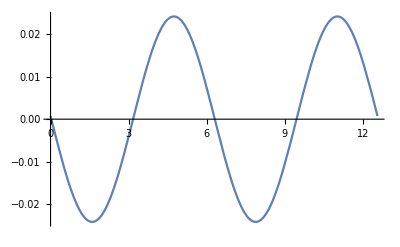

```mathematica
Plot[Exp[-I wp]ξrortplus[wr,wz,Υg,ξrortpluscoeff]+Exp[I wp]ξrortminus[wr,wz,Υg,ξrortminuscoeff]/.wr->π/5/.wz->23/4π,{wp,0,4π}]
```

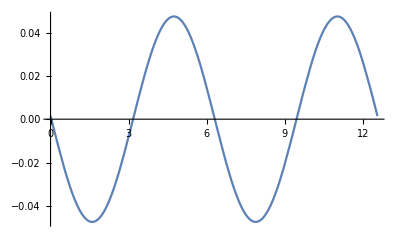

```mathematica
Plot[Exp[-I wp]ξzortplus[wr,wz,Υg,ξrortpluscoeff]+Exp[I wp]ξzortminus[wr,wz,Υg,ξrortminuscoeff]/.wr->π/5/.wz->23/4π,{wp,0,4π}]
```

```mathematica
Exp[-I wp]ξrortplus[wr,wz,Υg,ξrortpluscoeff]+Exp[I wp]ξrortminus[wr,wz,Υg,ξrortminuscoeff]/.wr->π/3/.wz->2π/9/.wp->π/12//AbsoluteTiming
```

{0.019065,-0.009039-3.46945×10^-18 ⅈ}

```mathematica
Exp[-I wp]ξzortplus[wr,wz,Υg,ξzortpluscoeff]+Exp[I wp]ξzortminus[wr,wz,Υg,ξzortminuscoeff]/.wr->π/3/.wz->2π/9/.wp->π/12//AbsoluteTiming
```

{0.022051,-0.0104795-1.9082×10^-17 ⅈ}

```mathematica
Exp[-I wp]ξrortplus[wr,wz,Υg,ξrortpluscoeff]+Exp[I wp]ξrortminus[wr,wz,Υg,ξrortminuscoeff]/.wr->π/3/.wz->2π/9/.wp->0//AbsoluteTiming
```

{0.015799,-0.00422795-1.73472×10^-18 ⅈ}

```mathematica
Exp[-I wp]ξzortplus[wr,wz,Υg,ξzortpluscoeff]+Exp[I wp]ξzortminus[wr,wz,Υg,ξzortminuscoeff]/.wr->π/3/.wz->2π/9/.wp->0//AbsoluteTiming
```

{0.013979,-0.0173472-1.73472×10^-17 ⅈ}

## 7) Fourier series coefficients for dt_s/dλ and dϕ_s/dλ - orthogonal component of the spin (∝ s_⊥)

### Fourier series for coordinate time and azimuthal velocity - orthogonal component in the spin

```mathematica
AbsoluteTiming[
dtsortplusdλcoeff=dtsortplusdλcoefffun[nmax,kmax,agen,pgen,egen,xggen,constmot,ξrortpluscoeff,ξzortpluscoeff];
dtsortminusdλcoeff=dtsortminusdλcoefffun[nmax,kmax,agen,pgen,egen,xggen,constmot,ξrortminuscoeff,ξzortminuscoeff];
]
```

{21.0774,Null}

```mathematica
AbsoluteTiming[
dϕsortplusdλcoeff=dϕsortplusdλcoefffun[nmax,kmax,agen,pgen,egen,xggen,constmot,ξrortpluscoeff,ξzortpluscoeff];
dϕsortminusdλcoeff=dϕsortminusdλcoefffun[nmax,kmax,agen,pgen,egen,xggen,constmot,ξrortminuscoeff,ξzortminuscoeff];
]
```

{21.1791,Null}

## 8) A note on the corrections to the velocities at the turning points

The shifts to the radial and polar velocities have removable singularities at the turning points (i.e the limits exist and are finite), which occurs at
- w_r=0,π for the radial velocities (χ_r=π/2, 3/2π)
- w_z=0,π for the polar velocities  (χ_z=π/2, 3/2π)

We computed the limits analytically, but we have not implemented them yet in the functions. Below are some numerical examples to show that the corrections to the trajectories are well define at the turning points.

The same conclusions apply to dχ_rs/dλ and dχ_zs/dλ.

NOTE: you need to compute the orbits with arbitrary precision to numerically check these limits. See the notebook “Corrections_orbits_plots.nb” for an example with arbitrary precision.

### Limits at the turning points, radial motion

#### Parallel component of the spin

```mathematica
{drsparFCdλfun[0+10^-7,π/23,agen,pgen,egen,xggen,constmot,ξrparFCcoeff],drsparFCdλfun[0-10^-7,π/23,agen,pgen,egen,xggen,constmot,ξrparFCcoeff]}
```

{-0.0186433,-0.0186393}

```mathematica
{drsparFCdλfun[π+10^-7,π/23,agen,pgen,egen,xggen,constmot,ξrparFCcoeff],drsparFCdλfun[π-10^-7,π/23,agen,pgen,egen,xggen,constmot,ξrparFCcoeff]}
```

{-0.00913689,-0.00915785}

```mathematica
{drsparDHdλfun[0+10^-7,π/23,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff],drsparDHdλfun[0-10^-7,π/23,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff]}
```

{-0.0186411,-0.0186415}

```mathematica
{drsparDHdλfun[π+10^-7,π/23,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff],drsparDHdλfun[π-10^-7,π/23,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff]}
```

{-0.00912803,-0.00916669}

#### Orthogonal component of the spin

```mathematica
{drsortdλfun[0+10^-7,π/23,π/3,agen,pgen,egen,xggen,constmot,ξrortpluscoeff,ξrortminuscoeff],drsortdλfun[0-10^-7,π/23,π/3,agen,pgen,egen,xggen,constmot,ξrortpluscoeff,ξrortminuscoeff]}
```

{-0.038489,-0.038489}

```mathematica
{drsortdλfun[π+10^-9,π/23,π/3,agen,pgen,egen,xggen,constmot,ξrortpluscoeff,ξrortminuscoeff],drsortdλfun[π-10^-9,π/23,π/3,agen,pgen,egen,xggen,constmot,ξrortpluscoeff,ξrortminuscoeff]}
```

{-0.0285866,-0.0285866}

### Limits at the turning points, polar motion

#### Parallel component of the spin

```mathematica
{dzsparFCdλfun[23π/5,0+10^-3,agen,pgen,egen,xggen,constmot,ξzparFCcoeff],dzsparFCdλfun[23π/5,0+10^-3,agen,pgen,egen,xggen,constmot,ξzparFCcoeff]}
```

{-0.19027,-0.19027}

```mathematica
{dzsparFCdλfun[23π/5,π+10^-3,agen,pgen,egen,xggen,constmot,ξzparFCcoeff],dzsparFCdλfun[23π/5,π+10^-3,agen,pgen,egen,xggen,constmot,ξzparFCcoeff]}
```

{0.19027,0.19027}

```mathematica
{dzsparDHdλfun[23π/5,0+10^-3,agen,pgen,egen,xggen,constmot,δconstmot,ξzparDHcoeff],dzsparDHdλfun[23π/5,0+10^-3,agen,pgen,egen,xggen,constmot,δconstmot,ξzparDHcoeff]}
```

{-0.190973,-0.190973}

```mathematica
{dzsparDHdλfun[23π/5,π+10^-3,agen,pgen,egen,xggen,constmot,δconstmot,ξzparDHcoeff],dzsparDHdλfun[23π/5,π+10^-3,agen,pgen,egen,xggen,constmot,δconstmot,ξzparDHcoeff]}
```

{0.190973,0.190973}

#### Orthogonal component of the spin

```mathematica
{dzsortdλfun[23π/5,0+10^-3,π/3,agen,pgen,egen,xggen,constmot,ξzortpluscoeff,ξzortminuscoeff],dzsortdλfun[23π/5,0+10^-3,π/3,agen,pgen,egen,xggen,constmot,ξzortpluscoeff,ξzortminuscoeff]}
```

{-0.0228058,-0.0228058}

```mathematica
{dzsortdλfun[23π/5,π+10^-3,π/3,agen,pgen,egen,xggen,constmot,ξzortpluscoeff,ξzortminuscoeff],dzsortdλfun[23π/5,π+10^-3,π/3,agen,pgen,egen,xggen,constmot,ξzortpluscoeff,ξzortminuscoeff]}
```

{-1.04328,-1.04328}

### Some examples for dχ_rs/dλ and dχ_zs/dλ

Same applies for the orthogonal component of the spin.

#### Radial part

```mathematica
{δYroverYrgsparFC[0+10^-3,π/23,agen,pgen,egen,xggen,constmot],δYroverYrgsparFC[0-10^-3,π/23,agen,pgen,egen,xggen,constmot]}
```

{-3.60807,-3.60807}

```mathematica
{δYroverYrgsparFC[π+10^-3,π/23,agen,pgen,egen,xggen,constmot],δYroverYrgsparFC[π-10^-3,π/23,agen,pgen,egen,xggen,constmot]}
```

{0.86823,0.868231}

```mathematica
{δYroverYrgsparDH[0+10^-3,π/23,agen,pgen,egen,xggen,constmot,δconstmot],δYroverYrgsparDH[0-10^-3,π/23,agen,pgen,egen,xggen,constmot,δconstmot]}
```

{0.694634,0.694633}

```mathematica
{δYroverYrgsparDH[π+10^-3,π/23,agen,pgen,egen,xggen,constmot,δconstmot],δYroverYrgsparDH[π-10^-3,π/23,agen,pgen,egen,xggen,constmot,δconstmot]}
```

{0.189657,0.189658}

#### Polar part

```mathematica
{δYzoverYzgsparFC[23π/5,0+10^-3,agen,pgen,egen,xggen,constmot],δYzoverYzgsparFC[23π/5,0-10^-3,agen,pgen,egen,xggen,constmot]}
```

{-0.270859,-0.270864}

```mathematica
{δYzoverYzgsparFC[23π/5,π+10^-3,agen,pgen,egen,xggen,constmot],δYzoverYzgsparFC[23π/5,π-10^-3,agen,pgen,egen,xggen,constmot]}
```

{-0.270859,-0.270864}

```mathematica
{δYzoverYzgsparDH[23π/5,0+10^-3,agen,pgen,egen,xggen,constmot,δconstmot],δYzoverYzgsparDH[23π/5,0-10^-3,agen,pgen,egen,xggen,constmot,δconstmot]}
```

{-0.0478672,-0.0478721}

```mathematica
{δYzoverYzgsparDH[23π/5,π+10^-3,agen,pgen,egen,xggen,constmot,δconstmot],δYzoverYzgsparDH[23π/5,π-10^-3,agen,pgen,egen,xggen,constmot,δconstmot]}
```

{-0.0478672,-0.0478721}

## 4) Comparison between parametrizations: fixed turning points (on average) and fixed constants of motion

## 1) Fourier coefficients orbits computed with Drummond, Hughes and Skoupý code

Parameters used in computation near equatorial orbit with Drummond, Hughes and Skoupý code:

```mathematica
nVcode=16;
kVcode=16;
```

```mathematica
agenDHScode=0.9`65;
pgenDHScode=4`65;
egenDHScode=0.5`65;
xggenDHScode=N[xggen,65];
```

```mathematica
{dtspardλcoeffDHScode,{radvelcoeffDHScode,radtrajcoeffDHScode},{polvelcoeffDHScode,poltrajcoeffDHScode},dϕspardλcoeffDHScode}=dataDHScodegenericorbit;
```

```mathematica
dvspardλFourierDHScode[wr_,wz_,coeff_]:=Module[{dimr,dimz},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;

 Sum[Exp[-I(n wr+k wz)]coeff[[n+dimr+1,k+dimz+1]],{n,-dimr,dimr},{k,-dimz,dimz}]
];
```

```mathematica
δysparFourierDHScode[wr_,wz_,coeff_]:=Module[{dimr,dimz},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;

 Sum[Exp[-I(n wr+k wz)]coeff[[n+dimr+1,k+dimz+1]],{n,-dimr,dimr},{k,-dimz,dimz}]
];
```

## 2) Comparison with Drummond, Hughes and Skoupý code

### Check shifts constants of motion in the fixed turning points (on average)

Result from Drummond, Hughes and Skoupý code

```mathematica
{δEEgenDHScode,δLzgenDHScode}={-0.0112012953570878862393533710367432215`24.45666781350502,0.26453432669535495070385594395769947718`24.900260460676403}
```

{-0.0112012953570878862393534,0.264534326695354950703856}

```mathematica
δconstmotionfun[agen,pgen,egen,xggen]
```

{-0.0112013,0.264534,2.59523}

### Maps of the radial and polar trajectories between the two parametrizations

#### Radial trajectory

```mathematica
ηrfun[wr_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,r1g,r2g,rspar,χr,r1savgsub,r2savgsub},
{EEg,Lzg,KKg}=const;

r1savgsub=r1savgFC[a,p,e,xg];
r2savgsub=r2savgFC[a,p,e,xg];

-(drgdr1gfun[wr,a,p,e,xg,const]r1savgsub+drgdr2gfun[wr,a,p,e,xg,const]r2savgsub)+(δconst[[1]]drgdEgfun[wr,a,p,e,xg,const]+δconst[[2]]drgdLzgfun[wr,a,p,e,xg,const]+δconst[[3]]drgdKgfun[wr,a,p,e,xg,const])
]
```

```mathematica
δysparFourierDHScode[3π/4`25,23π/7`25,radtrajcoeffDHScode]
```

0.63276078465903706199217+0. ⅈ

```mathematica
δrsparFCfun[3π/4`25,23π/7`25,agen,pgen,egen,xggen,constmot,ξrparFCcoeff]+ηrfun[3π/4`25,agen,pgen,egen,xggen,constmot,δconstmot]//AbsoluteTiming
```

{0.008254,0.63276}

```mathematica
δrsparDHfun[3π/4`25,23π/7`25,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff]//AbsoluteTiming
```

{0.004635,0.63276}

```mathematica
δysparFourierDHScode[3π/2`25,23π/7`25,radtrajcoeffDHScode]
```

0.3803851637343699163607+0. ⅈ

```mathematica
δrsparFCfun[3π/2`25,23π/7`25,agen,pgen,egen,xggen,constmot,ξrparFCcoeff]+ηrfun[3π/2`25,agen,pgen,egen,xggen,constmot,δconstmot]//AbsoluteTiming
```

{0.006916,0.380385}

```mathematica
δrsparDHfun[3π/2`25,23π/7`25,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff]//AbsoluteTiming
```

{0.003282,0.380385}

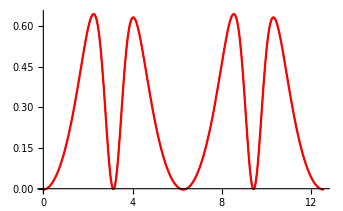

```mathematica
Show[Plot[δysparFourierDHScode[wr,23π/7`25,radtrajcoeffDHScode],{wr,0,4π},PlotStyle->{Black,AbsoluteThickness[0.9]}],Plot[δrsparDHfun[wr,23π/7`25,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff],{wr,0,4π},PlotStyle->{Red}]]
```

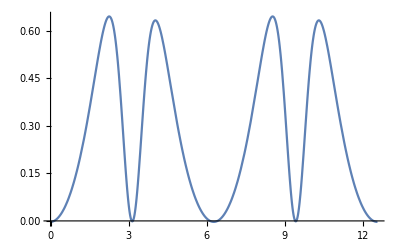

```mathematica
Plot[δrsparFCfun[wr,23π/7`25,agen,pgen,egen,xggen,constmot,ξrparFCcoeff]+ηrfun[wr,agen,pgen,egen,xggen,constmot,δconstmot],{wr,0,4π}]
```

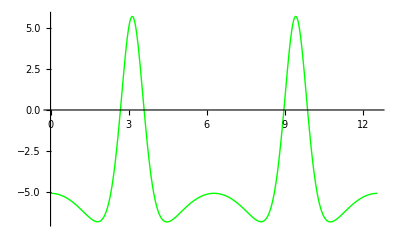

```mathematica
Plot[δrsparFCfun[wr,23π/7`25,agen,pgen,egen,xggen,constmot,ξrparFCcoeff],{wr,0,4π},PlotStyle->{Green,Thick}]
```

#### Polar trajectory

```mathematica
ηzfun[wz_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,z1g,z1savgsub,χz},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);

χz=χzfun[wz,a,p,e,xg,const];
z1savgsub=z1savgFC[a,p,e,xg];

- z1g Cos[χz]z1savgsub dχzdz1gfun[wz,a,p,e,xg,const] +(δconst[[1]]dzgdEgfun[wz,a,p,e,xg,const]+δconst[[2]]dzgdLzgfun[wz,a,p,e,xg,const])-Sin[χz]z1savgsub
]
```

```mathematica
δysparFourierDHScode[3π/4`25,23π/7`25,poltrajcoeffDHScode]
```

0.03976224202179739360669+0. ⅈ

```mathematica
δzsparFCfun[3π/4`25,23π/7`25,agen,pgen,egen,xggen,constmot,ξzparFCcoeff]+ηzfun[23π/7`25,agen,pgen,egen,xggen,constmot,δconstmot]//AbsoluteTiming
```

{0.004762,0.0397622}

```mathematica
δzsparDHfun[3π/4`25,23π/7`25,agen,pgen,egen,xggen,constmot,δconstmot,ξzparDHcoeff]//AbsoluteTiming
```

{0.002937,0.0397622}

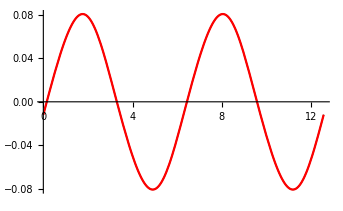

```mathematica
Show[Plot[δysparFourierDHScode[5π/3`25,wz,poltrajcoeffDHScode],{wz,0,4π},PlotStyle->{Black,AbsoluteThickness[0.9]}],Plot[δzsparDHfun[5π/3`25,wz,agen,pgen,egen,xggen,constmot,δconstmot,ξzparDHcoeff],{wz,0,4π},PlotStyle->{Red}]]
```

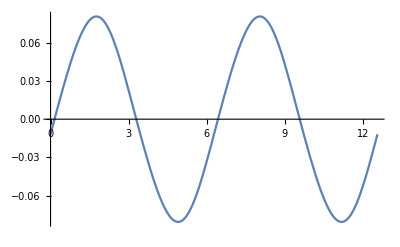

```mathematica
Plot[δzsparFCfun[5π/3`25,wz,agen,pgen,egen,xggen,constmot,ξzparFCcoeff]+ηzfun[wz,agen,pgen,egen,xggen,constmot,δconstmot],{wz,0,4π}]
```

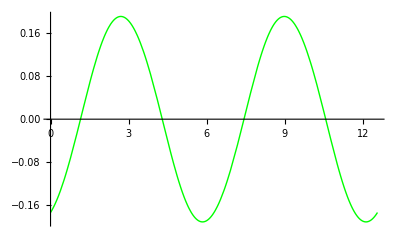

```mathematica
Plot[δzsparFCfun[5π/3`25,wz,agen,pgen,egen,xggen,constmot,ξzparFCcoeff],{wz,0,4π},PlotStyle->{Green,Thick}]
```

### Maps of the radial and polar velocities between the two parametrizations

#### Radial velocity

```mathematica
drsdλFCmapDH[wr_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,rg,Δrg,Rrg,dVrgdrg,dVrgdEg,dVrgdLzg,dVrgdKg,Yrg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
dVrgdrg=-(-2+2 rg) (KKg+rg^2)-2 rg Δrg+4 EEg rg Rrg;
dVrgdEg=2(rg^2+a^2)Rrg;
dVrgdLzg=-2a Rrg;
dVrgdKg=-Δrg;
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

1/(2Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g))Yrg)(ηrfun[wr,a,p,e,xg,const,δconst]dVrgdrg+δconst[[1]]dVrgdEg+δconst[[2]]dVrgdLzg+δconst[[3]]dVrgdKg)
]
```

```mathematica
dvspardλFourierDHScode[3π/4`25,23π/5`25,radvelcoeffDHScode]//AbsoluteTiming
```

{0.004203,1.754310835949916172968+0. ⅈ}

```mathematica
drsparFCdλfun[3π/4`25,23π/5`25,agen,pgen,egen,xggen,constmot,ξrparFCcoeff]+drsdλFCmapDH[3π/4`25,agen,pgen,egen,xggen,constmot,δconstmot]//AbsoluteTiming
```

{0.006657,1.75429}

```mathematica
drsparDHdλfun[3π/4`25,23π/5`25,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff]//AbsoluteTiming
```

{0.00554,1.75429}

```mathematica
dvspardλFourierDHScode[3π/2`25,23π/5`25,radvelcoeffDHScode]
```

-1.472900049145067734665+0. ⅈ

```mathematica
drsparFCdλfun[3π/2`25,23π/5`25,agen,pgen,egen,xggen,constmot,ξrparFCcoeff]+drsdλFCmapDH[3π/2`25,agen,pgen,egen,xggen,constmot,δconstmot]//AbsoluteTiming
```

{0.006819,-1.47289}

```mathematica
drsparDHdλfun[3π/2`25,23π/5`25,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff]//AbsoluteTiming
```

{0.005217,-1.47289}

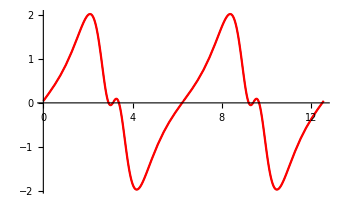

```mathematica
Show[Plot[dvspardλFourierDHScode[wr,23π/5`25,radvelcoeffDHScode],{wr,0,4π},PlotStyle->{Black,AbsoluteThickness[0.9]}],Plot[drsparDHdλfun[wr,23π/5`25,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff],{wr,0,4π},PlotStyle->{Red}]]
```

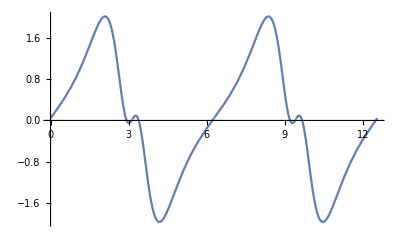

```mathematica
Plot[drsparFCdλfun[wr,23π/5`25,agen,pgen,egen,xggen,constmot,ξrparFCcoeff]+drsdλFCmapDH[wr,agen,pgen,egen,xggen,constmot,δconstmot],{wr,0,4π}]
```

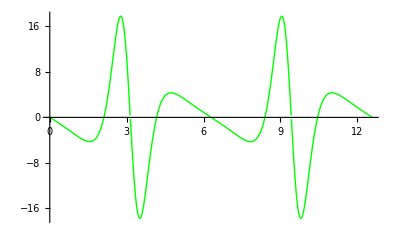

```mathematica
Plot[drsparFCdλfun[wr,23π/5`25,agen,pgen,egen,xggen,constmot,ξrparFCcoeff],{wr,0,4π},PlotStyle->{Green,Thick}]
```

#### Polar velocity

```mathematica
dzsdλFCmapDH[wz_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,z1g,z2g,rspar,χz,zg,Zzg,Yzg,dVzgdzg,dVzgdEg,dVzgdLzg,dVzgdKg},
{EEg,Lzg,KKg}=const;

z1g=√(1-xg^2);
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));

χz=χzfun[wz,a,p,e,xg,const];

zg=zgfun[wz,a,p,e,xg,const];

Zzg=(Lzg-a EEg (1-zg^2));
Yzg=√(-a^2 (1-EEg^2) zg^2+z2g^2);
dVzgdzg=-2 zg (KKg+a^2 (1-2 zg^2))-2 Zzg 2 a EEg zg;
dVzgdEg=2 a (1-zg^2) Zzg;
dVzgdLzg=-2Zzg;
dVzgdKg=1-zg^2;

1/(2z1g Cos[χz]Yzg)(ηzfun[wz,a,p,e,xg,const,δconst]dVzgdzg+δconst[[1]]dVzgdEg+δconst[[2]]dVzgdLzg+δconst[[3]]dVzgdKg)
]
```

```mathematica
dvspardλFourierDHScode[5π/3`25,23π/14`25,polvelcoeffDHScode]
```

0.07503311065213064052104+0. ⅈ

```mathematica
dzsparFCdλfun[5π/3`25,23π/14`25,agen,pgen,egen,xggen,constmot,ξzparFCcoeff]+dzsdλFCmapDH[23π/14`25,agen,pgen,egen,xggen,constmot,δconstmot]//AbsoluteTiming
```

{0.005188,0.0750331}

```mathematica
dzsparDHdλfun[5π/3`25,23π/14`25,agen,pgen,egen,xggen,constmot,δconstmot,ξzparDHcoeff]//AbsoluteTiming
```

{0.003436,0.0750331}

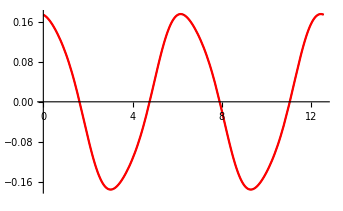

```mathematica
Show[Plot[dvspardλFourierDHScode[5π/3`25,wz,polvelcoeffDHScode],{wz,0,4π},PlotStyle->{Black,AbsoluteThickness[0.9]}],Plot[dzsparDHdλfun[5π/3`25,wz,agen,pgen,egen,xggen,constmot,δconstmot,ξzparDHcoeff],{wz,0,4π},PlotStyle->{Red}]]
```

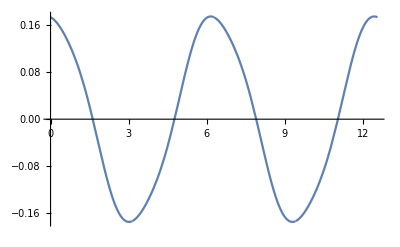

```mathematica
Plot[dzsparFCdλfun[5π/3`25,wz,agen,pgen,egen,xggen,constmot,ξzparFCcoeff]+dzsdλFCmapDH[wz,agen,pgen,egen,xggen,constmot,δconstmot],{wz,0,4π}]
```

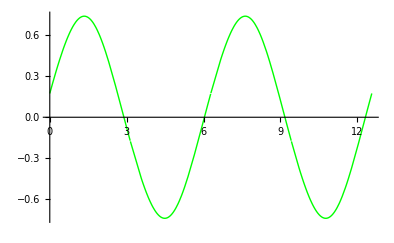

```mathematica
Plot[dzsparFCdλfun[5π/3`25,wz,agen,pgen,egen,xggen,constmot,ξzparFCcoeff],{wz,0,4π},PlotStyle->{Green,Thick}]
```

### Maps of the coordinate time and azimuthal velocities between the two parametrizations

#### Coordinate time velocity map

```mathematica
ηtrfun[wr_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,rg,Δrg,dVtrgdrg,dVtrgdEg,dVtrgdLzg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
dVtrgdrg=(2 a Lzg (rg^2-a^2))/Δrg^2+(4 EEg rg (a^2+rg^2))/Δrg-(2EEg (rg-1)  (a^2+rg^2)^2)/Δrg^2;
dVtrgdEg=((a^2+rg^2)^2)/Δrg;
dVtrgdLzg=-(2 a rg)/Δrg;

ηrfun[wr,a,p,e,xg,const,δconst]dVtrgdrg+δconst[[1]]dVtrgdEg+δconst[[2]]dVtrgdLzg
]
```

```mathematica
ηtzfun[wz_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,zg,dVtzgdzg,dVtzgdEg},
{EEg,Lzg,KKg}=const;

zg=zgfun[wz,a,p,e,xg,const];

dVtzgdzg=2 a^2 EEg zg;
dVtzgdEg=-a^2 (1-zg^2);

ηzfun[wz,a,p,e,xg,const,δconst]dVtzgdzg+δconst[[1]]dVtzgdEg
]
```

```mathematica
dvspardλFourierDHScode[π/4`25,23π/7`25,dtspardλcoeffDHScode]
```

-0.738314168821332519154+0. ⅈ

```mathematica
dtsparFCdλfun[π/4`25,23π/7`25,agen,pgen,egen,xggen,constmot,ξrparFCcoeff,ξzparFCcoeff]+ηtrfun[π/4`25,agen,pgen,egen,xggen,constmot,δconstmot]+ηtzfun[23π/7`25,agen,pgen,egen,xggen,constmot,δconstmot]//AbsoluteTiming
```

{0.01247,-0.738289}

```mathematica
dtsparDHdλfun[π/4`25,23π/7`25,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff,ξzparDHcoeff]//AbsoluteTiming
```

{0.006127,-0.738289}

```mathematica
dvspardλFourierDHScode[5π/9`25,23π/7`25,dtspardλcoeffDHScode]
```

3.19996123047458181878+0. ⅈ

```mathematica
dtsparFCdλfun[5π/9`25,23π/7`25,agen,pgen,egen,xggen,constmot,ξrparFCcoeff,ξzparFCcoeff]+ηtrfun[5π/9`25,agen,pgen,egen,xggen,constmot,δconstmot]+ηtzfun[23π/7`25,agen,pgen,egen,xggen,constmot,δconstmot]//AbsoluteTiming
```

{0.010909,3.19994}

```mathematica
dtsparDHdλfun[5π/9`25,23π/7`25,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff,ξzparDHcoeff]//AbsoluteTiming
```

{0.006045,3.19994}

#### Fourier expansion of the map between velocities - coordinate time velocity

```mathematica
ηtrcoefffun[nmax_,a_,p_,e_,xg_,const_,δconst_]:=Module[{stepsr,wrlist,ηtrlist,ExpniTable},
stepsr=4*nmax;
wrlist=Table[i,{i,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
ηtrlist=ηtrfun[wrlist,a,p,e,xg,const,δconst];
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
Chop[(ExpniTable . ηtrlist)/(stepsr),10^(-16)]
]
```

```mathematica
ηtzcoefffun[kmax_,a_,p_,e_,xg_,const_,δconst_]:=Module[{stepsz,wzlist,ηtzlist,ExpjkTable},
stepsz=4*kmax;
wzlist=Table[i,{i,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];
ηtzlist=ηtzfun[wzlist,a,p,e,xg,const,δconst];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];
Chop[(ηtzlist . ExpjkTable)/(stepsz),10^(-16)]
]
```

```mathematica
ηtrΔts[wr_,Υrg_,dev_,coeff_,coeffVtr_]:=Module[{dim},
dim=(Length[coeff]-1)/2;
Sum[2/(n Υrg) Sin[n wr]coeff[[n+dim+1]],{n,1,dim}]+dev Sum[2/(n Υrg^2) Sin[n wr]coeffVtr[[n+dim+1]],{n,1,dim}]
];
```

```mathematica
ηtzΔts[wz_,Υzg_,dev_,coeff_,coeffVtz_]:=Module[{dim},
dim=(Length[coeff]-1)/2;
Sum[2/(k Υzg)Sin[k wz]coeff[[k+dim+1]],{k,1,dim}]+dev Sum[2/(k Υzg^2) Sin[k wz]coeffVtz[[k+dim+1]],{k,1,dim}]
];
```

#### Azimuthal velocity map

```mathematica
ηϕrfun[wr_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,rg,Δrg,dVϕrgdrg,dVϕrgdEg,dVϕrgdLzg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
dVϕrgdrg=(2 a EEg rg)/Δrg-(2a (rg-1) (-a Lzg+EEg (a^2+rg^2)))/Δrg^2;
dVϕrgdEg=(2 a rg)/Δrg;
dVϕrgdLzg=-a^2/Δrg;

ηrfun[wr,a,p,e,xg,const,δconst]dVϕrgdrg+δconst[[1]]dVϕrgdEg+δconst[[2]]dVϕrgdLzg
]
```

```mathematica
ηϕzfun[wz_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,zg,dVϕzgdzg,dVϕzgdLzg},
{EEg,Lzg,KKg}=const;

zg=zgfun[wz,a,p,e,xg,const];

dVϕzgdzg=(2 Lzg zg)/((1-zg^2)^2);
dVϕzgdLzg=1/(1-zg^2);

ηzfun[wz,a,p,e,xg,const,δconst]dVϕzgdzg+δconst[[2]]dVϕzgdLzg
]
```

```mathematica
dvspardλFourierDHScode[π/4`25,23π/7`25,dϕspardλcoeffDHScode]
```

-0.687928474195396511336+0. ⅈ

```mathematica
dϕsparFCdλfun[π/4`25,23π/7`25,agen,pgen,egen,xggen,constmot,ξrparFCcoeff,ξzparFCcoeff]+ηϕrfun[π/4`25,agen,pgen,egen,xggen,constmot,δconstmot]+ηϕzfun[23π/7`25,agen,pgen,egen,xggen,constmot,δconstmot]//AbsoluteTiming
```

{0.011016,-0.687928}

```mathematica
dϕsparDHdλfun[π/4`25,23π/7`25,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff,ξzparDHcoeff]//AbsoluteTiming
```

{0.005602,-0.687928}

```mathematica
dvspardλFourierDHScode[5π/9`35,23π/7`25,dϕspardλcoeffDHScode]
```

-0.666660937313448467681+0. ⅈ

```mathematica
dϕsparFCdλfun[5π/9`35,23π/7`25,agen,pgen,egen,xggen,constmot,ξrparFCcoeff,ξzparFCcoeff]+ηϕrfun[5π/9`25,agen,pgen,egen,xggen,constmot,δconstmot]+ηϕzfun[23π/7`25,agen,pgen,egen,xggen,constmot,δconstmot]//AbsoluteTiming
```

{0.011078,-0.666661}

```mathematica
dϕsparDHdλfun[5π/9`25,23π/7`25,agen,pgen,egen,xggen,constmot,δconstmot,ξrparDHcoeff,ξzparDHcoeff]//AbsoluteTiming
```

{0.006052,-0.666661}

#### Fourier expansion of the map between velocities - azimuthal time velocity

```mathematica
ηϕrcoefffun[nmax_,a_,p_,e_,xg_,const_,δconst_]:=Module[{stepsr,wrlist,ηϕrlist,ExpniTable},
stepsr=4*nmax;
wrlist=Table[i,{i,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
ηϕrlist=ηϕrfun[wrlist,a,p,e,xg,const,δconst];
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
Chop[(ExpniTable . ηϕrlist)/(stepsr),10^(-16)]
]
```

```mathematica
ηϕzcoefffun[kmax_,a_,p_,e_,xg_,const_,δconst_]:=Module[{stepsz,wzlist,ηϕzlist,ExpjkTable},
stepsz=4*kmax;
wzlist=Table[i,{i,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];
ηϕzlist=ηϕzfun[wzlist,a,p,e,xg,const,δconst];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];
Chop[(ηϕzlist . ExpjkTable)/(stepsz),10^(-16)]
]
```

```mathematica
ηϕrΔϕs[wr_,Υrg_,dev_,coeff_,coeffVϕr_]:=Module[{dim},
dim=(Length[coeff]-1)/2;
Sum[2/(n Υrg) Sin[n wr]coeff[[n+dim+1]],{n,1,dim}]+dev Sum[2/(n Υrg^2) Sin[n wr]coeffVϕr[[n+dim+1]],{n,1,dim}]
];
```

```mathematica
ηϕzΔϕs[wz_,Υzg_,dev_,coeff_,coeffVϕz_]:=Module[{dim},
dim=(Length[coeff]-1)/2;
Sum[2/(k Υzg)Sin[k wz]coeff[[k+dim+1]],{k,1,dim}]+dev Sum[2/(k Υzg^2) Sin[k wz]coeffVϕz[[k+dim+1]],{k,1,dim}]
];
```

### Maps of the coordinate time and azimuthal trajectories between the two parametrizations

#### Coordinate time trajectory map

```mathematica
ηtrcoeff=ηtrcoefffun[nmax,agen,pgen,egen,xggen,constmot,δconstmot];
ηtzcoeff=ηtzcoefffun[kmax,agen,pgen,egen,xggen,constmot,δconstmot];
```

```mathematica
devradgen=freqdevrad[agen,pgen,egen,xggen];
devpolgen=freqdevpol[agen,pgen,egen,xggen];
```

```mathematica
ΔtsparFCfun[π/4`35,23π/7`35,{Υrggen,Υzggen,Υpgen},{ΥrsFCgen,ΥzsFCgen}]+ηtrΔts[π/4`35,Υrggen,devradgen,ηtrcoeff,dtrgdλcoeff]+ηtzΔts[23π/7`35,Υzggen,devpolgen,ηtzcoeff,dtzgdλcoeff]//AbsoluteTiming
```

{0.001652,2.21077+1.2987×10^-14 ⅈ}

```mathematica
ΔtsparDHfun[π/4`35,23π/7`35,{Υrggen,Υzggen,Υpgen},{ΥrsDHgen,ΥzsDHgen}]//AbsoluteTiming
```

{0.001282,2.21077+1.52916×10^-16 ⅈ}

#### Azimuthal trajectory map

```mathematica
ηϕrcoeff=ηϕrcoefffun[nmax,agen,pgen,egen,xggen,constmot,δconstmot];
ηϕzcoeff=ηϕzcoefffun[kmax,agen,pgen,egen,xggen,constmot,δconstmot];
```

```mathematica
devradgen=freqdevrad[agen,pgen,egen,xggen];
devpolgen=freqdevpol[agen,pgen,egen,xggen];
```

```mathematica
ΔϕsparFCfun[π/4`25,23π/7`25,{Υrggen,Υzggen,Υpgen},{ΥrsFCgen,ΥzsFCgen}]+ηϕrΔϕs[π/4`25,Υrggen,devradgen,ηϕrcoeff,dϕrgdλcoeff]+ηϕzΔϕs[23π/7`25,Υzggen,devpolgen,ηϕzcoeff,dϕzgdλcoeff]//AbsoluteTiming
```

{0.001429,-0.12717-3.01618×10^-17 ⅈ}

```mathematica
ΔϕsparDHfun[π/4`25,23π/7`25,{Υrggen,Υzggen,Υpgen},{ΥrsDHgen,ΥzsDHgen}]//AbsoluteTiming
```

{0.001284,-0.12717}

# Equatorial orbits

Important remark: in the equatorial limit, the radial and polar equations of motion for a spinning particle decouple. The radial, coordinate time and azimuthal motion depend only on the parallel component of the spin. By contrast, the polar motion is purely oscillatory in nature and depends only on the orthogonal component of the spin.

## 1) Spin-perturbed trajectories and velocities

## ξ_r and ξ_z shifts for near-identity transformation

```mathematica
ξrpareq[wr_,coeff_]:=Module[{dim},
dim=(Length[coeff]-1)/2;

- Sum[2Sin[n wr]coeff[[n+dim+1]]/(n),{n,1,dim}]
];
```

```mathematica
ξzpar[wr_,wz_,Υrg_,Υzg_,coeff_]:=Module[{dimr,dimz},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;

-2Υzg Sum[Sin[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg),{n,1,dimr},{k,1,dimz}]-2Υzg Sum[Sin[n wr+k wz]coeff[[n+dimr+1,k+dimz+1]]/(n*Υrg+k*Υzg),{n,1,dimr},{k,-dimz,-1}]-2(Υzg/Υrg)Sum[Sin[n wr]coeff[[n+dimr+1,dimz+1]]/n,{n,1,dimr}]-2 Sum[Sin[k wz]coeff[[dimr+1,k+dimz+1]]/k,{k,1,dimz}]
];
```

### Functions for ξ_(r∥) and ξ_(z∥) - fixed constants of motion

#### Function for ξ_(r∥)

```mathematica
δYroverYrgsparFCeq[wr_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,rg,zg,Yrg,Δ,Rrg,Rr1g,Rr2g,r1spar,r2spar,fraux2,fraux0,fraux},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

rg=rgfun[wr,a,p,e,xg,const];

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

Δ=(a^2-2 rg+rg^2);
Rrg=(a^2 EEg-a Lzg+EEg rg^2);
Rr1g=(a^2 EEg-a Lzg+EEg r1g^2);
Rr2g=(a^2 EEg-a Lzg+EEg r2g^2);

r1spar=r1sparFCfun[0,a,p,e,xg,const];
r2spar=r2sparFCfun[0,a,p,e,xg,const];

fraux2=Yrg/(√KKg) (EEg-(2 EEg KKg)/(KKg+rg^2)-(2 rg^2Rrg)/rg^4+Rrg/rg^2);
fraux0=(√KKg Δ Rrg)/((KKg+rg^2) (-rg+r1g) (rg-r2g) Yrg)+(a Δ  RealSign[Lzg-a EEg])/((-rg+r1g) (rg-r2g)Yrg)+(rg Rrg (KKg (-1+rg)+a (a-2 a EEg^2+2 EEg Lzg) rg+rg^2 (-3+2 (1-EEg^2) rg))KKg)/(√KKg rg^2 (KKg+rg^2) (rg-r1g) (rg-r2g) Yrg)-(r1spar-r2spar +(r1spar+r2spar)Sinχrfun[wr,a,p,e,xg,const])((r1g-r2g)Yrg)/(4(r1g-rg)(rg-r2g));
fraux=((r1spar+r2spar)/2+(r1spar-r2spar )/2 Sinχrfun[wr,a,p,e,xg,const])((1-EEg^2)(2 rg-r3g-r4g))/(2Yrg);

1/Yrg(fraux0+fraux2+fraux)
]
```

#### Function for ξ_(z∥)

```mathematica
δYzoverYzgsparFCeq[wr_,wz_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,z2g,χz,rg,Δ,Rrg,Lzred,fzaux2,fzaux0},
{EEg,Lzg,KKg}=const;

z2g=√(a^2(1-EEg^2)+Lzg^2);

χz=π/2+wz;

rg=rgfun[wr,a,p,e,xg,const];

Δ=(a^2-2 rg+rg^2);
Rrg=(a^2 EEg-a Lzg+EEg rg^2);
Lzred=Lzg-a EEg;

fzaux2=-z2g Rrg/(Lzred rg^2);
fzaux0=RealSign[Lzg]((a^2(1-EEg^2)+a EEg Lzg)/Lzred^2-((a^2 (1-EEg^2)+Lzg^2) (Lzred^2+rg^2 ))/(Lzred^2 rg^2))(a Tan[χz]^2)/z2g+a RealSign[Lzg](((a^2 (-1+EEg^2)-a EEg Lzg) rg^2+(Lzred^2+rg^2) z2g^2)/(Lzred^2rg^2z2g Cos[χz]^2));

1/z2g(fzaux0+fzaux2)
]
```

#### Functions for sampling

```mathematica
δYroverYrgsparFCcoeffeq[nmax_,a_,p_,e_,xg_,const_]:=Module[{stepsr,wrlist,ExpniTable},
stepsr=4*nmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];

Chop[(ExpniTable . δYroverYrgsparFCeq[wrlist,a,p,e,xg,const]) /(stepsr),10^-16]
]
```

```mathematica
δYzoverYzgsparFCcoeffeq[nmax_,kmax_,a_,p_,e_,xg_,const_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[-2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
 ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

Chop[ExpniTable . (Table[δYzoverYzgsparFCeq[wrlist[[i]],wzlist,a,p,e,xg,const],{i,stepsr}]) . ExpjkTable/(stepsr*stepsz),10^-16]
]
```

### Functions for ξ_(r∥) and ξ_(z∥) - fixed turning points (on average)

#### Function for ξ_(r∥)

```mathematica
δYroverYrgsparDHeq[wr_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,rg,zg,Yrg,Δ,Rrg,r1spar,r2spar,dVrgdEg,dVrgdLzg,dVrgdKg,fraux2,fraux0,fraux,fauxdC},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

rg=rgfun[wr,a,p,e,xg,const];

Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
Δ=(a^2-2 rg+rg^2);
Rrg=(a^2 EEg-a Lzg+EEg rg^2);

r1spar=r1sparDHfun[0,a,p,e,xg,const,δconst];
r2spar=r2sparDHfun[0,a,p,e,xg,const,δconst];

dVrgdEg=2(rg^2+a^2)Rrg;
dVrgdLzg=-2a Rrg;
dVrgdKg=-Δ;

fraux2=Yrg/(√KKg) (EEg-(2 EEg KKg)/(KKg+rg^2)-(2 rg^2Rrg)/rg^4+Rrg/rg^2);
fraux0=(√KKg Δ Rrg)/((KKg+rg^2) (-rg+r1g) (rg-r2g) Yrg)+(a Δ  RealSign[Lzg-a EEg])/((-rg+r1g) (rg-r2g)Yrg)+(rg Rrg (KKg (-1+rg)+a (a-2 a EEg^2+2 EEg Lzg) rg+rg^2 (-3+2 (1-EEg^2) rg))KKg)/(√KKg rg^2 (KKg+rg^2) (rg-r1g) (rg-r2g) Yrg)-(r1spar-r2spar +(r1spar+r2spar)Sinχrfun[wr,a,p,e,xg,const])((r1g-r2g)Yrg)/(4(r1g-rg)(rg-r2g));
fraux=((r1spar+r2spar)/2+(r1spar-r2spar )/2 Sinχrfun[wr,a,p,e,xg,const])((1-EEg^2)(2 rg-r3g-r4g))/(2Yrg);
fauxdC=(δconst[[1]]dVrgdEg+δconst[[2]]dVrgdLzg+δconst[[3]]dVrgdKg)/(2(-rg+r1g) (rg-r2g) Yrg);

1/Yrg(fraux0+fraux2+fraux+fauxdC)
]
```

#### Function for ξ_(z∥)

```mathematica
δYzoverYzgsparDHeq[wr_,wz_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,z2g,χz,rg,zg,Δ,Rrg,Lzred,fzaux2,fzaux0},
{EEg,Lzg,KKg}=const;

z2g=√(a^2(1-EEg^2)+Lzg^2);

χz=π/2+wz;

rg=rgfun[wr,a,p,e,xg,const];

Δ=(a^2-2 rg+rg^2);
Rrg=(a^2 EEg-a Lzg+EEg rg^2);
Lzred=Lzg-a EEg;

fzaux2=-z2g Rrg/(Lzred rg^2);
fzaux0=RealSign[Lzg]((a^2(1-EEg^2)+a EEg Lzg)/Lzred^2-((a^2 (1-EEg^2)+Lzg^2) (Lzred^2+rg^2 ))/(Lzred^2 rg^2))(a Tan[χz]^2)/z2g+a RealSign[Lzg](((a^2 (-1+EEg^2)-a EEg Lzg) rg^2+(Lzred^2+rg^2) z2g^2)/(Lzred^2rg^2z2g Cos[χz]^2))+
RealSign[Lzg](2 a (-2 a EEg+Lzg) δconst[[1]]+2 a EEg δconst[[2]]+δconst[[3]])/(2 z2g);

1/z2g(fzaux0+fzaux2)
]
```

#### Functions for sampling

```mathematica
δYroverYrgsparDHcoeffeq[nmax_,a_,p_,e_,xg_,const_,δconst_]:=Module[{stepsr,wrlist,ExpniTable},
stepsr=4*nmax;
ExpniTable=Table[N[Exp[-2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];

Chop[(ExpniTable . δYroverYrgsparDHeq[wrlist,a,p,e,xg,const,δconst]) /(stepsr),10^-16]
]
```

```mathematica
δYzoverYzgsparDHcoeffeq[nmax_,kmax_,a_,p_,e_,xg_,const_,δconst_]:=Module[{stepsr,stepsz,wrlist,wzlist,ExpniTable,ExpjkTable},
stepsr=4*nmax;
stepsz=4*kmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsz],Precision[{a,p,e,xg}]],{j,1,stepsz},{k,-kmax,kmax}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
wzlist=Table[wz,{wz,2Pi/(stepsz)/2,2Pi,2Pi/(stepsz)}];

Chop[ExpniTable . (Table[δYzoverYzgsparDHeq[wrlist[[i]],wzlist,a,p,e,xg,const,δconst],{i,stepsr}]) . ExpjkTable/(stepsr*stepsz),10^-16]
]
```

## Radial trajectories and velocities

### Radial trajectory - fixed constants of motion

```mathematica
δrsparFCfuneq[wr_,a_,p_,e_,xg_,const_,coeff_]:=Module[{EEg,Lzg,KKg,r1spar,r2spar,rspar},
{EEg,Lzg,KKg}=const;

r1spar=r1sparFCfun[0,a,p,e,xg,const];
r2spar=r2sparFCfun[0,a,p,e,xg,const];

rspar=1/2(r1spar+r2spar)+1/2(r1spar-r2spar)Sinχrfun[wr,a,p,e,xg,const];
rspar-drgdwrfun[wr,a,p,e,xg,const]Re[ξrpareq[wr,coeff]]
]
```

### Radial trajectory - fixed turning points (on average)

```mathematica
δrsparDHfuneq[wr_,a_,p_,e_,xg_,const_,δconst_,coeff_]:=Module[{EEg,Lzg,KKg,r1spar,r2spar,rspar},
{EEg,Lzg,KKg}=const;

r1spar=r1sparDHfun[0,a,p,e,xg,const,δconst];
r2spar=r2sparDHfun[0,a,p,e,xg,const,δconst];

rspar=1/2(r1spar+r2spar)+1/2(r1spar-r2spar)Sinχrfun[wr,a,p,e,xg,const];
rspar-drgdwrfun[wr,a,p,e,xg,const]Re[ξrpareq[wr,coeff]]
]
```

### Radial velocities - fixed constants of motion

```mathematica
drsparFCdλfuneq[wr_,a_,p_,e_,xg_,const_,coeff_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,χr,r1spar,r2spar,Υrg,Υzg,rg,rspar,Δrg,Rrg,Yrg,dVrgdrg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

r1spar=r1sparFCfun[0,a,p,e,xg,const];
r2spar=r2sparFCfun[0,a,p,e,xg,const];

rg=rgfun[wr,a,p,e,xg,const];
rspar=1/2(r1spar+r2spar)+1/2(r1spar-r2spar)Sinχrfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
dVrgdrg=2(1-rg) (KKg+rg^2)-2 rg Δrg+4 EEg rg Rrg;

1/(Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g))Yrg)(Δrg^2 𝒮12rfuneq[wr,a,p,e,xg,const]+a Δrg RealSign[Lzg-a EEg]+Δrg √KKg Rrg/(KKg+rg^2)+1/2 rspar dVrgdrg)-(drgdwrfun[wr,a,p,e,xg,const]dVrgdrg)/(2Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g))Yrg)Re[ξrpareq[wr,coeff]]
]
```

### Radial velocities - fixed turning points (on average)

```mathematica
drsparDHdλfuneq[wr_,a_,p_,e_,xg_,const_,δconst_,coeff_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,χr,r1spar,r2spar,rg,rspar,Δrg,Rrg,Yrg,dVrgdrg,dVrgdEg,dVrgdLzg,dVrgdKg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

r1spar=r1sparDHfun[0,a,p,e,xg,const,δconst];
r2spar=r2sparDHfun[0,a,p,e,xg,const,δconst];

rg=rgfun[wr,a,p,e,xg,const];
rspar=1/2(r1spar+r2spar)+1/2(r1spar-r2spar)Sinχrfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));
dVrgdrg=2(1-rg) (KKg+rg^2)-2 rg Δrg+4 EEg rg Rrg;
dVrgdEg=2(rg^2+a^2)Rrg;
dVrgdLzg=-2a Rrg;
dVrgdKg=-Δrg;

1/(Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g))Yrg)(Δrg^2 𝒮12rfuneq[wr,a,p,e,xg,const]+a Δrg RealSign[Lzg-a EEg]+Δrg √KKg Rrg/(KKg+rg^2)+1/2 rspar dVrgdrg+1/2(δconst[[1]]dVrgdEg +δconst[[2]]dVrgdLzg+δconst[[3]]dVrgdKg))-(drgdwrfun[wr,a,p,e,xg,const]dVrgdrg)/(2Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g))Yrg)Re[ξrpareq[wr,coeff]]
]
```

## Coordinate time and azimuthal velocities

### Coordinate time velocity - fixed constants of motion

```mathematica
dtsparFCdλfuneq[wr_,a_,p_,e_,xg_,const_,coeffrad_]:=Module[{EEg,Lzg,KKg,rg,zg,Δrg,dVtrgdrg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);

dVtrgdrg=(2 a Lzg (rg^2-a^2))/Δrg^2+(4 EEg rg (a^2+rg^2))/Δrg-(2EEg (rg-1)  (a^2+rg^2)^2)/Δrg^2;

dVtrgdrg δrsparFCfuneq[wr,a,p,e,xg,const,coeffrad] -rg^2/2 Γt12funeq[wr,a,p,e,xg,const]
]
```

```mathematica
dtsparFCdλcoefffuneq[nmax_,a_,p_,e_,xg_,const_,coeffrad_]:=Module[{stepsr,wrlist,wzlist,ExpniTable},
stepsr=4*nmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];

Chop[(ExpniTable . dtsparFCdλfuneq[wrlist,a,p,e,xg,const,coeffrad])/(stepsr),10^-16]
]
```

### Azimuthal velocity - fixed constants of motion

```mathematica
dϕsparFCdλfuneq[wr_,a_,p_,e_,xg_,const_,coeffrad_]:=Module[{EEg,Lzg,KKg,rg,zg,Δrg,dVϕrgdrg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);

dVϕrgdrg=(2 a EEg rg)/Δrg-(2a (rg-1) (-a Lzg+EEg (a^2+rg^2)))/Δrg^2;

dVϕrgdrg δrsparFCfuneq[wr,a,p,e,xg,const,coeffrad]-rg^2/2 Γϕ12funeq[wr,a,p,e,xg,const]
]
```

```mathematica
dϕsparFCdλcoefffuneq[nmax_,a_,p_,e_,xg_,const_,coeffrad_]:=Module[{stepsr,wrlist,wzlist,ExpniTable},
stepsr=4*nmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];

Chop[(ExpniTable . dϕsparFCdλfuneq[wrlist,a,p,e,xg,const,coeffrad])/(stepsr),10^-16]
]
```

### Coordinate time velocity - fixed turning points (on average)

```mathematica
dtsparDHdλfuneq[wr_,a_,p_,e_,xg_,const_,δconst_,coeffrad_]:=Module[{EEg,Lzg,KKg,rg,Δrg,Rrg,dVtrgdrg,dVtrgdEg,dVtrgdLzg,dVtzgdEg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(a^2 EEg-a Lzg+EEg rg^2);

dVtrgdrg=(2 a Lzg (rg^2-a^2))/Δrg^2+(4 EEg rg (a^2+rg^2))/Δrg-(2EEg (rg-1)  (a^2+rg^2)^2)/Δrg^2;
dVtrgdEg=((a^2+rg^2)^2)/Δrg;
dVtrgdLzg=-(2 a rg)/Δrg;
dVtzgdEg=-a^2 ;

dVtrgdrg δrsparDHfuneq[wr,a,p,e,xg,const,δconst,coeffrad]+(δconst[[1]]dVtrgdEg+δconst[[2]]dVtrgdLzg)+(δconst[[1]]dVtzgdEg)-rg^2/2 Γt12funeq[wr,a,p,e,xg,const]
]
```

```mathematica
dtsparDHdλcoefffuneq[nmax_,a_,p_,e_,xg_,const_,δconst_,coeffrad_]:=Module[{stepsr,wrlist,wzlist,ExpniTable},
stepsr=4*nmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];

Chop[(ExpniTable . dtsparDHdλfuneq[wrlist,a,p,e,xg,const,δconst,coeffrad])/(stepsr),10^-16]
]
```

### Azimuthal velocity - fixed turning points (on average)

```mathematica
dϕsparDHdλfuneq[wr_,a_,p_,e_,xg_,const_,δconst_,coeffrad_]:=Module[{EEg,Lzg,KKg,rg,Δrg,dVϕrgdrg,dVϕrgdEg,dVϕrgdLzg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);

dVϕrgdrg=(2 a EEg rg)/Δrg-(2a (rg-1) (-a Lzg+EEg (a^2+rg^2)))/Δrg^2;
dVϕrgdEg=(2 a rg)/Δrg;
dVϕrgdLzg=-a^2/Δrg;

dVϕrgdrg δrsparDHfuneq[wr,a,p,e,xg,const,δconst,coeffrad]+(δconst[[1]]dVϕrgdEg+δconst[[2]]dVϕrgdLzg)+δconst[[2]]-rg^2/2 Γϕ12funeq[wr,a,p,e,xg,const]
]
```

```mathematica
dϕsparDHdλcoefffuneq[nmax_,a_,p_,e_,xg_,const_,δconst_,coeffrad_]:=Module[{stepsr,wrlist,wzlist,ExpniTable},
stepsr=4*nmax;
ExpniTable=Table[N[Exp[2Pi*I*n*(i-1/2)/stepsr],Precision[{a,p,e,xg}]],{n,-nmax,nmax},{i,1,stepsr}];

wrlist=Table[wr,{wr,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];

Chop[(ExpniTable . dϕsparDHdλfuneq[wrlist,a,p,e,xg,const,δconst,coeffrad])/(stepsr),10^-16]
]
```

## Coordinate time and azimuthal trajectories

The functional structure for Δt_(s∥) and Δϕ_(s∥) is the same for both parametrizations. So I create just one Mathematica function that I will specialize later on.

```mathematica
Δspareq[wr_,Υrg_,Υrs_,δcoeff_,coeffVtr_]:=Module[{dimr},
dimr=(Length[δcoeff]-1)/2;

Sum[2Sin[n wr]δcoeff[[n+dimr+1]]/(n*Υrg),{n,1,dimr}]-Υrs Sum[2Sin[n wr]coeffVtr[[n+dimr+1]]/(n*Υrg^2),{n,1,dimr}]
]
```

## Polar trajectories and velocities

### Polar trajectory orthogonal component of the spin

#### Term proportional to e^(-i w_p) (j=+1)

```mathematica
δzsortplusfuneq[wr_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,zsort,ψpbar},
{EEg,Lzg,KKg}=const;

zsort=z1sortCosψfun[wr,a,p,e,xg,const];
ψpbar[wr]:=ψrfun[wr,a,p,e,xg,const];

zsort(Cos[ψpbar[wr]]+I Sin[ψpbar[wr]])
]
```

#### Term proportional to e^(i w_p) (j=-1)

```mathematica
δzsortminusfuneq[wr_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,zsort,ψpbar},
{EEg,Lzg,KKg}=const;

zsort=z1sortCosψfun[wr,a,p,e,xg,const];
ψpbar[wr]:=ψrfun[wr,a,p,e,xg,const];

zsort(Cos[ψpbar[wr]]-I Sin[ψpbar[wr]])
]
```

#### Putting things together

```mathematica
δzsorteq[wr_,wp_,a_,p_,e_,xg_,const_]:=Re[δzsortplusfuneq[wr,a,p,e,xg,const]Exp[-I wp]+δzsortminusfuneq[wr,a,p,e,xg,const]Exp[I wp]]
```

```mathematica
(*2 zsort Cos[wp+ψpbar[wr]]*)
```

### Polar velocity

#### Polar velocity orthogonal component of the spin - Sinψ_p

```mathematica
dzsortSinψdλfuneq[wr_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,rg,Δrg,Rrg,vrg,Lzred},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(a^2 EEg-a Lzg+EEg rg^2);
vrg=√(Rrg^2-Δrg(KKg+rg^2));
Lzred=Lzg-a EEg;

-(vrg^2  a/(Lzred Δrg rg √(KKg+rg^2)))-((Rrg(2rg Lzred-Lzg rg^2))/(Lzred Δrg rg √(KKg+rg^2)))
]
```

#### Polar velocity orthogonal component of the spin - Cosψ_p

```mathematica
dzsortCosψdλfuneq[wr_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,rg,zsort,Δ,Rrg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];
zsort=z1sortCosψfun[wr,a,p,e,xg,const];

Δ=(a^2-2 rg+rg^2);
Rrg=(a^2 EEg-a Lzg+EEg rg^2);

((-a EEg+Lzg) Sign[Pi-Mod[wr,2Pi]] √(Rrg^2-Δ(KKg+rg^2)))/(rg^2 √((-a EEg+Lzg)^2+rg^2))
]
```

#### Polar velocity orthogonal component of the spin - term proportional to e^(-i w_p) (j=+1)

```mathematica
dzsortplusdλfuneq[wr_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,ψpbar},
{EEg,Lzg,KKg}=const;

ψpbar[wr]:=ψrfun[wr,a,p,e,xg,const];

1/2(dzsortCosψdλfuneq[wr,a,p,e,xg,const]+I dzsortSinψdλfuneq[wr,a,p,e,xg,const])(Cos[ψpbar[wr]]+I Sin[ψpbar[wr]])
]
```

#### Polar velocity orthogonal component of the spin - term proportional to e^(i w_p) (j=-1)

```mathematica
dzsortminusdλfuneq[wr_,a_,p_,e_,xg_,const_]:=Module[{EEg,Lzg,KKg,ψpbar},
{EEg,Lzg,KKg}=const;

ψpbar[wr]:=ψrfun[wr,a,p,e,xg,const];

1/2(dzsortCosψdλfuneq[wr,a,p,e,xg,const]-I dzsortSinψdλfuneq[wr,a,p,e,xg,const])(Cos[ψpbar[wr]]-I Sin[ψpbar[wr]])
]
```

#### Putting things together

```mathematica
dzsortdλfuneq[wr_,wp_,a_,p_,e_,xg_,const_]:=Re[dzsortplusdλfuneq[wr,a,p,e,xg,const]Exp[-I wp]+dzsortminusdλfuneq[wr,a,p,e,xg,const]Exp[I wp]]
```

```mathematica
(*dzsortCosψdλfuneq[wr,a,p,e,xg,const]Cos[wp+ψpbar[wr]]+dzsortSinψdλfuneq[wr,a,p,e,xg,const] Sin[wp+ψpbar[wr]]*)
```

## 2) Computation quantities for the trajectories and velocities

## 1) Geodesic quantities

### For numerical tests

```mathematica
aeq=0.9;
peq=4;
eeq=0.5;
z1geq=0;
xgeq=√(1-z1geq^2);
```

Roots geodesic potential

```mathematica
r1geq=peq/(1-eeq);
```

```mathematica
r2geq=peq/(1+eeq);
```

```mathematica
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));
```

```mathematica
z2g=√(a^2(1-EEg^2)+Lzg^2/(1-z1g^2));
```

```mathematica
{EEgeq,Lzgeq,KKgeq}={EEgfun[aeq,peq,eeq,xgeq],Lzgfun[aeq,peq,eeq,xgeq],KKgfun[aeq,peq,eeq,xgeq]}
```

{0.914313,2.45697,2.67025}

```mathematica
constmoteq={EEgeq,Lzgeq,KKgeq};
```

```mathematica
{Υrgeq,Υzgeq,Υϕgeq,Υtgeq}={Υrgfun[aeq,peq,eeq,xgeq],Υzgfun[aeq,peq,eeq,xgeq],Υϕgrfun[aeq,peq,eeq,xgeq]+Υϕgzfun[aeq,peq,eeq,xgeq],Υtgrfun[aeq,peq,eeq,xgeq]+Υtgzfun[aeq,peq,eeq,xgeq]}
```

{1.44393,2.48386,3.03386,33.6775}

Geodesic radial, polar frequencies and spin precession frequency.

```mathematica
Υpeq=Υpfun[aeq,peq,eeq,xgeq];
```

```mathematica
Υgeq={Υrgeq,Υzgeq,Υpeq};
```

```mathematica
geofreqeq={Υrg->Υrgeq,Υzg->Υzgeq,Υϕg->Υϕgeq,Υtg->Υtgeq};
```

```mathematica
orbpareq={EEg->EEgeq,Lzg->Lzgeq,KKg->KKgeq,r1g->r1geq,r2g->r2geq,z1g->z1geq,a->aeq};
```

Positive part radial and polar potentials

```mathematica
Yrg=√((1-EEg^2)(r3-r)(r4-r));
```

```mathematica
Yzg=√(z2^2-a^2(1-EEg^2)z^2);
```

### Building Fourier series for geodesics velocities dt_g/dλand dϕ_g/dλ

Number of terms in the Fourier series expansion. FCe use the same of number terms in all Fourier series expansions.
 Just use an even number of terms (I have not implemented the functions to take an odd number of terms in input yet )

```mathematica
nmax=12;
kmax=12;
```

Orbits with high eccentricity and/or inclination may require larger values.

```mathematica
AbsoluteTiming[
dtrgdλcoeffeq=Vtrgcoeff[nmax,aeq,peq,eeq,xgeq,constmoteq];
dtzgdλcoeffeq=Vtzgcoeff[kmax,aeq,peq,eeq,xgeq,constmoteq];
]
```

{0.007825,Null}

```mathematica
AbsoluteTiming[
dϕrgdλcoeffeq=Vϕrgcoeff[nmax,aeq,peq,eeq,xgeq,constmoteq];
dϕzgdλcoeffeq=Vϕzgcoeff[kmax,aeq,peq,eeq,xgeq,constmoteq];
]
```

{0.007671,Null}

```mathematica
(1-(dtrgdλcoeffeq[[nmax+1]]+dtzgdλcoeffeq[[kmax+1]])/Υtgeq)*100
```

4.44089×10^-14

```mathematica
(1-(dϕrgdλcoeffeq[[nmax+1]]+dϕzgdλcoeffeq[[kmax+1]])/Υϕgeq)*100
```

-4.44089×10^-14

## 2) Constants of motion and frequency shifts

### Shifts constants of motion in the fixed turning points (on average)

```mathematica
{δEEeq,δLzeq,δKKeq}=δconstmotionfun[aeq,peq,eeq,xgeq];
δconstmoteq={δEEeq,δLzeq,δKKeq};
```

### Check that the turning point shifts in the Drummond & Hughes parametrization average to zero

```mathematica
NIntegrate[r1sparDHfun[wz,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq],{wz,0,2π},WorkingPrecision->20]
```

NIntegrate::precw: The precision of the argument function (-3.42837×10^-13) is less than WorkingPrecision (20.).

-2.1541075843701310611×10^-12

```mathematica
NIntegrate[r2sparDHfun[wz,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq],{wz,0,2π},WorkingPrecision->20]
```

NIntegrate::precw: The precision of the argument function (3.94795×10^-13) is less than WorkingPrecision (20.).

2.4805720757837390069×10^-12

```mathematica
NIntegrate[z1sparDHfun[wr,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq],{wr,0,2π},WorkingPrecision->20]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0

### Frequency shifts - fixed constants of motion

```mathematica
AbsoluteTiming[{ΥrsFCeq,ΥzsFCeq,ΥϕsFCeq,ΥtsFCeq}={ΥrsfunFC[aeq,peq,eeq,xgeq,MachinePrecision],ΥzsfunFC[aeq,peq,eeq,xgeq,MachinePrecision],ΥϕsfunFC[aeq,peq,eeq,xgeq,MachinePrecision],ΥtsfunFC[aeq,peq,eeq,xgeq,MachinePrecision]};]
```

{0.302323,Null}

```mathematica
ΥsFCeq={ΥrsFCeq,ΥzsFCeq};
```

```mathematica
spinfreqFCeq={Υrs->ΥrsFCeq,Υzs->ΥzsFCeq,Υϕs->ΥϕsFCeq,Υts->ΥtsFCeq};
```

### Frequency shifts - fixed turning points (on average)

```mathematica
AbsoluteTiming[{ΥrsDHeq,ΥzsDHeq,ΥϕsDHeq,ΥtsDHeq}={ΥrsfunDH[aeq,peq,eeq,xgeq,δconstmoteq,MachinePrecision],ΥzsfunDH[aeq,peq,eeq,xgeq,δconstmoteq,MachinePrecision],ΥϕsfunDH[aeq,peq,eeq,xgeq,δconstmoteq,MachinePrecision],ΥtsfunDH[aeq,peq,eeq,xgeq,δconstmoteq,MachinePrecision]};]
```

{0.25752,Null}

```mathematica
ΥsDHeq={ΥrsDHeq,ΥzsDHeq};
```

```mathematica
spinfreqDHeq={Υrs->ΥrsDHeq,Υzs->ΥzsDHeq,Υϕs->ΥϕsDHeq,Υts->ΥtsDHeq};
```

## 3) Fourier series coefficients for ξ_r and ξ_z - parallel component of the spin (∝ s_∥)

Number of terms in the Fourier series expansion. FCe use the same of number terms in all Fourier series expansions.
 Just use an even number of terms (I have not implemented the functions to take an odd number of terms in input yet)

```mathematica
nmax=12;
kmax=12;
```

Orbits with high eccentricity and/or inclination may require larger values.

For the fastest way to compute radial and polar frequency shifts, check:

“Fourier series for ξ_r and ξ_z - fixed constants of motion/Comparison computation radial frequency shifts” 
 “Fourier series for ξ_r and ξ_z - fixed constants of motion/Comparison computation polar frequency shifts”

### Fourier series for ξ_r and ξ_z - fixed constants of motion

#### Sampling for ξ_(r∥) and ξ_(z∥)

```mathematica
AbsoluteTiming[
ξrparFCcoeffeq=δYroverYrgsparFCcoeffeq[nmax,aeq,peq,eeq,xgeq,constmoteq];
ξzparFCcoeffeq=δYzoverYzgsparFCcoeffeq[nmax,kmax,aeq,peq,eeq,xgeq,constmoteq];
]
```

{0.032115,Null}

```mathematica
nmaxless=4;
kmaxless=4;
```

```mathematica
AbsoluteTiming[
ξrparFCcoefflesseq=δYroverYrgsparFCcoeffeq[nmaxless,N[aeq],N[peq],N[eeq],N[xgeq],constmoteq];
ξzparFCcoefflesseq=δYzoverYzgsparFCcoeffeq[nmaxless,kmaxless,N[aeq],N[peq],N[eeq],N[xgeq],constmoteq];
]
```

{0.005263,Null}

#### Comparison computation radial frequency shifts

Radial frequency shift

```mathematica
ΥrsFCeq
```

-0.876399

```mathematica
Υrgeq ξrparFCcoeffeq[[nmax+1]]
```

-0.876399

```mathematica
Υrgeq ξrparFCcoefflesseq[[nmaxless+1]]
```

-0.876399

```mathematica
1-ξrparFCcoeffeq[[nmax+1]]/ξrparFCcoefflesseq[[nmaxless+1]]
```

1.65423×10^-13

#### Comparison computation polar frequency shifts

```mathematica
ΥzsFCeq
```

-0.50813

```mathematica
Υzgeq ξzparFCcoeffeq[[nmax+1,kmax+1]]
```

-0.50813

```mathematica
Υzgeq ξzparFCcoefflesseq[[nmaxless+1,kmaxless+1]]
```

-0.50813

```mathematica
1-ξzparFCcoeffeq[[nmax+1,kmax+1]]/ξzparFCcoefflesseq[[nmaxless+1,kmaxless+1]]
```

2.66454×10^-15

#### Some cross checks

Cross check. It should improve with higher terms in ξ_r and ξ_z

```mathematica
(Υrg D[ξrpareq[wr,ξrparFCcoeffeq],wr])/.geofreqeq/.wr->5
```

0.507639+1.27802×10^-16 ⅈ

```mathematica
ΥrsfunFC[aeq,peq,eeq,xgeq,MachinePrecision]-Υrg δYroverYrgsparFCeq[wr,aeq,peq,eeq,xgeq,constmoteq]/.wr->5/.geofreqeq
```

0.507639

```mathematica
(Υrg D[ξzpar[wr,wz,Υrgeq,Υzgeq,ξzparFCcoeffeq],wr]+Υzg D[ξzpar[wr,wz,Υrgeq,Υzgeq,ξzparFCcoeffeq],wz])/.geofreqeq/.wr->5/.wz->4
```

-0.0737129+1.36121×10^-15 ⅈ

```mathematica
ΥzsfunFC[aeq,peq,eeq,xgeq,MachinePrecision]-δYzoverYzgsparFCeq[wr,wz,aeq,peq,eeq,xgeq,constmoteq]Υzg/.wr->5/.wz->4/.geofreqeq
```

-0.0737129

### Fourier series for ξ_r and ξ_z - fixed turning points (on average)

#### Sampling for ξ_(r∥) and ξ_(z∥)

```mathematica
AbsoluteTiming[
ξrparDHcoeffeq=δYroverYrgsparDHcoeffeq[nmax,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq];
ξzparDHcoeffeq=δYzoverYzgsparDHcoeffeq[nmax,kmax,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq];
]
```

{0.033807,Null}

```mathematica
nmaxless=4;
kmaxless=4;
```

```mathematica
AbsoluteTiming[
ξrparDHcoefflesseq=δYroverYrgsparDHcoeffeq[nmaxless,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq];
ξzparDHcoefflesseq=δYzoverYzgsparDHcoeffeq[nmaxless,kmaxless,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq];
]
```

{0.005452,Null}

#### Comparison computation radial frequency shifts

Radial frequency shift

```mathematica
ΥrsDHeq
```

0.496974

```mathematica
Υrgeq ξrparDHcoeffeq[[nmax+1]]
```

0.496974

```mathematica
Υrgeq ξrparDHcoefflesseq[[nmaxless+1]]
```

0.496974

```mathematica
1-ξrparDHcoeffeq[[nmax+1]]/ξrparDHcoefflesseq[[nmaxless+1]]
```

-3.70592×10^-13

#### Comparison computation polar frequency shifts

```mathematica
ΥzsDHeq
```

-0.00329778

```mathematica
Υzgeq ξzparDHcoeffeq[[nmax+1,kmax+1]]
```

-0.00329778

```mathematica
Υzgeq ξzparDHcoefflesseq[[nmaxless+1,kmaxless+1]]
```

-0.00329778

```mathematica
1-ξzparDHcoeffeq[[nmax+1,kmax+1]]/ξzparDHcoefflesseq[[nmaxless+1,kmaxless+1]]
```

4.76952×10^-13

#### Some cross checks

Cross check. It should improve with higher terms in ξ_r and ξ_z

```mathematica
(Υrg D[ξrpareq[wr,ξrparDHcoeffeq],wr])/.geofreqeq/.wr->5
```

-0.068895

```mathematica
(ΥrsfunFC[aeq,peq,eeq,xgeq,MachinePrecision]-freqdevrad[aeq,peq,eeq,xgeq])-Υrg δYroverYrgsparDHeq[wr,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq]/.wr->5/.geofreqeq
```

-0.068895

```mathematica
(Υrg D[ξzpar[wr,wz,Υrgeq,Υzgeq,ξzparDHcoeffeq],wr]+Υzg D[ξzpar[wr,wz,Υrgeq,Υzgeq,ξzparDHcoeffeq],wz])/.geofreqeq/.wr->5/.wz->4
```

-0.0737129-1.39×10^-15 ⅈ

```mathematica
(ΥzsfunFC[aeq,peq,eeq,xgeq,MachinePrecision]-freqdevpol[aeq,peq,eeq,xgeq])-Υzg δYzoverYzgsparDHeq[wr,wz,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq]/.wr->5/.wz->4/.geofreqeq
```

-0.0737129

## 4) Fourier series coefficients for dt_s/dλ and dϕ_s/dλ - parallel component of the spin (∝ s_∥)

Number of terms in the Fourier series expansion. FCe use the same of number terms in all Fourier series expansions.
 Just use an even number of terms (I have not implemented the functions to take an odd number of terms in input yet )

```mathematica
nmax=12;
kmax=12;
```

Orbits with high eccentricity and/or inclination may require larger values.

### Coordinate time and azimuthal velocity - fixed constants of motion

```mathematica
AbsoluteTiming[
dtsparFCdλcoeffeq=dtsparFCdλcoefffuneq[nmax,aeq,peq,eeq,xgeq,constmoteq,ξrparFCcoeffeq];
dϕsparFCdλcoeffeq=dϕsparFCdλcoefffuneq[nmax,aeq,peq,eeq,xgeq,constmoteq,ξrparFCcoeffeq];
]
```

{0.018927,Null}

```mathematica
dtsparFCdλcoeffeq[[nmax+1]]
```

-15.2102

```mathematica
ΥtsFCeq
```

-15.2102

```mathematica
dϕsparFCdλcoeffeq[[nmax+1]]
```

0.0600124

```mathematica
ΥϕsFCeq
```

0.0600124

```mathematica
AbsoluteTiming[
dtsparFCdλcoefflesseq=dtsparFCdλcoefffuneq[4,aeq,peq,eeq,xgeq,constmoteq,ξrparFCcoeffeq];
dϕsparFCdλcoefflesseq=dϕsparFCdλcoefffuneq[4,aeq,peq,eeq,xgeq,constmoteq,ξrparFCcoeffeq];
]
```

{0.00478,Null}

```mathematica
1-ΥtsFCeq/dtsparFCdλcoefflesseq[[4+1]]
```

0.0000196155

```mathematica
1-ΥϕsFCeq/dϕsparFCdλcoefflesseq[[4+1]]
```

1.86806×10^-11

### Coordinate time and azimuthal velocity - fixed turning points (on average)

```mathematica
AbsoluteTiming[
dtsparDHdλcoeffeq=dtsparDHdλcoefffuneq[nmax,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq,ξrparDHcoeffeq];
dϕsparDHdλcoeffeq=dϕsparDHdλcoefffuneq[nmax,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq,ξrparDHcoeffeq];
]
```

{0.015465,Null}

```mathematica
dtsparDHdλcoeffeq[[nmax+1]]
```

1.1563

```mathematica
ΥtsDHeq
```

1.1563

```mathematica
dϕsparDHdλcoeffeq[[nmax+1]]
```

-0.474678

```mathematica
ΥϕsDHeq
```

-0.474678

```mathematica
AbsoluteTiming[
dtsparDHdλcoefflesseq=dtsparDHdλcoefffuneq[4,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq,ξrparDHcoeffeq];
dϕsparDHdλcoefflesseq=dϕsparDHdλcoefffuneq[4,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq,ξrparDHcoeffeq];
]
```

{0.007263,Null}

```mathematica
1-ΥtsDHeq/dtsparDHdλcoefflesseq[[4+1]]
```

0.0000299558

```mathematica
1-ΥϕsDHeq/dϕsparDHdλcoefflesseq[[4+1]]
```

2.82209×10^-11

## 5) Fourier series expansion correction coordinate time and azimuthal trajectories - parallel component of the spin (∝ s_∥)

### Coordinate time and azimuthal trajectories - fixed constants of motion

```mathematica
ΔtsparFCfuneq[wr_,Υrg_,Υrs_]:=Δspareq[wr,Υrg,Υrs,dtsparFCdλcoeffeq,dtrgdλcoeffeq]
```

```mathematica
ΔϕsparFCfuneq[wr_,Υrg_,Υrs_]:=Δspareq[wr,Υrg,Υrs,dϕsparFCdλcoeffeq,dϕrgdλcoeffeq]
```

### Coordinate time and azimuthal trajectories - fixed turning points (on average)

```mathematica
ΔtsparDHfuneq[wr_,Υrg_,Υrs_]:=Δspareq[wr,Υrg,Υrs,dtsparDHdλcoeffeq,dtrgdλcoeffeq]
```

```mathematica
ΔϕsparDHfuneq[wr_,Υrg_,Υrs_]:=Δspareq[wr,Υrg,Υrs,dϕsparDHdλcoeffeq,dϕrgdλcoeffeq]
```

## 3) Comparison between parametrizations: fixed turning points (on average) and fixed constants of motion

## 1) Fourier coefficients orbits computed with Drummond, Hughes and Skoupý code

Unfortunately, Drummond, Hughes and Skoupý  code crashes in the limit of equatorial limits, so we computed the trajectories and velocities for nearly equatorial orbits.

Parameters used in computation near equatorial orbit with Drummond, Hughes and Skoupý code:

```mathematica
nVcodeeq=12;
kVcodeeq=12;
```

```mathematica
aeqDHScode=0.9`85;
peqDHScode=4`85;
eeqDHScode=0.5`85;
xgeqDHScode=N[1-10^-6,85];
```

```mathematica
{dtspardλcoeffDHScodeeq,{radvelcoeffDHScodeeq,radtrajcoeffDHScodeeq},{polvelcoeffDHScodeeq,poltrajcoeffDHScodeeq},dϕspardλcoeffDHScodeeq}=dataDHScodenearequorbit;
```

```mathematica
dvspardλFourierDHScode[wr_,wz_,coeff_]:=Module[{dimr,dimz},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;

 Sum[Exp[-I(n wr+k wz)]coeff[[n+dimr+1,k+dimz+1]],{n,-dimr,dimr},{k,-dimz,dimz}]
];
```

```mathematica
δysparFourierDHScode[wr_,wz_,coeff_]:=Module[{dimr,dimz},
dimr=(Dimensions[coeff][[1]]-1)/2;
dimz=(Dimensions[coeff][[2]]-1)/2;

 Sum[Exp[-I(n wr+k wz)]coeff[[n+dimr+1,k+dimz+1]],{n,-dimr,dimr},{k,-dimz,dimz}]
];
```

## 2) Comparison with Drummond, Hughes and Skoupý code

### Check shifts constants of motion in the fixed turning points (on average)

Result from Drummond, Hughes and Skoupý code

```mathematica
{δEEgenDHScodeeq,δLzgenDHScodeeq}={-0.01107603169537763501631781470680513846`20.496876239670947,0.50701733504586213039368221559515846721`21.206829042704264}
```

{-0.011076031695377635016,0.507017335045862130394}

```mathematica
δconstmotionfun[aeq,peq,eeq,xgeq]
```

{-0.011076,0.507019,1.68961}

### Maps of the radial trajectories between the two parametrizations

```mathematica
ηrfun[wr_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,r1savgsub,r2savgsub},
{EEg,Lzg,KKg}=const;

r1savgsub=r1savgFC[a,p,e,xg];
r2savgsub=r2savgFC[a,p,e,xg];

-(drgdr1gfun[wr,a,p,e,xg,const]r1savgsub+drgdr2gfun[wr,a,p,e,xg,const]r2savgsub)+(δconst[[1]]drgdEgfun[wr,a,p,e,xg,const]+δconst[[2]]drgdLzgfun[wr,a,p,e,xg,const]+δconst[[3]]drgdKgfun[wr,a,p,e,xg,const])
]
```

```mathematica
δysparFourierDHScode[3π/2`25,23π/7`25,radtrajcoeffDHScodeeq]
```

0.2980510189570516951+0. ⅈ

```mathematica
δrsparFCfuneq[3π/2`35,aeq,peq,eeq,xgeq,constmoteq,ξrparFCcoeffeq]+ηrfun[3π/2`35,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq]//AbsoluteTiming
```

{0.004779,0.298055}

```mathematica
δrsparDHfuneq[3π/2`35,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq,ξrparDHcoeffeq]//AbsoluteTiming
```

{0.000404,0.298055}

### Maps of the radial velocities between the two parametrizations

```mathematica
drsdλFCmapDH[wr_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,r1g,r2g,r3g,r4g,δr,χr,rg,Δrg,Rrg,dVrgdrg,dVrgdEg,dVrgdLzg,dVrgdKg,Yrg},
{EEg,Lzg,KKg}=const;

r1g=p/(1-e);
r2g=p/(1+e);
r3g=1/(1-EEg^2)-(r1g+r2g)/2+Sqrt[(((r1g+r2g)/2-1/(1-EEg^2))^2-(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2)))];
r4g=1/r3g(a^2(KKg-(Lzg-a EEg)^2))/(r1g r2g (1-EEg^2));

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
Rrg=(-a Lzg+EEg (a^2+rg^2));
dVrgdrg=-(-2+2 rg) (KKg+rg^2)-2 rg Δrg+4 EEg rg Rrg;
dVrgdEg=2(rg^2+a^2)Rrg;
dVrgdLzg=-2a Rrg;
dVrgdKg=-Δrg;
Yrg=√((1-EEg^2) (-rg+r3g) (-rg+r4g));

1/(2Sign[π-Mod[wr,2 π]] √((r1g-rg)(rg-r2g))Yrg)(ηrfun[wr,a,p,e,xg,const,δconst]dVrgdrg+δconst[[1]]dVrgdEg+δconst[[2]]dVrgdLzg+δconst[[3]]dVrgdKg)
]
```

```mathematica
dvspardλFourierDHScode[3π/2`25,23π/7`25,radvelcoeffDHScodeeq]
```

-1.359580058349379681+0. ⅈ

```mathematica
drsparFCdλfuneq[3π/2`35,aeq,peq,eeq,xgeq,constmoteq,ξrparFCcoeffeq]+drsdλFCmapDH[3π/2`35,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq]//AbsoluteTiming
```

{0.003381,-1.35939}

```mathematica
drsparDHdλfuneq[3π/2`35,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq,ξrparDHcoeffeq]//AbsoluteTiming
```

{0.000603,-1.35939}

### Maps of the coordinate time and azimuthal velocities between the two parametrizations

#### Coordinate time velocity map

```mathematica
ηtrfun[wr_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,rg,Δrg,dVtrgdrg,dVtrgdEg,dVtrgdLzg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
dVtrgdrg=(2 a Lzg (rg^2-a^2))/Δrg^2+(4 EEg rg (a^2+rg^2))/Δrg-(2EEg (rg-1)  (a^2+rg^2)^2)/Δrg^2;
dVtrgdEg=((a^2+rg^2)^2)/Δrg;
dVtrgdLzg=-(2 a rg)/Δrg;

ηrfun[wr,a,p,e,xg,const,δconst]dVtrgdrg+δconst[[1]]dVtrgdEg+δconst[[2]]dVtrgdLzg
]
```

```mathematica
dvspardλFourierDHScode[π/4`25,23π/7`25,dtspardλcoeffDHScodeeq]
```

-0.732613415864228511+0. ⅈ

```mathematica
dtsparFCdλfuneq[π/4`35,aeq,peq,eeq,xgeq,constmoteq,ξrparFCcoeffeq]+ηtrfun[π/4`35,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq]-aeq^2δconstmoteq[[1]]//AbsoluteTiming
```

{0.003445,-0.733002}

```mathematica
dtsparDHdλfuneq[π/4`35,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq,ξrparDHcoeffeq]//AbsoluteTiming
```

{0.000608,-0.733002}

```mathematica
dvspardλFourierDHScode[5π/9`25,23π/7`25,dtspardλcoeffDHScodeeq]
```

2.41618396857348953+0. ⅈ

```mathematica
dtsparDHdλfuneq[5π/9`35,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq,ξrparDHcoeffeq]//AbsoluteTiming
```

{0.000634,2.41561}

```mathematica
dtsparFCdλfuneq[5π/9`35,aeq,peq,eeq,xgeq,constmoteq,ξrparFCcoeffeq]+ηtrfun[5π/9`35,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq]-aeq^2δconstmoteq[[1]]//AbsoluteTiming
```

{0.003474,2.41561}

#### Fourier expansion of the map between velocities - coordinate time velocity

```mathematica
ηtrcoefffun[nmax_,a_,p_,e_,xg_,const_,δconst_]:=Module[{stepsr,wrlist,ηtrlist,ExpjkTable},
stepsr=4*nmax;
wrlist=Table[i,{i,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
ηtrlist=ηtrfun[wrlist,a,p,e,xg,const,δconst];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsr],Precision[{a,p,e,xg}]],{j,1,stepsr},{k,-nmax,nmax}];
Chop[ηtrlist . ExpjkTable/(stepsr),10^-16]
]
```

```mathematica
ηtrΔts[wr_,Υrg_,dev_,coeff_,coeffVtr_]:=Module[{dim},
dim=(Length[coeff]-1)/2;
Sum[2/(n Υrg) Sin[n wr]coeff[[n+dim+1]],{n,1,dim}]+dev Sum[2/(n Υrg^2) Sin[n wr]coeffVtr[[n+dim+1]],{n,1,dim}]
];
```

#### Azimuthal velocity map

```mathematica
ηϕrfun[wr_,a_,p_,e_,xg_,const_,δconst_]:=Module[{EEg,Lzg,KKg,rg,Δrg,dVϕrgdrg,dVϕrgdEg,dVϕrgdLzg},
{EEg,Lzg,KKg}=const;

rg=rgfun[wr,a,p,e,xg,const];

Δrg=(a^2-2 rg+rg^2);
dVϕrgdrg=(2 a EEg rg)/Δrg-(2a (rg-1) (-a Lzg+EEg (a^2+rg^2)))/Δrg^2;
dVϕrgdEg=(2 a rg)/Δrg;
dVϕrgdLzg=-a^2/Δrg;

ηrfun[wr,a,p,e,xg,const,δconst]dVϕrgdrg+δconst[[1]]dVϕrgdEg+δconst[[2]]dVϕrgdLzg
]
```

```mathematica
dvspardλFourierDHScode[π/4`25,23π/7`25,dϕspardλcoeffDHScodeeq]
```

-0.5103360344082114427+0. ⅈ

```mathematica
dϕsparFCdλfuneq[π/4`25,aeq,peq,eeq,xgeq,constmoteq,ξrparFCcoeffeq]+ηϕrfun[π/4`25,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq]+δconstmoteq[[2]]//AbsoluteTiming
```

{0.003419,-0.510335}

```mathematica
dϕsparDHdλfuneq[π/4`25,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq,ξrparDHcoeffeq]//AbsoluteTiming
```

{0.000619,-0.510335}

```mathematica
dvspardλFourierDHScode[5π/9`25,23π/7`25,dϕspardλcoeffDHScodeeq]
```

-0.4794313224006830539+0. ⅈ

```mathematica
dϕsparDHdλfuneq[5π/9`25,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq,ξrparDHcoeffeq]//AbsoluteTiming
```

{0.000609,-0.47943}

```mathematica
dϕsparFCdλfuneq[5π/9`25,aeq,peq,eeq,xgeq,constmoteq,ξrparFCcoeffeq]+ηϕrfun[5π/9`25,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq]+δconstmoteq[[2]]//AbsoluteTiming
```

{0.003558,-0.47943}

#### Fourier expansion of the map between velocities - azimuthal time velocity

```mathematica
ηϕrcoefffun[nmax_,a_,p_,e_,xg_,const_,δconst_]:=Module[{stepsr,wrlist,ηϕrlist,ExpjkTable},
stepsr=4*nmax;
wrlist=Table[i,{i,2Pi/(stepsr)/2,2Pi,2Pi/(stepsr)}];
ηϕrlist=ηϕrfun[wrlist,a,p,e,xg,const,δconst];
ExpjkTable=Table[N[Exp[2Pi*I*k*(j-1/2)/stepsr],Precision[{a,p,e,xg}]],{j,1,stepsr},{k,-nmax,nmax}];
Chop[ηϕrlist . ExpjkTable/(stepsr),10^-16]
]
```

```mathematica
ηϕrΔϕs[wr_,Υrg_,dev_,coeff_,coeffVϕr_]:=Module[{dim},
dim=(Length[coeff]-1)/2;
Sum[2/(n Υrg) Sin[n wr]coeff[[n+dim+1]],{n,1,dim}]+dev Sum[2/(n Υrg^2) Sin[n wr]coeffVϕr[[n+dim+1]],{n,1,dim}]
];
```

### Maps of the coordinate time and azimuthal trajectories between the two parametrizations

#### Coordinate time trajectory map

```mathematica
ηtrcoeffeq=ηtrcoefffun[nmax,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq];
```

```mathematica
devradeq=freqdevrad[aeq,peq,eeq,xgeq];
devpoleq=freqdevpol[aeq,peq,eeq,xgeq];
```

```mathematica
ΔtsparFCfuneq[π/4`35,Υrgeq,ΥrsFCeq]+ηtrΔts[π/4`35,Υrgeq,devradeq,ηtrcoeffeq,dtrgdλcoeffeq]
```

1.80909+1.86574×10^-15 ⅈ

```mathematica
ΔtsparDHfuneq[π/4`35,Υrgeq,ΥrsDHeq]
```

1.80909+1.70606×10^-16 ⅈ

#### Azimuthal trajectory map

```mathematica
ηϕrcoeffeq=ηϕrcoefffun[nmax,aeq,peq,eeq,xgeq,constmoteq,δconstmoteq];
```

```mathematica
devradeq=freqdevrad[aeq,peq,eeq,xgeq];
devpoleq=freqdevpol[aeq,peq,eeq,xgeq];
```

```mathematica
ΔϕsparFCfuneq[π/4`35,Υrgeq,ΥrsFCeq]+ηϕrΔϕs[π/4`35,Υrgeq,devradeq,ηϕrcoeffeq,dϕrgdλcoeffeq]
```

-0.0795371+1.98499×10^-16 ⅈ

```mathematica
ΔϕsparDHfuneq[π/4`35,Υrgeq,ΥrsDHeq]
```

-0.0795371